# Predicting immune response to pertussis vaccination: data analysis and models (work with TxBiomed team) Oct 2024 - Nov 2024

```mathematica
PicturesPath=$HomeDirectory<>"/research/immunology/vaccinations/pertussis-predicting/challenge-3rd";
If[$VersionNumber<6,
Get[$HomeDirectory<>"/refs/mathematica/my_packages/graphics.m"],
Get[$HomeDirectory<>"/refs/mathematica/my_packages/graphics-12-2.m"];
];
Get[$HomeDirectory<>"/refs/mathematica/my_packages/tests.m"];
Get[$HomeDirectory<>"/refs/mathematica/my_packages/tools-12.m"];
Get[$HomeDirectory<>"/refs/mathematica/my_packages/bootstrap-2r.m"]
```

Analysis of the data

## Antibody dynamics

### 2020 data: IgG to PT

```mathematica
data1=Import[PicturesPath<>"/data/data-rearranged/subjects2020_antibodies.xlsx","XLSX"];
data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | subject_id
2 | specimen_id
3 | actual_day_relative_to_boost
4 | isotype
5 | is_antigen_specific
6 | antigen
7 | MFI
8 | MFI_normalised
9 | unit
10 | lower_limit_of_detection

```mathematica
posID=1;
posAg=6;
posIg=4;
posDay=3;
posMFI=7;
posMFIn=8;

allIDs=Union[Drop[data[[All,1]],1]];

tmin=Min[Drop[data[[All,posDay]],1]];
tmax=Max[Drop[data[[All,posDay]],1]];
```

```mathematica
(* total IgG *)

alldataIgGPT=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG" && #[[posAg]]=="PT"&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

alldataIgGPTn=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG" && #[[posAg]]=="PT"&):>{x[[posDay]],Log10[x[[posMFIn]]]}],{id,1,Length[allIDs]}];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

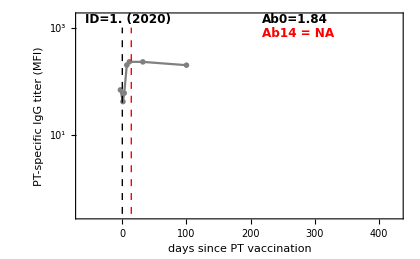
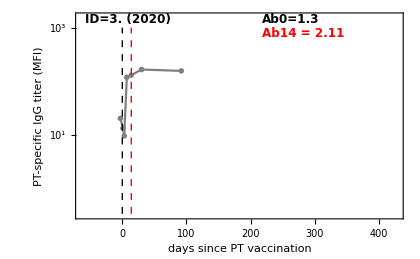
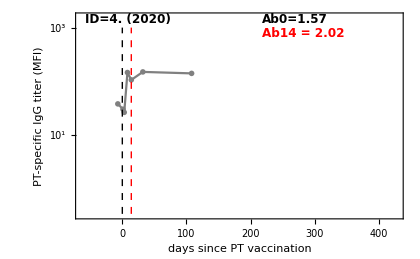
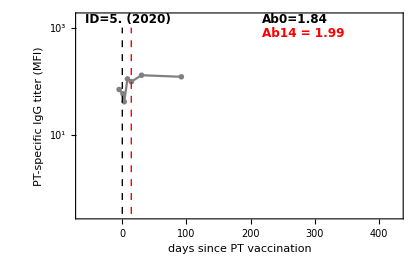
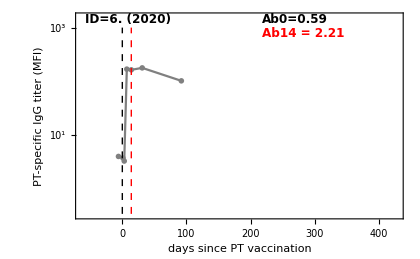
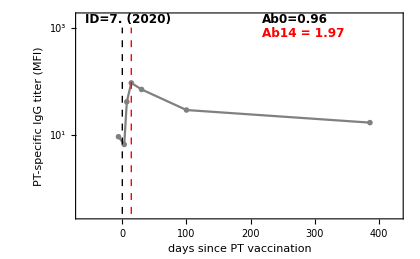
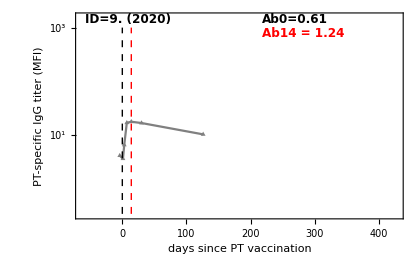
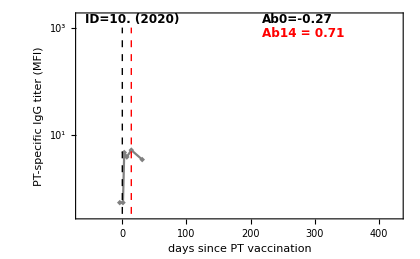

```mathematica
(* MFI *)

Table[
Ab0=MyRound[Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
MyListPlot[{alldataIgGPT[[id]]},
PlotStyle->Gray,
PlotRange->{{tmin,tmax},{-0.5,3.2}},
FrameTicks->{myticks,logticks[{-1,6,1}]},
FrameLabel->{"days since PT vaccination","PT-specific IgG titer (MFI)"},
Epilog->{
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]},
mylegend2noS[{"ID="<>ToString[allIDs[[id]]]<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"Ab0="<>ToString[Ab0],"Ab14 = "<>ToString[Ab14]},{0.52,0.97}]
},
PlotMarkers->{symbols[[id]]},
Joined->True
],{id,1,Length[allIDs]}
]

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI.pdf",%,"PDF"];
```

```mathematica
(* Day 0 Ab to Day 14 Ab: MFI *)

tempdata1=
Table[
Ab0=MyRound[Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab14=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];
tempdata2=Map[Transpose[{{1,2},#}]&,dataAb0Ab14];

tempdata10=
Table[
Ab0=MyRound[Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab140=Cases[tempdata10,x_?(VectorQ[#,NumericQ]&)];
tempdata20=Map[Transpose[{{1,2},#}]&,dataAb0Ab140];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

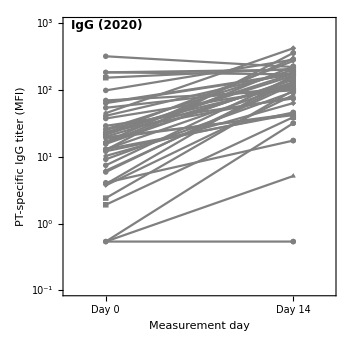
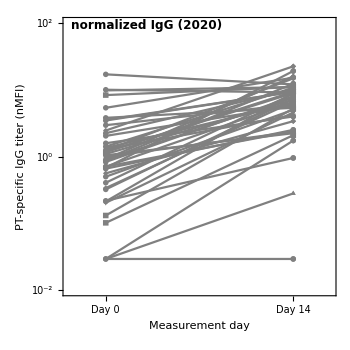

```mathematica
{
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,3.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[tempdata20,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-2.0,2.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-4,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (nMFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"normalized IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
]
}

MyGraphicsArray[%];
```

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI-nMFI-change-day0-14-2panels.pdf",%,"PDF"];
```

```mathematica
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,3.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
]
```

-Graphics-

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI-change-day0-14.pdf",%,"PDF"];
```

```mathematica
(* normalized MFI *)

Table[
Ab0=MyRound[Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
MyListPlot[{alldataIgGPTn[[id]]},
PlotStyle->Gray,
PlotRange->{{tmin,tmax},{-2,2.3}},
FrameTicks->{myticks,logticks[{-3,6,1}]},
FrameLabel->{"days since PT vaccination","PT-specific IgG titer (nMFI)"},
Epilog->{
{Dashed,Line[{{0,-2},{0,3}}]},
{Dashed,Red,Line[{{14,-2},{14,3}}]},
mylegend2noS[{"ID="<>ToString[allIDs[[id]]]<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"Ab0="<>ToString[Ab0],"Ab14 = "<>ToString[Ab14]},{0.52,0.97}]
},
PlotMarkers->{symbols[[id]]},
Joined->True
],{id,1,Length[allIDs]}
];

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-nMFI.pdf",%,"PDF"];
```

### 2020 data: IgG to all Ags

```mathematica
data1=Import[PicturesPath<>"/data/data-rearranged/subjects2020_antibodies.xlsx","XLSX"];
data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | subject_id
2 | specimen_id
3 | actual_day_relative_to_boost
4 | isotype
5 | is_antigen_specific
6 | antigen
7 | MFI
8 | MFI_normalised
9 | unit
10 | lower_limit_of_detection

```mathematica
posID=1;
posAg=6;
posIg=4;
posDay=3;
posMFI=7;
posMFIn=8;

allIDs=Union[Drop[data[[All,posID]],1]];

tmin=Min[Drop[data[[All,posDay]],1]];
tmax=Max[Drop[data[[All,posDay]],1]];

allAgs=Union[Drop[data[[All,posAg]],1]];

Transpose[{Range[Length[allAgs]],allAgs}]//TableForm
```

1 | ACT
2 | BETV1
3 | DT
4 | FELD1
5 | FHA
6 | FIM2/3
7 | LOLP1
8 | LOS
9 | Measles
10 | OVA
11 | PD1
12 | PRN
13 | PT
14 | PTM
15 | Total
16 | TT

```mathematica
(* Looping through all Isotypes for one Ag *)

allAgs0={"PT"};

myFigALLAbs=
Table[
allIgGs=Union[Cases[data,x_?( #[[posAg]]==allAgs0[[Ag]]&):>x[[posIg]]]];
allIgGs=ReverseSort[allIgGs];
Table[
IgG=allIgGs[[igg]];
alldataIgG=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]==IgG && #[[posAg]]==allAgs0[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];
tempdata1=
Table[
Ab0=MyRound[Last[Cases[alldataIgG[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgG[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab14=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];
tempdata2=Map[Transpose[{{1,2},#}]&,dataAb0Ab14];
tempdata3=AverageDataOne[Flatten[tempdata2,1]];
foldAb=10^(tempdata3[[2,2]]-tempdata3[[1,2]]);

Show[
MyListPlot[tempdata2,
Joined->True,
PlotMarkers->None,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-2,6}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-2,6,1}]},
FrameLabel->{"Measurement day",allAgs0[[Ag]]"-specific "<>IgG<>" titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{allAgs0[[Ag]]<>": "<>IgG<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"x"<>ToString[MyRound[foldAb,2]]},{0.42,0.85},FontColor->{Red}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
},
Options[MyListPlot]
],
MyListPlot[{tempdata3},
Joined->True,
PlotMarkers->Line,
PlotStyle->{{Red,Thick}}
]
]
,{igg,1,Length[allIgGs]}
]
,{Ag,1,Length[allAgs0]}
]
```

```mathematica
(* total IgG to Ag *)

Ag=16;
allAgs[[Ag]]
allIgGs=Union[Cases[data,x_?( #[[posAg]]==allAgs[[Ag]]&):>x[[posIg]]]]
```

TT

{IgE,IgG1,IgG2,IgG3,IgG4}

```mathematica
Off[General::partw]
Off[Last::nolast]

(* IgG *)
alldataIgG=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG1" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

(* IgG1 *)
alldataIgG1=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG1" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

(* IgG2 *)
alldataIgG2=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG2" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

(* IgG3 *)
alldataIgG3=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG3" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

(* IgG4 *)
alldataIgG4=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG4" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

(* IgGE *)
alldataIgE=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgE" && #[[posAg]]==allAgs[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];
```

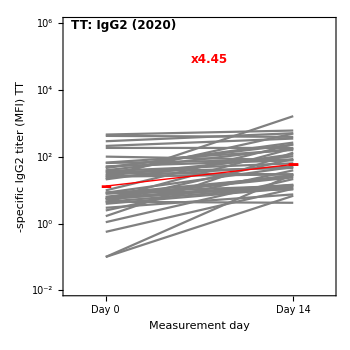

```mathematica
(* Day 0 Ab to Day 14 Ab: MFI *)

IgG="IgE";
IgG="IgG2";

alldataIgG=
Which[
IgG=="IgG",alldataIgG,
IgG=="IgG1",alldataIgG1,
IgG=="IgG2",alldataIgG2,
IgG=="IgG3",alldataIgG3,
IgG=="IgG4",alldataIgG4,
IgG=="IgE",alldataIgE
];

tempdata1=
Table[
Ab0=MyRound[Last[Cases[alldataIgG[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgG[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab14=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];
tempdata2=Map[Transpose[{{1,2},#}]&,dataAb0Ab14];
tempdata3=AverageDataOne[Flatten[tempdata2,1]];
foldAb=10^(tempdata3[[2,2]]-tempdata3[[1,2]]);

Show[
MyListPlot[tempdata2,
Joined->True,
PlotMarkers->None,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-2,6}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-2,6,1}]},
FrameLabel->{"Measurement day",allAgs[[Ag]]"-specific "<>IgG<>" titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{allAgs[[Ag]]<>": "<>IgG<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"x"<>ToString[MyRound[foldAb,2]]},{0.42,0.85},FontColor->{Red}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
},
Options[MyListPlot]
],
MyListPlot[{tempdata3},
Joined->True,
PlotMarkers->Line,
PlotStyle->{{Red,Thick}}
]
]
```

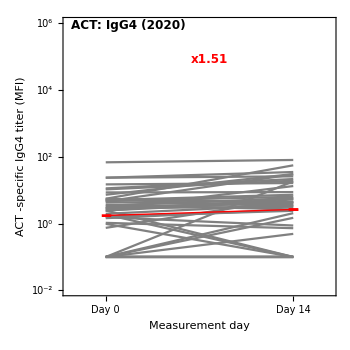
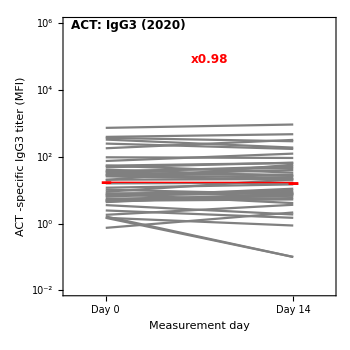
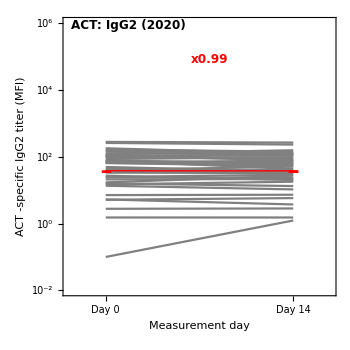
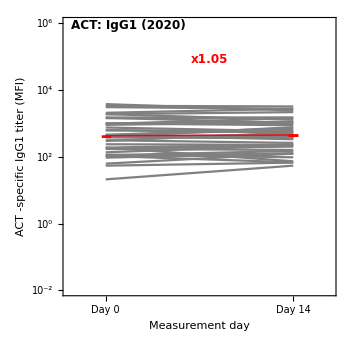
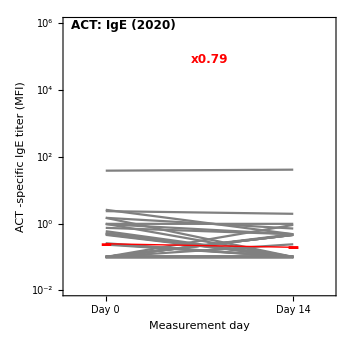
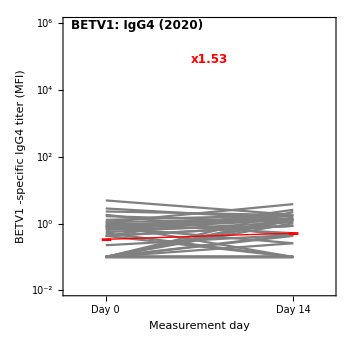
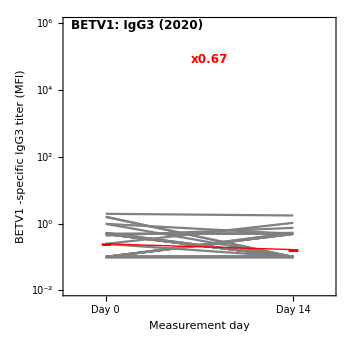
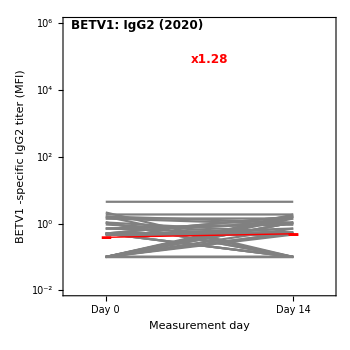
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
(* Looping through all Ags and all Isotypes *)

allAgs0={"PT"};
allAgs0=allAgs;

myFigALLAbs=
Table[
allIgGs=Union[Cases[data,x_?( #[[posAg]]==allAgs0[[Ag]]&):>x[[posIg]]]];
allIgGs=ReverseSort[allIgGs];
Table[
IgG=allIgGs[[igg]];
alldataIgG=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]==IgG && #[[posAg]]==allAgs0[[Ag]]&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];
tempdata1=
Table[
Ab0=MyRound[Last[Cases[alldataIgG[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgG[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab14=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];
tempdata2=Map[Transpose[{{1,2},#}]&,dataAb0Ab14];
tempdata3=AverageDataOne[Flatten[tempdata2,1]];
foldAb=10^(tempdata3[[2,2]]-tempdata3[[1,2]]);

Show[
MyListPlot[tempdata2,
Joined->True,
PlotMarkers->None,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-2,6}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-2,6,1}]},
FrameLabel->{"Measurement day",allAgs0[[Ag]]"-specific "<>IgG<>" titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{allAgs0[[Ag]]<>": "<>IgG<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"x"<>ToString[MyRound[foldAb,2]]},{0.42,0.85},FontColor->{Red}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
},
Options[MyListPlot]
],
MyListPlot[{tempdata3},
Joined->True,
PlotMarkers->Line,
PlotStyle->{{Red,Thick}}
]
]
,{igg,1,Length[allIgGs]}
]
,{Ag,1,Length[allAgs0]}
]
```

```mathematica
MyGraphicsArray0[myFigALLAbs];
```

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgALL-to-Ags-ALL-MFI-MFI-change-day0-14-ALL.pdf",%,"PDF"];
```

```mathematica
(* MFI: time course  *)

alldataIgG=alldataIgG1;

Table[
Ab0=MyRound[Last[Cases[alldataIgG[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgG[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
MyListPlot[{alldataIgG[[id]]},
PlotStyle->Gray,
PlotRange->{{tmin,tmax},{-0.5,3.2}},
FrameTicks->{myticks,logticks[{-1,6,1}]},
FrameLabel->{"days since PT vaccination",allAgs[[Ag]]<>"-specific IgG titer (MFI)"},
Epilog->{
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]},
mylegend2noS[{"ID="<>ToString[allIDs[[id]]]<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"Ab0="<>ToString[Ab0],"Ab14 = "<>ToString[Ab14]},{0.52,0.97}]
},
PlotMarkers->{symbols[[id]]},
Joined->True
],{id,1,Length[allIDs]}
]

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Monocyte dynamics

### 2020 data: IgG to PT

```mathematica
data1=Import[PicturesPath<>"/data/data-rearranged/subjects2020_antibodies.xlsx","XLSX"];
data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | subject_id
2 | specimen_id
3 | actual_day_relative_to_boost
4 | isotype
5 | is_antigen_specific
6 | antigen
7 | MFI
8 | MFI_normalised
9 | unit
10 | lower_limit_of_detection

```mathematica
posID=1;
posAg=6;
posIg=4;
posDay=3;
posMFI=7;
posMFIn=8;

allIDs=Union[Drop[data[[All,1]],1]];

tmin=Min[Drop[data[[All,posDay]],1]];
tmax=Max[Drop[data[[All,posDay]],1]];
```

```mathematica
(* total IgG *)

alldataIgGPT=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG" && #[[posAg]]=="PT"&):>{x[[posDay]],Log10[x[[posMFI]]]}],{id,1,Length[allIDs]}];

alldataIgGPTn=Table[
Cases[data,x_?(#[[posID]]==allIDs[[id]]&&#[[posIg]]=="IgG" && #[[posAg]]=="PT"&):>{x[[posDay]],Log10[x[[posMFIn]]]}],{id,1,Length[allIDs]}];
```

```mathematica
(* MFI *)

Table[
Ab0=MyRound[Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
MyListPlot[{alldataIgGPT[[id]]},
PlotStyle->Gray,
PlotRange->{{tmin,tmax},{-0.5,3.2}},
FrameTicks->{myticks,logticks[{-1,6,1}]},
FrameLabel->{"days since PT vaccination","PT-specific IgG titer (MFI)"},
Epilog->{
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]},
mylegend2noS[{"ID="<>ToString[allIDs[[id]]]<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"Ab0="<>ToString[Ab0],"Ab14 = "<>ToString[Ab14]},{0.52,0.97}]
},
PlotMarkers->{symbols[[id]]},
Joined->True
],{id,1,Length[allIDs]}
]

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI.pdf",%,"PDF"];
```

```mathematica
(* Day 0 Ab to Day 14 Ab: MFI *)

tempdata1=
Table[
Ab0=MyRound[Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPT[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab14=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];
tempdata2=Map[Transpose[{{1,2},#}]&,dataAb0Ab14];

tempdata10=
Table[
Ab0=MyRound[Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
{Ab0,Ab14},{id,1,Length[allIDs]}
];

dataAb0Ab140=Cases[tempdata10,x_?(VectorQ[#,NumericQ]&)];
tempdata20=Map[Transpose[{{1,2},#}]&,dataAb0Ab140];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
{
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,3.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[tempdata20,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-2.0,2.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-4,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (nMFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"normalized IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
]
}

MyGraphicsArray[%];
```

{-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI-nMFI-change-day0-14-2panels.pdf",%,"PDF"];
```

```mathematica
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,3.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG (2020)"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
]
```

-Graphics-

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-MFI-change-day0-14.pdf",%,"PDF"];
```

```mathematica
(* normalized MFI *)

Table[
Ab0=MyRound[Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]<0&)]][[2]],2];
Ab14=Last[Cases[alldataIgGPTn[[id]],x_?(#[[1]]==14&)]][[2]];
Ab14=If[NumericQ[Ab14],MyRound[Ab14,2],"NA"];
MyListPlot[{alldataIgGPTn[[id]]},
PlotStyle->Gray,
PlotRange->{{tmin,tmax},{-2,2.3}},
FrameTicks->{myticks,logticks[{-3,6,1}]},
FrameLabel->{"days since PT vaccination","PT-specific IgG titer (nMFI)"},
Epilog->{
{Dashed,Line[{{0,-2},{0,3}}]},
{Dashed,Red,Line[{{14,-2},{14,3}}]},
mylegend2noS[{"ID="<>ToString[allIDs[[id]]]<>" (2020)"},{-0.02,0.97}],
mylegend2noS[{"Ab0="<>ToString[Ab0],"Ab14 = "<>ToString[Ab14]},{0.52,0.97}]
},
PlotMarkers->{symbols[[id]]},
Joined->True
],{id,1,Length[allIDs]}
];

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 2 of Last[{}] does not exist.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Part::partw: Part 2 of Last[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export[PicturesPath<>"/figs/data-2020-subjects-IgG-to-PT-nMFI.pdf",%,"PDF"];
```

## Th1/Th2 polarization data

### Arranging the data: 2021-2022-2023

```mathematica
(* bonus task data *)

data1=Import[PicturesPath<>"/data/bonus_task_data/Th1(IFN-γ)_Th2(IL-5)_polarization_ratio.tsv","TSV"];

Transpose[{Range[Length[data1[[1]]]],data1[[1]]}]//TableForm
```

1 | specimen_id
2 | PT_P01579(IFNγ)/PT_P05113(IL5)
3 | dataset

```mathematica
posDataset=3;
posSpecimen=1;
datasets=Union[Drop[data1[[All,posDataset]],1]];
```

```mathematica
(* Run for one dataset/year *)

dataset=3;
Year=StringSplit[datasets[[dataset]],"_"][[1]]
specimens=Cases[data1, x_?(#[[posDataset]]==datasets[[dataset]]&):>x[[posSpecimen]]]


data2=If[dataset<3,
Import[PicturesPath<>"/data/raw_datasets/training_data/"<>ToString[Year]<>"LD_specimen.tsv","TSV"],
Import[PicturesPath<>"/data/raw_datasets/challenge_data/"<>ToString[Year]<>"BD_specimen.tsv","TSV"]
];
Transpose[{Range[Length[data2[[1]]]],data2[[1]]}]//TableForm

Flatten[
Table[
aa=Cases[data1, x_?(#[[posSpecimen]]==specimens[[specimen]]&):>x[[2]]];
Cases[data2, x_?(#[[posSpecimen]]==specimens[[specimen]]&):>{Year,x[[2]],x[[1]],x[[3]],x[[4]],aa[[1]]}],{specimen,1,Length[specimens]}],1]
```

2023

{962,965,966,973,976,977,1004,1006,1007,1014,1017,1018,1025,1028,1029,1036,1037,1038,1045,1048,1049,1074,1077,1078,1085,1088,1089,1096,1097,1098,1105,1107,1108,1115,1118,1119,1126,1129,1130,1137,1140,1141,1148,1151,1152,1162,1170,1173,1174,1181,1183,1184,1191,1194,1195,1202,1205,1206,1213,1216,1217,1224,1226,1227,1234,1237,1238,1245,1247,1248,1255,1257,1258,1265,1268,1269,1276,1278,1279,1286,1289,1290,1297,1299,1300,1307,1310,1311,1339,1342,1343,1350,1351,1352,940,942,943,955,956,957,984,986,987,994,996,997,1056,1057,1058,1318,1321,1322,1329,1331,1332,1370,1373,1374,1381,1384,1385,1392,1395,1396,1403,1406,1407,1414,1416,1417,1424,1426,1427,1434,1436,1437,1444,1446,1447,1454,1456,1457,1464,1466,1467,1474,1476,1477,1484,1486,1487,1494,1496,1497}

1 | specimen_id
2 | subject_id
3 | actual_day_relative_to_boost
4 | planned_day_relative_to_boost
5 | specimen_type
6 | visit

{{2023,129,962,-25,-30,0.283418},{2023,129,965,-13,-14,0.172344},{2023,129,966,0,0,0.101153},{2023,139,973,-25,-30,11.6529},{2023,139,976,-14,-14,0.406205},{2023,139,977,0,0,0.526893},{2023,141,1004,-28,-30,0.807485},{2023,141,1006,-14,-14,1.75873},{2023,141,1007,0,0,0.446358},{2023,123,1014,-31,-30,87.4212},{2023,123,1017,-17,-14,0.189518},{2023,123,1018,0,0,0.264075},{2023,136,1025,-14,-30,0.343502},{2023,136,1028,-8,-14,0.343502},{2023,136,1029,0,0,0.343502},{2023,130,1036,-18,-30,2.57626},{2023,130,1037,-6,-14,0.343502},{2023,130,1038,0,0,0.343502},{2023,120,1045,-54,-30,2.01445},{2023,120,1048,-34,-14,1.84818},{2023,120,1049,0,0,2.26686},{2023,121,1074,-24,-30,61.0287},{2023,121,1077,-12,-14,0.211572},{2023,121,1078,0,0,0.154875},{2023,122,1085,-18,-30,4.75183},{2023,122,1088,-11,-14,0.502663},{2023,122,1089,0,0,1.39419},{2023,127,1096,-26,-30,0.358552},{2023,127,1097,-12,-14,0.0436733},{2023,127,1098,0,0,0.0237464},{2023,124,1105,-31,-30,0.233581},{2023,124,1107,-17,-14,0.171898},{2023,124,1108,0,0,0.14894},{2023,125,1115,-31,-30,1.89411},{2023,125,1118,-17,-14,0.276621},{2023,125,1119,0,0,2.81164},{2023,126,1126,-27,-30,0.668652},{2023,126,1129,-13,-14,0.0229653},{2023,126,1130,0,0,0.0269039},{2023,128,1137,-45,-30,0.101389},{2023,128,1140,-6,-14,0.162678},{2023,128,1141,0,0,0.551918},{2023,135,1148,-75,-30,3.88804},{2023,135,1151,-67,-14,0.442668},{2023,135,1152,0,0,2.12881},{2023,131,1162,-14,-14,0.00880752},{2023,132,1170,-18,-30,0.132974},{2023,132,1173,-7,-14,0.0936865},{2023,132,1174,0,0,0.137401},{2023,133,1181,-26,-30,0.0560395},{2023,133,1183,-13,-14,0.0431963},{2023,133,1184,0,0,0.343502},{2023,134,1191,-20,-30,4.29377},{2023,134,1194,-11,-14,2.40451},{2023,134,1195,0,0,3.77619},{2023,137,1202,-14,-30,0.343502},{2023,137,1205,-7,-14,0.343502},{2023,137,1206,0,0,0.343502},{2023,149,1213,-29,-30,0.334806},{2023,149,1216,-15,-14,1.3928},{2023,149,1217,0,0,2.08188},{2023,138,1224,-31,-30,9.27455},{2023,138,1226,-14,-14,8.98824},{2023,138,1227,0,0,0.343502},{2023,143,1234,-35,-30,0.189308},{2023,143,1237,-13,-14,0.208206},{2023,143,1238,0,0,0.144276},{2023,140,1245,-28,-30,0.16544},{2023,140,1247,-14,-14,4.5222},{2023,140,1248,0,0,0.343502},{2023,150,1255,-33,-30,1.31676},{2023,150,1257,-13,-14,1.1003},{2023,150,1258,0,0,0.97274},{2023,142,1265,-38,-30,0.52799},{2023,142,1268,-14,-14,1.08721},{2023,142,1269,0,0,1.65218},{2023,144,1276,-33,-30,0.795704},{2023,144,1278,-14,-14,0.450848},{2023,144,1279,0,0,0.671117},{2023,145,1286,-32,-30,5.61053},{2023,145,1289,-13,-14,0.0710669},{2023,145,1290,0,0,2.28211},{2023,146,1297,-34,-30,0.708784},{2023,146,1299,-14,-14,65.9523},{2023,146,1300,0,0,5.1509},{2023,147,1307,-29,-30,0.220664},{2023,147,1310,-15,-14,0.343502},{2023,147,1311,0,0,0.94929},{2023,153,1339,-27,-30,0.966644},{2023,153,1342,-13,-14,0.509456},{2023,153,1343,0,0,0.589169},{2023,154,1350,-27,-30,0.654592},{2023,154,1351,-13,-14,0.485264},{2023,154,1352,0,0,0.533544},{2023,170,940,-32,-30,0.0282636},{2023,170,942,-14,-14,0.0405098},{2023,170,943,0,0,1.86581},{2023,172,955,-33,-30,0.0229404},{2023,172,956,-13,-14,0.00872684},{2023,172,957,0,0,1.07449},{2023,162,984,-25,-30,0.028485},{2023,162,986,-13,-14,0.00978992},{2023,162,987,0,0,0.00234363},{2023,119,994,-32,-30,0.00231204},{2023,119,996,-13,-14,0.00140329},{2023,119,997,0,0,0.0236803},{2023,160,1056,-32,-30,0.503206},{2023,160,1057,-14,-14,0.395659},{2023,160,1058,0,0,0.669954},{2023,151,1318,-26,-30,0.00414406},{2023,151,1321,-12,-14,0.010254},{2023,151,1322,0,0,0.482486},{2023,152,1329,-28,-30,0.348855},{2023,152,1331,-14,-14,1.99704},{2023,152,1332,0,0,2.9551},{2023,156,1370,-31,-30,0.0215782},{2023,156,1373,-13,-14,0.0388228},{2023,156,1374,0,0,0.0137201},{2023,157,1381,-27,-30,0.00355555},{2023,157,1384,-12,-14,0.0123344},{2023,157,1385,0,0,0.033046},{2023,158,1392,-27,-30,1.72768},{2023,158,1395,-10,-14,0.00420386},{2023,158,1396,0,0,0.00687447},{2023,159,1403,-25,-30,1.36852},{2023,159,1406,-13,-14,0.0086679},{2023,159,1407,0,0,2.16181},{2023,161,1414,-28,-30,0.141065},{2023,161,1416,-13,-14,0.104468},{2023,161,1417,0,0,0.151284},{2023,165,1424,-25,-30,0.00787509},{2023,165,1426,-11,-14,0.0105898},{2023,165,1427,0,0,1.95955},{2023,163,1434,-24,-30,0.00846974},{2023,163,1436,-10,-14,0.0111182},{2023,163,1437,0,0,0.027626},{2023,164,1444,-24,-30,0.533793},{2023,164,1446,-10,-14,0.371147},{2023,164,1447,0,0,1.41983},{2023,166,1454,-33,-30,0.0405954},{2023,166,1456,-15,-14,0.137289},{2023,166,1457,0,0,0.00592008},{2023,167,1464,-32,-30,0.00519344},{2023,167,1466,-13,-14,0.0109183},{2023,167,1467,0,0,0.00360947},{2023,168,1474,-32,-30,0.304877},{2023,168,1476,-13,-14,0.114863},{2023,168,1477,0,0,2.17957},{2023,169,1484,-32,-30,0.00377956},{2023,169,1486,-18,-14,0.00517733},{2023,169,1487,0,0,0.00350412},{2023,171,1494,-32,-30,0.100641},{2023,171,1496,-13,-14,0.36211},{2023,171,1497,0,0,0.925506}}

```mathematica
data2[[1]]
```

{specimen_id,subject_id,actual_day_relative_to_boost,planned_day_relative_to_boost,specimen_type,visit}

```mathematica
tab[[1,1]]
```

{2021,61,468,-4,0,0.0532278}

```mathematica
(* all years *)

tab=Table[
Year=StringSplit[datasets[[dataset]],"_"][[1]];
specimens=Cases[data1, x_?(#[[posDataset]]==datasets[[dataset]]&):>x[[posSpecimen]]];
data2=If[dataset<3,
Import[PicturesPath<>"/data/raw_datasets/training_data/"<>ToString[Year]<>"LD_specimen.tsv","TSV"],
Import[PicturesPath<>"/data/raw_datasets/challenge_data/"<>ToString[Year]<>"BD_specimen.tsv","TSV"]
];
Flatten[
Table[
aa=Cases[data1, x_?(#[[posSpecimen]]==specimens[[specimen]]&):>x[[2]]];
Cases[data2, x_?(#[[posSpecimen]]==specimens[[specimen]]&):>{Year,x[[2]],x[[1]],x[[3]],x[[4]],aa[[1]]}],{specimen,1,Length[specimens]}],1],{dataset,1,Length[datasets]}];

tab0=Prepend[Flatten[tab,1],{"year","subject_id","specimen_id","actual_day_relative_to_boost","planned_day_relative_to_boost","Th1/Th2 ratio"}];

tab0//TableForm;
```

```mathematica
Export[PicturesPath<>"/data/data-rearranged/data-bonus-task-Th1-Th2-polarization.csv",tab0,"CSV"];
```

{{61,468,-4,0,0.0532278},{61,473,30,30,13.8037},{62,475,0,0,0.137391},{62,480,30,30,0.328229},{66,506,0,0,9.83826},{66,511,31,30,16.7224},{67,513,0,0,0.574323},{67,518,30,30,0.0941055},{68,521,0,0,0.865605},{68,526,30,30,0.627644},{69,529,0,0,1.57022},{69,534,32,30,34.7843},{70,537,0,0,0.461307},{70,542,32,30,0.674209},{71,546,0,0,2.03152},{71,551,37,30,25.78},{72,554,0,0,1.42828},{72,559,29,30,1.53597},{73,562,0,0,15.0457},{73,567,37,30,1.84525},{74,569,0,0,4.08079},{74,574,29,30,12.9787},{77,593,0,0,0.498306},{77,598,31,30,0.552866},{78,601,0,0,0.598646},{78,606,31,30,0.823739},{79,608,0,0,1.62563},{79,613,31,30,0.766428},{80,616,0,0,0.000105124},{80,621,31,30,0.000327555},{81,623,0,0,4.07475},{81,628,36,30,0.455272},{82,630,0,0,7.83335},{82,635,32,30,1.08231},{84,643,0,0,0.264289},{84,648,28,30,0.547672},{86,657,0,0,0.0248393},{86,662,30,30,0.28133},{89,674,0,0,1.80974},{89,679,29,30,3.42433},{90,681,0,0,0.561501},{90,686,29,30,6.22469},{91,688,0,0,1.58117},{91,693,37,30,10.7786},{92,695,0,0,0.604019},{92,700,30,30,0.618107},{93,702,0,0,1.72817},{93,707,30,30,1.22474},{94,709,0,0,0.503446},{94,714,30,30,1.5307},{95,716,0,0,19.8983},{95,721,30,30,23.3315},{96,723,0,0,0.931486},{96,728,30,30,0.0626905}}

```mathematica
data3=Import[PicturesPath<>"/data/data-rearranged/data-bonus-task-Th1-Th2-polarization.csv","CSV"];

Transpose[{Range[Length[data3[[1]]]],data3[[1]]}]//TableForm
```

1 | year
2 | subject_id
3 | specimen_id
4 | actual_day_relative_to_boost
5 | planned_day_relative_to_boost
6 | Th1/Th2 ratio

```mathematica
posYear=1;
posSubject=2;
years=Union[Drop[data3[[All,posYear]],1]];

alldata=Table[
tempdata1=Cases[data3,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[Drop[tempdata1[[All,posSubject]],1]];
Table[
Cases[tempdata1,x_?(#[[posSubject]]==subjects0[[subject]]&):> {x[[4]],x[[6]]}],{subject,1,Length[subjects0]}],{year,1,Length[years]}];

subjectsALL=Table[
tempdata1=Cases[data3,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[Drop[tempdata1[[All,posSubject]],1]],{year,1,Length[years]}];
```

```mathematica
(* All plots *)

Table[
MyListPlot[ToLog[alldata[[year]]],
PlotRange->{{-50,40},{-4,2}},
FrameLabel->{"days since boost","Th1/Th2"},
FrameTicks->{myticks,logticks3[{-4,4,1}]},
Epilog->{
mylegend2noS[{years[[year]]},{0.01,0.97}],
{Dashed,Line[{{0,-4},{0,2}}]}
},
PlotStyle->{If[year<3,Gray,Red]},
Joined->True
],{year,1,Length[years]}]

MyGraphicsArray[%];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2021-2022-2023-subjects-Th1-Th2-kinetics.pdf",%,"PDF"];
```

2021

```mathematica
data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

Import::nffil: File /Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/data/data-rearranged/subjects2020_antibodies.xlsx not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{},$Failed} cannot be transposed.

Transpose[{{},$Failed}]

Modeling

## Predicting data: playing

### IgG to PT: 2020-2023 - comparison and basic model (predicting 2021 data using scaling from 2020 to 2021)

```mathematica
data1=Import[PicturesPath<>"/data/data-rearranged/master_igg_pt_monocyte_data_wNANs_2020_2023.xlsx","XLSX"];
data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | subject_id
2 | specimen_id
3 | year
4 | infancy_vac
5 | biological_sex
6 | ethnicity
7 | race
8 | date_of_boost
9 | age
10 | isotype
11 | antigen
12 | actual_day_relative_to_boost
13 | MFI
14 | MFI_normalised
15 | cell_type_name
16 | percent_live_cell

```mathematica
posYear=3;
years=Union[Drop[data[[All,posYear]],1]];

posAg=11;
Union[Drop[data[[All,posAg]],1]]
```

{NaN,PT}

```mathematica
posIg=10;
Union[Drop[data[[All,posIg]],1]]
```

{IgG,NaN}

```mathematica
posDay=12;
Drop[data[[All,posDay]],1];

posID=1;
posMFI=13;
posMFIn=14;
posMonocyte=16;
```

```mathematica
(* Selecting Day 0 and Day 14 Ab titers for different years *)

dataAb0Ab14years=
Table[
tempdata1=Cases[data,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[tempdata1[[All,posID]]];
Table[
tempdata2=Cases[tempdata1,x_?(#[[posID]]==subjects0[[ID]]&)];
{Last[Cases[tempdata2,x_?(#[[posDay]]≤0&):>x[[posMFI]]]],First[Cases[tempdata2,x_?(#[[posDay]]≥14&):>x[[posMFI]]]]},{ID,1,Length[subjects0]}],
{year,1,Length[years]}];


allIDs=
Table[
tempdata1=Cases[data,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[tempdata1[[All,posID]]],
{year,1,Length[years]}];
```

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
year=2;
tempdata0=Cases[dataAb0Ab14years[[year]],x_?(VectorQ[#,NumericQ]&):>Log10[x]]
```

{{2.05212,2.48287},{2.09674,3.1899},{2.44514,3.28255},{2.54802,2.74699},{1.92298,3.26429},{2.22981,3.31376},{1.85248,3.32806},{2.08439,3.19464},{2.095,3.06077},{1.638,2.30363},{2.86493,2.96235},{2.56437,3.23961},{2.48173,3.13024},{1.68973,2.58625},{1.16879,2.13434},{3.07755,3.09587},{1.84042,2.70458},{2.04922,2.91986},{2.65442,3.00828},{1.63599,2.39533},{2.4537,2.71328},{2.19852,2.63993},{1.38384,2.67665},{1.46613,2.22724},{1.42243,2.78902},{0.736193,2.12693},{1.4764,2.34626},{2.00731,2.68793},{1.30643,2.5772},{2.34976,2.80973},{2.77743,2.99728},{2.64512,3.0329},{1.89625,2.58659}}

```mathematica
SpearmanRho[tempdata0][[1,2]]
CorrelationTest[tempdata0]
```

0.635361

9.33647×10^-6

```mathematica
MyListPlot[{tempdata0}]
```

-Graphics-

```mathematica
MachineLearning
```

```mathematica
tempdata1=Table[
Map[Transpose[{{1,2},Log10[#]}]&,dataAb0Ab14years[[year]]],{year,1,Length[years]}];

Table[
tempdata2=tempdata1[[year]];
Show[
MyListPlot[tempdata2,
Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG: "<>years[[year]]},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[tempdata1[[4]],
PlotStyle->Red
],
MyListPlot[{AverageDataOne[Cases[Flatten[tempdata2,1],x_?(VectorQ[#,NumericQ]&)]]},
Joined->True,
PlotMarkers->Line
]
],
{year,1,Length[years]-1}]

MyGraphicsArray[%];
```

StringJoin::string: String expected at position 2 in IgG: <>2020..

StringJoin::string: String expected at position 2 in IgG: <>2021..

StringJoin::string: String expected at position 2 in IgG: <>2022..

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-2021-2022-IgG-to-PT-MFI-change-day0-14.pdf",%,"PDF"];
```

```mathematica
(* Cases of declining Abs *)

year=1;
tempdata3=Cases[dataAb0Ab14years[[year]],x_?(#[[2]]<#[[1]]&)]
```

{{182.935,168.901},{107.194,35.3689},{313.565,219.279}}

```mathematica
Table[
{Cases[data,x_?(#[[posMFI]]==tempdata3[[i,1]]&)],Cases[data,x_?(#[[posMFI]]==tempdata3[[i,2]]&)]},{i,1,Length[tempdata3]}]
```

{{{{17.,131.,2020_dataset,wP,Female,Hispanic or Latino,White,2016-09-12,44.,IgG,PT,-40.,182.935,9.97032,Monocytes,14.4574}},{{17.,135.,2020_dataset,wP,Female,Hispanic or Latino,White,2016-09-12,44.,IgG,PT,14.,168.901,9.20544,Monocytes,12.8998}}},{{{21.,160.,2020_dataset,wP,Male,Not Hispanic or Latino,White,2016-08-29,41.,IgG,PT,0.,107.194,5.8423,Monocytes,15.2266}},{{21.,164.,2020_dataset,wP,Male,Not Hispanic or Latino,White,2016-08-29,41.,IgG,PT,14.,35.3689,1.92767,Monocytes,26.0424}}},{{{53.,405.,2020_dataset,aP,Female,Hispanic or Latino,Unknown or Not Reported,2017-01-03,26.,IgG,PT,-28.,313.565,17.0899,,}},{{53.,409.,2020_dataset,aP,Female,Hispanic or Latino,Unknown or Not Reported,2017-01-03,26.,IgG,PT,14.,219.279,11.9512,,}}}}

```mathematica
(* scaling 2020 and 2022 data to 2021 data D0 values *)

meanD0=Table[
Mean[Log10[Cases[dataAb0Ab14years[[year]][[All,1]],x_?(NumericQ[#]&)]]],{year,1,4}]

deltaD0=meanD0-meanD0[[2]]

dataAb0Ab14yearsLogScaled=
Table[
Cases[Log10[dataAb0Ab14years[[year]]]-deltaD0[[year]],x_?(VectorQ[#,NumericQ]&)],{year,1,Length[years]}];
```

{1.21796,2.03368,4.1326,1.93378}

{-0.815717,0.,2.09893,-0.0998992}

```mathematica
tempdata1=Table[
Map[Transpose[{{1,2},#}]&,dataAb0Ab14yearsLogScaled[[year]]],{year,1,Length[years]}];

Table[
tempdata2=tempdata1[[year]];
Show[
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG: "<>years[[year]]<>"- scaled to 2021"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata2,1]]},
Joined->True,
PlotMarkers->Line
]
],
{year,1,Length[years]-1}]
MyGraphicsArray[%];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-2021-2022-IgG-to-PT-MFI-change-day0-14-scaled-to-2021.pdf",%,"PDF"];
```

```mathematica
(* generating predictions for 2021 using data for 2020 *)

year=2;
year2021day0=dataAb0Ab14yearsLogScaled[[year]][[All,1]]
year2021day14=dataAb0Ab14yearsLogScaled[[year]][[All,2]]
```

{2.05212,2.09674,2.44514,2.54802,1.92298,2.22981,1.85248,2.08439,2.095,1.638,2.86493,2.56437,2.48173,1.68973,1.16879,3.07755,1.84042,2.04922,2.65442,1.63599,2.4537,2.19852,1.38384,1.46613,1.42243,0.736193,1.4764,2.00731,1.30643,2.34976,2.77743,2.64512,1.89625}

{2.48287,3.1899,3.28255,2.74699,3.26429,3.31376,3.32806,3.19464,3.06077,2.30363,2.96235,3.23961,3.13024,2.58625,2.13434,3.09587,2.70458,2.91986,3.00828,2.39533,2.71328,2.63993,2.67665,2.22724,2.78902,2.12693,2.34626,2.68793,2.5772,2.80973,2.99728,3.0329,2.58659}

```mathematica
(* looking at the closest Ab titer at day 0, then looking at boosting and then increasing Ab titer for 2021 by that boost amount *)
year=1;
year2021day14predicted=Table[
tempdata1=Map[{(year2021day0[[id]]-#[[1]])^2,#[[1]],#[[2]]}&,dataAb0Ab14yearsLogScaled[[year]]];
tempdata2=Sort[tempdata1,#1[[1]]<#2[[1]]&];
(tempdata2[[1,3]]-tempdata2[[1,2]])+year2021day0[[id]],{id,1,Length[year2021day0]}];


(* simply taking value for 2020 Ab titer to 2021 value given closest value at day 0 *)

year2021day14predicted=Table[
tempdata1=Map[{(year2021day0[[id]]-#[[1]])^2,#[[1]],#[[2]]}&,dataAb0Ab14yearsLogScaled[[year]]];
tempdata2=Sort[tempdata1,#1[[1]]<#2[[1]]&];
tempdata2[[1,3]],{id,1,Length[year2021day0]}];
```

```mathematica
tempdata3={dataAb0Ab14yearsLogScaled[[2]],Transpose[{year2021day0,year2021day14predicted}]};
tempdata30=Table[
Map[Transpose[{{1,2},#}]&,tempdata3[[set]]],{set,1,Length[tempdata3]}];
```

```mathematica
Table[
tempdata2=tempdata30[[set]];
Show[
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{{"IgG: 2021 true data","IgG: 2021 predictions"}[[set]]},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata2,1]]},
Joined->True,
PlotMarkers->Line
]
],
{set,1,Length[tempdata30]}]

MyGraphicsArray[%];
```

{-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/model-IgG-to-PT-MFI-day14-scaling-2021-from-2020.pdf",%,"PDF"];
```

```mathematica
(* Plotting data and predictions per ID *)

allID2021=Cases[Transpose[Append[Transpose[dataAb0Ab14years[[2]]],allIDs[[2]]]],x_?(VectorQ[#,NumericQ]&):>x[[3]]];
tempdata4=Table[
{
Transpose[{{1,2},tempdata3[[1,set]]}],
Transpose[{{1,2},tempdata3[[2,set]]}]
},{set,1,Length[year2021day14predicted]}];

Table[
MyListPlot[tempdata4[[id]],
Joined->True,
PlotStyle->{Gray,Red},
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"ID="<>ToString[Round[allID2021[[id]]]]},{0.0,0.97}],
mylegend20[{"IgG 2021: data","IgG 2021: predictions"},{0.15,0.9,0.07,0},FontColor->{Gray,Red}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],{id,1,Length[tempdata4]}]

MyGraphicsArray0[Partition[%,UpTo[4]]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/model-IgG-to-PT-MFI-day14-scaling-2021-from-2020-perID.pdf",%,"PDF"];
```

```mathematica
tempdata2=Transpose[{year2021day14predicted,year2021day14}];
rho=SpearmanRho[tempdata2][[1,2]]
pval=CorrelationTest[tempdata2,0]

MyListPlot[{tempdata2},
PlotRange->{{2,4},{2,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{
"Model: 2020 IgG data to predict 2021 IgG",
"ρ="<>ToString[MyRound[rho,2]]<>" (p="<>ToString[MyRound[pval,2]]<>")"},
{0.02,0.97}, FontColor->Table[Black,{4}]
],
{Dashed,Line[{{0,00},{5,5}}]}
}
]
```

0.365401

0.0324167

-Graphics-

```mathematica
Export[PicturesPath<>"/figs/model-IgG-to-PT-MFI-day14-scaling-2021-from-2020-correlation.pdf",%,"PDF"];
```

### IgG to PT: 2020-2023 - comparison and basic model (predicting 2023 data using Abs from 2021 alone)

```mathematica
(* data1=Import[PicturesPath<>"/data/data-rearranged/master_igg_pt_monocyte_data_woutNANs_2020_2023.xlsx","XLSX"]; *)
data1=Import[PicturesPath<>"/data/data-rearranged/master_igg_pt_monocyte_data_wNANs_2020_2023.xlsx","XLSX"];

data=data1[[1]];

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | subject_id
2 | specimen_id
3 | year
4 | infancy_vac
5 | biological_sex
6 | ethnicity
7 | race
8 | date_of_boost
9 | age
10 | isotype
11 | antigen
12 | actual_day_relative_to_boost
13 | MFI
14 | MFI_normalised
15 | cell_type_name
16 | percent_live_cell

```mathematica
posYear=3;
years=Union[Drop[data[[All,posYear]],1]];

posAg=11;
Union[Drop[data[[All,posAg]],1]]
```

{NaN,PT}

```mathematica
posIg=10;
Union[Drop[data[[All,posIg]],1]]
```

{IgG,NaN}

```mathematica
posDay=12;
Drop[data[[All,posDay]],1];

posID=1;
posMFI=13;
posMFIn=14;
posMonocyte=16;
```

```mathematica
(* Selecting Day 0 and Day 14 Ab titers for different years *)

dataAb0Ab14years=
Table[
tempdata1=Cases[data,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[tempdata1[[All,posID]]];
Table[
tempdata2=Cases[tempdata1,x_?(#[[posID]]==subjects0[[ID]]&)];
{Last[Cases[tempdata2,x_?(#[[posDay]]≤0&):>x[[posMFI]]]],First[Cases[tempdata2,x_?(#[[posDay]]≥14&):>x[[posMFI]]]]},{ID,1,Length[subjects0]}],
{year,1,Length[years]}];


allIDs=
Table[
tempdata1=Cases[data,x_?(#[[posYear]]==years[[year]]&)];
subjects0=Union[tempdata1[[All,posID]]],
{year,1,Length[years]}];
```

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
tempdata1=Table[
Map[Transpose[{{1,2},Log10[#]}]&,dataAb0Ab14years[[year]]],{year,1,Length[years]}];

Table[
tempdata2=tempdata1[[year]];
Show[
MyListPlot[tempdata2,
Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG: "<>ToString[years[[year]]]<>" (n="<>ToString[Length[tempdata2]]<>")"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[tempdata1[[4]],
PlotStyle->Red
],
MyListPlot[{AverageDataOne[Flatten[tempdata1[[4]],1]]},
Joined->True,
PlotStyle->{Red},
PlotMarkers->Line
],
MyListPlot[{AverageDataOne[Cases[Flatten[tempdata2,1],x_?(VectorQ[#,NumericQ]&)]]},
Joined->True,
PlotMarkers->Line
]
],
{year,1,Length[years]-1}]

MyGraphicsArray[%];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-2021-2022-IgG-to-PT-MFI-change-day0-14.pdf",%,"PDF"];
```

```mathematica
(* scaling 2020 and 2022 data to 2023 data D0 values *)

meanD0=Table[
Mean[Log10[Cases[dataAb0Ab14years[[year]][[All,1]],x_?(NumericQ[#]&)]]],{year,1,4}]

deltaD0=meanD0-meanD0[[4]]

dataAb0Ab14yearsLogScaled=
Table[
Cases[Log10[dataAb0Ab14years[[year]]]-deltaD0[[year]],x_?(VectorQ[#,NumericQ]&)],{year,1,Length[years]}];

dataAb0Ab14yearsLogScaled0=
Table[
Log10[dataAb0Ab14years[[year]]]-deltaD0[[year]],{year,1,Length[years]}];
```

{1.21796,2.03368,4.1326,1.93378}

{-0.715818,0.0998992,2.19883,0.}

```mathematica
tempdata1=Table[
Map[Transpose[{{1,2},#}]&,dataAb0Ab14yearsLogScaled[[year]]],{year,1,Length[years]}];

tempdata10=Table[
Map[Transpose[{{1,2},#}]&,dataAb0Ab14yearsLogScaled0[[year]]],{year,1,Length[years]}];

Table[
tempdata2=tempdata1[[year]];
Show[
MyListPlot[tempdata2,Joined->True,
PlotStyle->Gray,
PlotRange->{{0.8,2.2},{-1,5.0}},
FrameTicks->{Table[{i,If[i==1,"Day 0",If[i==2,"Day 14",""]],{0.02,0}},{i,0,3}],logticks[{-1,6,1}]},
FrameLabel->{"Measurement day","PT-specific IgG titer (MFI)"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[{"IgG: "<>years[[year]]<>"- scaled to 2023"},{-0.02,0.97}],
{Dashed,Line[{{0,-1},{0,3}}]},
{Dashed,Red,Line[{{14,-1},{14,3}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata2,1]]},
Joined->True,
PlotMarkers->Line
],
MyListPlot[tempdata10[[4]],
PlotStyle->Red
],
MyListPlot[{AverageDataOne[Flatten[tempdata10[[4]],1]]},
Joined->True,
PlotStyle->{Red},
PlotMarkers->Line
]
],
{year,1,Length[years]-1}]
MyGraphicsArray[%];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[PicturesPath<>"/figs/data-2020-2021-2022-IgG-to-PT-MFI-change-day0-14-scaled-to-2023.pdf",%,"PDF"];
```

```mathematica
(* generating predictions for 2023 using data for 2021 *)

year=4;
years[[year]]
year2023day0=dataAb0Ab14yearsLogScaled0[[year]][[All,1]]
allID2024=allIDs[[year]]
nd23=Length[%]
```

2023_dataset

{2.14768,2.04727,1.73239,2.14145,2.21551,1.65801,1.87506,1.86776,1.6902,1.92169,1.72016,1.93702,1.66745,2.04922,1.93576,1.51851,1.64345,1.72632,1.72835,1.99123,1.71181,1.73239,1.85431,1.49831,1.93323,2.92117,1.43136,3.00615,2.43775,1.8907,2.49624,2.15381,1.52827,2.05019,1.77085,1.53782,1.92428,2.25648,2.09604,2.25768,1.88366,2.68417,2.03941,1.96731,1.38917,2.15761,1.97081,1.78533,1.44716,2.32377,1.68124,1.80277,1.73239,1.85582}

{119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.}

54

```mathematica
(* simply taking value for 2020 Ab titer to 2021 value given closest value at day 0 *)
year=2;

year2023day14predicted=Table[
tempdata1=Map[{(year2023day0[[id]]-#[[1]])^2,#[[1]],#[[2]]}&,dataAb0Ab14yearsLogScaled[[year]]];
tempdata2=Sort[tempdata1,#1[[1]]<#2[[1]]&];
tempdata2[[1,3]],{id,1,Length[year2023day0]}];

(* Fold increase predicted *)

year2023day14predictedFold=Table[
tempdata1=Map[{(year2023day0[[id]]-#[[1]])^2,10^(#[[2]]-#[[1]])}&,dataAb0Ab14yearsLogScaled[[year]]];
tempdata2=Sort[tempdata1,#1[[1]]<#2[[1]]&];
tempdata2[[1,2]],{id,1,Length[year2023day0]}]
```

{12.1325,12.3924,7.31408,12.1325,2.8838,7.87983,4.79311,4.79311,7.31408,4.79311,7.31408,7.42411,7.31408,2.76322,7.42411,5.74566,7.87983,7.31408,7.31408,9.24226,7.31408,7.31408,21.9433,5.74566,7.42411,1.04308,7.41067,1.04308,1.58111,4.79311,4.73415,12.1325,5.74566,2.76322,29.8939,4.6305,4.79311,2.8838,2.76322,2.8838,4.79311,1.65902,12.3924,2.69623,7.41067,12.1325,12.8899,4.90159,7.41067,6.87726,7.31408,4.90159,7.31408,21.9433}

```mathematica
tempdata3=Transpose[{allID2024,10^year2023day14predicted,year2023day14predictedFold}]
```

{{119.,1636.3,12.1325},{120.,1230.26,12.3924},{121.,402.421,7.31408},{122.,1636.3,12.1325},{123.,512.659,2.8838},{124.,306.441,7.87983},{125.,387.283,4.79311},{126.,387.283,4.79311},{127.,402.421,7.31408},{128.,387.283,4.79311},{129.,402.421,7.31408},{130.,660.637,7.42411},{131.,402.421,7.31408},{132.,346.765,2.76322},{133.,660.637,7.42411},{134.,197.436,5.74566},{135.,306.441,7.87983},{136.,402.421,7.31408},{137.,402.421,7.31408},{138.,913.848,9.24226},{139.,402.421,7.31408},{140.,402.421,7.31408},{141.,1460.12,21.9433},{142.,197.436,5.74566},{143.,660.637,7.42411},{144.,990.757,1.04308},{145.,176.342,7.41067},{146.,990.757,1.04308},{147.,443.697,1.58111},{148.,387.283,4.79311},{149.,1379.47,4.73415},{150.,1636.3,12.1325},{151.,197.436,5.74566},{152.,346.765,2.76322},{153.,1691.08,29.8939},{154.,159.857,4.6305},{155.,387.283,4.79311},{156.,512.659,2.8838},{157.,346.765,2.76322},{158.,512.659,2.8838},{159.,387.283,4.79311},{160.,789.547,1.65902},{161.,1230.26,12.3924},{162.,241.532,2.69623},{163.,176.342,7.41067},{164.,1636.3,12.1325},{165.,1243.77,12.8899},{166.,306.682,4.90159},{167.,176.342,7.41067},{168.,1522.84,6.87726},{169.,402.421,7.31408},{170.,306.682,4.90159},{171.,402.421,7.31408},{172.,1460.12,21.9433}}

```mathematica
tempdata4=Transpose[Append[Transpose[Sort[Transpose[Append[Transpose[Sort[tempdata3,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[3]]>#2[[3]]&]],Range[nd23]]]
tempdata40=Sort[tempdata4,#1[[1]]<#2[[1]]&];
```

{{153.,1691.08,29.8939,1,1},{141.,1460.12,21.9433,8,2},{172.,1460.12,21.9433,7,3},{165.,1243.77,12.8899,10,4},{120.,1230.26,12.3924,12,5},{161.,1230.26,12.3924,11,6},{119.,1636.3,12.1325,5,7},{122.,1636.3,12.1325,4,8},{150.,1636.3,12.1325,3,9},{164.,1636.3,12.1325,2,10},{138.,913.848,9.24226,15,11},{124.,306.441,7.87983,46,12},{135.,306.441,7.87983,45,13},{130.,660.637,7.42411,19,14},{133.,660.637,7.42411,18,15},{143.,660.637,7.42411,17,16},{145.,176.342,7.41067,53,17},{163.,176.342,7.41067,52,18},{167.,176.342,7.41067,51,19},{121.,402.421,7.31408,33,20},{127.,402.421,7.31408,32,21},{129.,402.421,7.31408,31,22},{131.,402.421,7.31408,30,23},{136.,402.421,7.31408,29,24},{137.,402.421,7.31408,28,25},{139.,402.421,7.31408,27,26},{140.,402.421,7.31408,26,27},{169.,402.421,7.31408,25,28},{171.,402.421,7.31408,24,29},{168.,1522.84,6.87726,6,30},{134.,197.436,5.74566,50,31},{142.,197.436,5.74566,49,32},{151.,197.436,5.74566,48,33},{166.,306.682,4.90159,44,34},{170.,306.682,4.90159,43,35},{125.,387.283,4.79311,39,36},{126.,387.283,4.79311,38,37},{128.,387.283,4.79311,37,38},{148.,387.283,4.79311,36,39},{155.,387.283,4.79311,35,40},{159.,387.283,4.79311,34,41},{149.,1379.47,4.73415,9,42},{154.,159.857,4.6305,54,43},{123.,512.659,2.8838,22,44},{156.,512.659,2.8838,21,45},{158.,512.659,2.8838,20,46},{132.,346.765,2.76322,42,47},{152.,346.765,2.76322,41,48},{157.,346.765,2.76322,40,49},{162.,241.532,2.69623,47,50},{160.,789.547,1.65902,16,51},{147.,443.697,1.58111,23,52},{144.,990.757,1.04308,14,53},{146.,990.757,1.04308,13,54}}

```mathematica
tempdata5=Prepend[tempdata40,{"subject_id","IgG MFI day 14","Fold change MFI day 14","Rank IgG MFI","Rank Fold Change IgG MFI day 14"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Fold change MFI day 14 | Rank IgG MFI | Rank Fold Change IgG MFI day 14
119. | 1636.3 | 12.1325 | 5 | 7
120. | 1230.26 | 12.3924 | 12 | 5
121. | 402.421 | 7.31408 | 33 | 20
122. | 1636.3 | 12.1325 | 4 | 8
123. | 512.659 | 2.8838 | 22 | 44
124. | 306.441 | 7.87983 | 46 | 12
125. | 387.283 | 4.79311 | 39 | 36
126. | 387.283 | 4.79311 | 38 | 37
127. | 402.421 | 7.31408 | 32 | 21
128. | 387.283 | 4.79311 | 37 | 38
129. | 402.421 | 7.31408 | 31 | 22
130. | 660.637 | 7.42411 | 19 | 14
131. | 402.421 | 7.31408 | 30 | 23
132. | 346.765 | 2.76322 | 42 | 47
133. | 660.637 | 7.42411 | 18 | 15
134. | 197.436 | 5.74566 | 50 | 31
135. | 306.441 | 7.87983 | 45 | 13
136. | 402.421 | 7.31408 | 29 | 24
137. | 402.421 | 7.31408 | 28 | 25
138. | 913.848 | 9.24226 | 15 | 11
139. | 402.421 | 7.31408 | 27 | 26
140. | 402.421 | 7.31408 | 26 | 27
141. | 1460.12 | 21.9433 | 8 | 2
142. | 197.436 | 5.74566 | 49 | 32
143. | 660.637 | 7.42411 | 17 | 16
144. | 990.757 | 1.04308 | 14 | 53
145. | 176.342 | 7.41067 | 53 | 17
146. | 990.757 | 1.04308 | 13 | 54
147. | 443.697 | 1.58111 | 23 | 52
148. | 387.283 | 4.79311 | 36 | 39
149. | 1379.47 | 4.73415 | 9 | 42
150. | 1636.3 | 12.1325 | 3 | 9
151. | 197.436 | 5.74566 | 48 | 33
152. | 346.765 | 2.76322 | 41 | 48
153. | 1691.08 | 29.8939 | 1 | 1
154. | 159.857 | 4.6305 | 54 | 43
155. | 387.283 | 4.79311 | 35 | 40
156. | 512.659 | 2.8838 | 21 | 45
157. | 346.765 | 2.76322 | 40 | 49
158. | 512.659 | 2.8838 | 20 | 46
159. | 387.283 | 4.79311 | 34 | 41
160. | 789.547 | 1.65902 | 16 | 51
161. | 1230.26 | 12.3924 | 11 | 6
162. | 241.532 | 2.69623 | 47 | 50
163. | 176.342 | 7.41067 | 52 | 18
164. | 1636.3 | 12.1325 | 2 | 10
165. | 1243.77 | 12.8899 | 10 | 4
166. | 306.682 | 4.90159 | 44 | 34
167. | 176.342 | 7.41067 | 51 | 19
168. | 1522.84 | 6.87726 | 6 | 30
169. | 402.421 | 7.31408 | 25 | 28
170. | 306.682 | 4.90159 | 43 | 35
171. | 402.421 | 7.31408 | 24 | 29
172. | 1460.12 | 21.9433 | 7 | 3

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-scaling-2023-from-2021-ranking-ver1.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-scaling-2023-from-2021-ranking-ver1.tsv

### IgG to PT/Monocytes: 2020-2023 - rearranging the data

```mathematica
data1=Import[PicturesPath<>"/data-local/train_master_no_gene_v2.csv","CSV"];
data=data1;

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | 
2 | specimen_id
3 | subject_id
4 | actual_day_relative_to_boost
5 | planned_day_relative_to_boost
6 | specimen_type
7 | visit
8 | infancy_vac
9 | biological_sex
10 | ethnicity
11 | race
12 | year_of_birth
13 | date_of_boost
14 | dataset
15 | A6NI73_concentration
16 | NT-proBNP_concentration
17 | O00161_concentration
18 | O00182_concentration
19 | O00273_concentration
20 | O14625_concentration
21 | O14867_concentration
22 | O15123_concentration
23 | O43240_concentration
24 | O43508_concentration
25 | O43557_concentration
26 | O43597_concentration
27 | O43736_concentration
28 | O43827_concentration
29 | O43927_concentration
30 | O60449_concentration
31 | O60880_concentration
32 | O75144_concentration
33 | O75356_concentration
34 | O75475_concentration
35 | O75509_concentration
36 | O75791_concentration
37 | O76036_concentration
38 | O94992_concentration
39 | O95502_concentration
40 | O95544_concentration
41 | O95727_concentration
42 | O95760_concentration
43 | O95786_concentration
44 | O95841_concentration
45 | P00352_concentration
46 | P00813_concentration
47 | P01127_concentration
48 | P01133_concentration
49 | P01137_concentration
50 | P01222_concentration
51 | P01375_concentration
52 | P01574_concentration
53 | P01579_concentration
54 | P01583_concentration
55 | P01730_concentration
56 | P01732_concentration
57 | P02778_concentration
58 | P05089_concentration
59 | P05112_concentration
60 | P05113_concentration
61 | P05231_concentration
62 | P05412_concentration
63 | P06127_concentration
64 | P07585_concentration
65 | P08727_concentration
66 | P09038_concentration
67 | P09104_concentration
68 | P09237_concentration
69 | P09341_concentration
70 | P09382_concentration
71 | P09417_concentration
72 | P09467_concentration
73 | P09525_concentration
74 | P09601_concentration
75 | P09603_concentration
76 | P09668_concentration
77 | P10144_concentration
78 | P10145_concentration
79 | P10147_concentration
80 | P10747_concentration
81 | P12544_concentration
82 | P12724_concentration
83 | P13232_concentration
84 | P13236_concentration
85 | P13500_concentration
86 | P13611_concentration
87 | P14210_concentration
88 | P14317_concentration
89 | P15514_concentration
90 | P15692_concentration
91 | P16083_concentration
92 | P16278_concentration
93 | P16455_concentration
94 | P18564_concentration
95 | P18627_concentration
96 | P19022_concentration
97 | P19474_concentration
98 | P19971_concentration
99 | P20711_concentration
100 | P20718_concentration
101 | P21246_concentration
102 | P21964_concentration
103 | P22301_concentration
104 | P22466_concentration
105 | P23229_concentration
106 | P23526_concentration
107 | P25815_concentration
108 | P25942_concentration
109 | P26010_concentration
110 | P26842_concentration
111 | P27540_concentration
112 | P27695_concentration
113 | P28845_concentration
114 | P29017_concentration
115 | P29459,P29460_concentration
116 | P29474_concentration
117 | P29965_concentration
118 | P30044_concentration
119 | P30048_concentration
120 | P31431_concentration
121 | P32970_concentration
122 | P34130_concentration
123 | P35225_concentration
124 | P35237_concentration
125 | P35240_concentration
126 | P35754_concentration
127 | P35968_concentration
128 | P39900_concentration
129 | P40259_concentration
130 | P40818_concentration
131 | P41236_concentration
132 | P42701_concentration
133 | P42830_concentration
134 | P43234_concentration
135 | P43489_concentration
136 | P46109_concentration
137 | P46379_concentration
138 | P48023_concentration
139 | P48061_concentration
140 | P48740_concentration
141 | P49763_concentration
142 | P49767_concentration
143 | P50135_concentration
144 | P50452_concentration
145 | P50591_concentration
146 | P50995_concentration
147 | P51617_concentration
148 | P51671_concentration
149 | P51693_concentration
150 | P51858_concentration
151 | P52294_concentration
152 | P52823_concentration
153 | P52888_concentration
154 | P55773_concentration
155 | P58499_concentration
156 | P60568_concentration
157 | P63241_concentration
158 | P78310_concentration
159 | P78362_concentration
160 | P78410_concentration
161 | P78423_concentration
162 | P78556_concentration
163 | P80075_concentration
164 | P80098_concentration
165 | P98082_concentration
166 | Q00978_concentration
167 | Q01151_concentration
168 | Q01973_concentration
169 | Q02763_concentration
170 | Q02790_concentration
171 | Q03403_concentration
172 | Q03431_concentration
173 | Q04637_concentration
174 | Q04759_concentration
175 | Q04900_concentration
176 | Q05084_concentration
177 | Q05516_concentration
178 | Q06418_concentration
179 | Q06830_concentration
180 | Q07011_concentration
181 | Q07065_concentration
182 | Q07325_concentration
183 | Q12933_concentration
184 | Q12968_concentration
185 | Q13241_concentration
186 | Q13275_concentration
187 | Q13490_concentration
188 | Q13574_concentration
189 | Q14116_concentration
190 | Q14203_concentration
191 | Q14213,P29459_concentration
192 | Q14435_concentration
193 | Q14790_concentration
194 | Q15116_concentration
195 | Q15155_concentration
196 | Q15389_concentration
197 | Q15517_concentration
198 | Q15661_concentration
199 | Q15846_concentration
200 | Q16773_concentration
201 | Q16790_concentration
202 | Q16820_concentration
203 | Q29983,Q29980_concentration
204 | Q641Q3_concentration
205 | Q6DN72_concentration
206 | Q6EIG7_concentration
207 | Q6UWV6_concentration
208 | Q6UXB4_concentration
209 | Q6WN34_concentration
210 | Q6ZUJ8_concentration
211 | Q76M96_concentration
212 | Q7Z6M3_concentration
213 | Q86VZ4_concentration
214 | Q8IU57_concentration
215 | Q8IZP9_concentration
216 | Q8N1Q1_concentration
217 | Q8N608_concentration
218 | Q8NBJ7_concentration
219 | Q8NBS9_concentration
220 | Q8NHJ6_concentration
221 | Q8NI22_concentration
222 | Q8WTT0_concentration
223 | Q8WTU2_concentration
224 | Q8WVQ1_concentration
225 | Q8WX77_concentration
226 | Q8WXI8_concentration
227 | Q92520_concentration
228 | Q92583_concentration
229 | Q92692_concentration
230 | Q92844_concentration
231 | Q96DB9_concentration
232 | Q96JA1_concentration
233 | Q96LA6_concentration
234 | Q96P31_concentration
235 | Q96PD2_concentration
236 | Q96SB3_concentration
237 | Q99616_concentration
238 | Q99731_concentration
239 | Q9BQ51_concentration
240 | Q9BQB4_concentration
241 | Q9BXN2_concentration
242 | Q9BYZ8_concentration
243 | Q9BZR6_concentration
244 | Q9BZW8_concentration
245 | Q9C035_concentration
246 | Q9GZM7_concentration
247 | Q9GZT9_concentration
248 | Q9H4D0_concentration
249 | Q9H6B4_concentration
250 | Q9HBB8_concentration
251 | Q9HBE4_concentration
252 | Q9HCM2_concentration
253 | Q9NP84_concentration
254 | Q9NP99_concentration
255 | Q9NPH0_concentration
256 | Q9NQX5_concentration
257 | Q9NR28_concentration
258 | Q9NWQ8_concentration
259 | Q9NWZ3_concentration
260 | Q9NY25_concentration
261 | Q9NZQ7_concentration
262 | Q9UBU3_concentration
263 | Q9UHC6_concentration
264 | Q9UHL4_concentration
265 | Q9UHX3_concentration
266 | Q9UKJ0_concentration
267 | Q9UKX5_concentration
268 | Q9UMR7_concentration
269 | Q9UN19_concentration
270 | Q9UNE0_concentration
271 | Q9UQQ2_concentration
272 | Q9UQV4_concentration
273 | Q9Y286_concentration
274 | Q9Y2J8_concentration
275 | Q9Y3P8_concentration
276 | Q9Y5K6_concentration
277 | Q9Y653_concentration
278 | IgG_PT_MFI
279 | IgG_PRN_MFI
280 | IgG_FHA_MFI
281 | IgE_ACT_MFI
282 | IgE_LOS_MFI
283 | IgE_FELD1_MFI
284 | IgE_BETV1_MFI
285 | IgE_LOLP1_MFI
286 | IgE_Measles_MFI
287 | IgE_PTM_MFI
288 | IgE_PT_MFI
289 | IgE_PRN_MFI
290 | IgE_FHA_MFI
291 | IgE_FIM2/3_MFI
292 | IgE_TT_MFI
293 | IgE_DT_MFI
294 | IgE_OVA_MFI
295 | IgE_PD1_MFI
296 | IgG1_ACT_MFI
297 | IgG1_LOS_MFI
298 | IgG1_FELD1_MFI
299 | IgG1_BETV1_MFI
300 | IgG1_LOLP1_MFI
301 | IgG1_Measles_MFI
302 | IgG1_PTM_MFI
303 | IgG1_PT_MFI
304 | IgG1_PRN_MFI
305 | IgG1_FHA_MFI
306 | IgG1_FIM2/3_MFI
307 | IgG1_TT_MFI
308 | IgG1_DT_MFI
309 | IgG1_OVA_MFI
310 | IgG1_PD1_MFI
311 | IgG2_ACT_MFI
312 | IgG2_LOS_MFI
313 | IgG2_FELD1_MFI
314 | IgG2_BETV1_MFI
315 | IgG2_LOLP1_MFI
316 | IgG2_Measles_MFI
317 | IgG2_PTM_MFI
318 | IgG2_PT_MFI
319 | IgG2_PRN_MFI
320 | IgG2_FHA_MFI
321 | IgG2_FIM2/3_MFI
322 | IgG2_TT_MFI
323 | IgG2_DT_MFI
324 | IgG2_OVA_MFI
325 | IgG2_PD1_MFI
326 | IgG3_ACT_MFI
327 | IgG3_LOS_MFI
328 | IgG3_FELD1_MFI
329 | IgG3_BETV1_MFI
330 | IgG3_LOLP1_MFI
331 | IgG3_Measles_MFI
332 | IgG3_PTM_MFI
333 | IgG3_PT_MFI
334 | IgG3_PRN_MFI
335 | IgG3_FHA_MFI
336 | IgG3_FIM2/3_MFI
337 | IgG3_TT_MFI
338 | IgG3_DT_MFI
339 | IgG3_OVA_MFI
340 | IgG3_PD1_MFI
341 | IgG4_ACT_MFI
342 | IgG4_LOS_MFI
343 | IgG4_FELD1_MFI
344 | IgG4_BETV1_MFI
345 | IgG4_LOLP1_MFI
346 | IgG4_Measles_MFI
347 | IgG4_PTM_MFI
348 | IgG4_PT_MFI
349 | IgG4_PRN_MFI
350 | IgG4_FHA_MFI
351 | IgG4_FIM2/3_MFI
352 | IgG4_TT_MFI
353 | IgG4_DT_MFI
354 | IgG4_OVA_MFI
355 | IgG4_PD1_MFI
356 | IgG_PT_MFI_normalised
357 | IgG_PRN_MFI_normalised
358 | IgG_FHA_MFI_normalised
359 | IgE_ACT_MFI_normalised
360 | IgE_LOS_MFI_normalised
361 | IgE_FELD1_MFI_normalised
362 | IgE_BETV1_MFI_normalised
363 | IgE_LOLP1_MFI_normalised
364 | IgE_Measles_MFI_normalised
365 | IgE_PTM_MFI_normalised
366 | IgE_PT_MFI_normalised
367 | IgE_PRN_MFI_normalised
368 | IgE_FHA_MFI_normalised
369 | IgE_FIM2/3_MFI_normalised
370 | IgE_TT_MFI_normalised
371 | IgE_DT_MFI_normalised
372 | IgE_OVA_MFI_normalised
373 | IgE_PD1_MFI_normalised
374 | IgG1_ACT_MFI_normalised
375 | IgG1_LOS_MFI_normalised
376 | IgG1_FELD1_MFI_normalised
377 | IgG1_BETV1_MFI_normalised
378 | IgG1_LOLP1_MFI_normalised
379 | IgG1_Measles_MFI_normalised
380 | IgG1_PTM_MFI_normalised
381 | IgG1_PT_MFI_normalised
382 | IgG1_PRN_MFI_normalised
383 | IgG1_FHA_MFI_normalised
384 | IgG1_FIM2/3_MFI_normalised
385 | IgG1_TT_MFI_normalised
386 | IgG1_DT_MFI_normalised
387 | IgG1_OVA_MFI_normalised
388 | IgG1_PD1_MFI_normalised
389 | IgG2_ACT_MFI_normalised
390 | IgG2_LOS_MFI_normalised
391 | IgG2_FELD1_MFI_normalised
392 | IgG2_BETV1_MFI_normalised
393 | IgG2_LOLP1_MFI_normalised
394 | IgG2_Measles_MFI_normalised
395 | IgG2_PTM_MFI_normalised
396 | IgG2_PT_MFI_normalised
397 | IgG2_PRN_MFI_normalised
398 | IgG2_FHA_MFI_normalised
399 | IgG2_FIM2/3_MFI_normalised
400 | IgG2_TT_MFI_normalised
401 | IgG2_DT_MFI_normalised
402 | IgG2_OVA_MFI_normalised
403 | IgG2_PD1_MFI_normalised
404 | IgG3_ACT_MFI_normalised
405 | IgG3_LOS_MFI_normalised
406 | IgG3_FELD1_MFI_normalised
407 | IgG3_BETV1_MFI_normalised
408 | IgG3_LOLP1_MFI_normalised
409 | IgG3_Measles_MFI_normalised
410 | IgG3_PTM_MFI_normalised
411 | IgG3_PT_MFI_normalised
412 | IgG3_PRN_MFI_normalised
413 | IgG3_FHA_MFI_normalised
414 | IgG3_FIM2/3_MFI_normalised
415 | IgG3_TT_MFI_normalised
416 | IgG3_DT_MFI_normalised
417 | IgG3_OVA_MFI_normalised
418 | IgG3_PD1_MFI_normalised
419 | IgG4_ACT_MFI_normalised
420 | IgG4_LOS_MFI_normalised
421 | IgG4_FELD1_MFI_normalised
422 | IgG4_BETV1_MFI_normalised
423 | IgG4_LOLP1_MFI_normalised
424 | IgG4_Measles_MFI_normalised
425 | IgG4_PTM_MFI_normalised
426 | IgG4_PT_MFI_normalised
427 | IgG4_PRN_MFI_normalised
428 | IgG4_FHA_MFI_normalised
429 | IgG4_FIM2/3_MFI_normalised
430 | IgG4_TT_MFI_normalised
431 | IgG4_DT_MFI_normalised
432 | IgG4_OVA_MFI_normalised
433 | IgG4_PD1_MFI_normalised
434 | ASCs (Plasmablasts)_percent_live_cell
435 | Basophils_percent_live_cell
436 | Bcells_percent_live_cell
437 | CD3 Tcells_percent_live_cell
438 | CD33HLADR_percent_live_cell
439 | CD3CD19_percent_live_cell
440 | CD3CD19neg_percent_live_cell
441 | CD4Tcells_percent_live_cell
442 | CD8Tcells_percent_live_cell
443 | Classical_Monocytes_percent_live_cell
444 | Intermediate_Monocytes_percent_live_cell
445 | Monocytes_percent_live_cell
446 | NK_percent_live_cell
447 | NaiveCD4_percent_live_cell
448 | NaiveCD8_percent_live_cell
449 | Non-Classical_Monocytes_percent_live_cell
450 | TcmCD4_percent_live_cell
451 | TcmCD8_percent_live_cell
452 | TemCD4_percent_live_cell
453 | TemCD8_percent_live_cell
454 | TemraCD4_percent_live_cell
455 | TemraCD8_percent_live_cell
456 | Tregs_percent_live_cell
457 | mDC_percent_live_cell
458 | pDC_percent_live_cell
459 | P01135_concentration
460 | P01374_concentration
461 | P01584_concentration
462 | P03956_concentration
463 | P04141_concentration
464 | P09919_concentration
465 | P13725_concentration
466 | P40933_concentration
467 | P49771_concentration
468 | P78380_concentration
469 | Q16552_concentration
470 | Q8NEV9_Q14213_concentration
471 | Q969D9_concentration
472 | Q96PD4_concentration
473 | Q9P0M4_concentration
474 | IgG_DT_MFI
475 | IgG_FIM2/3_MFI
476 | IgG_OVA_MFI
477 | IgG_TT_MFI
478 | IgG_DT_MFI_normalised
479 | IgG_FIM2/3_MFI_normalised
480 | IgG_OVA_MFI_normalised
481 | IgG_TT_MFI_normalised
482 | Activated B cells (ABCs)_percent_live_cell
483 | Activated granulocytes_percent_live_cell
484 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell
485 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell
486 | B:NK doublets (CD19+CD3-CD14-CD56+)_percent_live_cell
487 | CD19+ CD3-_percent_live_cell
488 | CD19-CD3-_percent_live_cell
489 | CD3-CD19-CD56- cells_percent_live_cell
490 | CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells_percent_live_cell
491 | CD3-CD19-CD56-HLA-DR+CD14-CD16- cells_percent_live_cell
492 | CD4+CD8+ T cells_percent_live_cell
493 | CD4-CD8- T cells_percent_live_cell
494 | CD56+ CD3high T cells_percent_live_cell
495 | CD56+CD3+T cells_percent_live_cell
496 | CD56high NK cells_percent_live_cell
497 | Conventional dendritic cells (cDCs)_percent_live_cell
498 | Lineage - cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
499 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-)_percent_live_cell
500 | MB doublets (CD19+CD14+)_percent_live_cell
501 | Memory B cells_percent_live_cell
502 | NK cells (CD3-CD19-CD56+)_percent_live_cell
503 | Naive B cells_percent_live_cell
504 | Proliferating B cells_percent_live_cell
505 | T cells (CD19-CD3+CD14-)_percent_live_cell
506 | T:M doublets (CD19-CD3+CD14+)_percent_live_cell
507 | cDC1_percent_live_cell
508 | cDC2_percent_live_cell
509 | non-pDCs_percent_live_cell
510 | Antibody secreting B cells (ASCs)_percent_live_cell
511 | BNK doublets_percent_live_cell
512 | CD19+CD3-_percent_live_cell
513 | CD3-CD19-_percent_live_cell
514 | CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell
515 | CD56+CD3high T cells_percent_live_cell
516 | Lineage- cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
517 | MB doublets_percent_live_cell
518 | T cells (CD19-CD3-CD14-)_percent_live_cell
519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell

```mathematica
(* positions *)

posDay=4;
posDataset=14;
posIgGPT=278;
posMonocyte=445;

data[[1,{posDay,posIgGPT,posMonocyte,posDataset}]]
```

{actual_day_relative_to_boost,IgG_PT_MFI,Monocytes_percent_live_cell,dataset}

```mathematica
(* for one subject *)

subject=118;

Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posIgGPT]],x[[posDataset]]}]

(* 
tempdata1=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posIgGPT]]}]
tempdata2=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posMonocyte]]}]
*)

days=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>x[[posDay]]]
D0=Max[Cases[days,_?(#≤0&)]];
D1=Min[Cases[days,_?(#>=1&)]];
D14=Min[Cases[days,_?(#>=14&)]];

temp0=
Flatten[
{
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>x[[posIgGPT]]],If[NumericQ[D14],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D14&):>x[[posIgGPT]]],"NA"],
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],
If[NumericQ[D1],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D1&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],"NA"]
}]
temp0=Map[If[VectorQ[#],Mean[#],#]&,temp0];
newdata=
Join[temp0,{
If[NumericQ[temp0[[1]]]&&NumericQ[temp0[[2]]],temp0[[2]]/temp0[[1]],"NA"],
If[NumericQ[temp0[[3]]]&&NumericQ[temp0[[4]]],temp0[[4]]/temp0[[3]],"NA"]
}
]
```

{{-32,172.5,2023_dataset},{-13,160.,2023_dataset},{0,140.5,2023_dataset}}

{-32,-13,0}

{140.5,NA,1.05442,NA}

{140.5,NA,1.05442,NA,NA,NA}

```mathematica
(* creating new dataframe with D0/D14 and D0/D1 for each subject *)

Length[data]

dataNEW=
Table[
subject=data[[i,posSubject]];
days=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>x[[posDay]]];
D0=Max[Cases[days,_?(#≤0&)]];
D1=Min[Cases[days,_?(#>=1&)]];
D14=Min[Cases[days,_?(#>=14&)]];
temp0=
Flatten[
{
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>x[[posIgGPT]]],If[NumericQ[D14],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D14&):>x[[posIgGPT]]],"NA"],
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],
If[NumericQ[D1],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D1&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],"NA"]
}];
temp0=Map[If[VectorQ[#],Mean[#],#]&,temp0];
newdata=
Join[temp0,{
If[NumericQ[temp0[[1]]]&&NumericQ[temp0[[2]]],temp0[[2]]/temp0[[1]],"NA"],
If[NumericQ[temp0[[3]]]&&NumericQ[temp0[[4]]],temp0[[4]]/temp0[[3]],"NA"]
}
];
temp1=Join[data[[i]],newdata];
If[data[[i,posDay]]>0,Table["NA",Length[temp1]],temp1]
,
{i,2,Length[data]}
];

dataNEWclean=Cases[dataNEW,_?(#[[1]]≠"NA"&)];
Length[%]
```

1104

Part::partw: Part 172 of {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«121»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

324

```mathematica
labelsNEW=Join[data[[1]],{"IgG.PT.Day0","IgG.PT.Day14","Percent.Monocytes.Day0","Percent.Monocytes.Day1","IgG.PT.Day14.Fold.Change","Percent.Monocytes.Day1.FoldChange"}];
```

```mathematica
dataNEW0=Prepend[dataNEWclean,labelsNEW];
```

```mathematica
Export[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv",dataNEW0,"CSV"];
```

### IgG to PT/Monocytes: 2020-2023 - rearranging the data: playing

```mathematica
subjects
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}

278

```mathematica
posMonocyte
```

445

```mathematica
data1=Import[PicturesPath<>"/data-local/train_master_no_gene_v2.csv","CSV"];
data=data1;

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | 
2 | specimen_id
3 | subject_id
4 | actual_day_relative_to_boost
5 | planned_day_relative_to_boost
6 | specimen_type
7 | visit
8 | infancy_vac
9 | biological_sex
10 | ethnicity
11 | race
12 | year_of_birth
13 | date_of_boost
14 | dataset
15 | A6NI73_concentration
16 | NT-proBNP_concentration
17 | O00161_concentration
18 | O00182_concentration
19 | O00273_concentration
20 | O14625_concentration
21 | O14867_concentration
22 | O15123_concentration
23 | O43240_concentration
24 | O43508_concentration
25 | O43557_concentration
26 | O43597_concentration
27 | O43736_concentration
28 | O43827_concentration
29 | O43927_concentration
30 | O60449_concentration
31 | O60880_concentration
32 | O75144_concentration
33 | O75356_concentration
34 | O75475_concentration
35 | O75509_concentration
36 | O75791_concentration
37 | O76036_concentration
38 | O94992_concentration
39 | O95502_concentration
40 | O95544_concentration
41 | O95727_concentration
42 | O95760_concentration
43 | O95786_concentration
44 | O95841_concentration
45 | P00352_concentration
46 | P00813_concentration
47 | P01127_concentration
48 | P01133_concentration
49 | P01137_concentration
50 | P01222_concentration
51 | P01375_concentration
52 | P01574_concentration
53 | P01579_concentration
54 | P01583_concentration
55 | P01730_concentration
56 | P01732_concentration
57 | P02778_concentration
58 | P05089_concentration
59 | P05112_concentration
60 | P05113_concentration
61 | P05231_concentration
62 | P05412_concentration
63 | P06127_concentration
64 | P07585_concentration
65 | P08727_concentration
66 | P09038_concentration
67 | P09104_concentration
68 | P09237_concentration
69 | P09341_concentration
70 | P09382_concentration
71 | P09417_concentration
72 | P09467_concentration
73 | P09525_concentration
74 | P09601_concentration
75 | P09603_concentration
76 | P09668_concentration
77 | P10144_concentration
78 | P10145_concentration
79 | P10147_concentration
80 | P10747_concentration
81 | P12544_concentration
82 | P12724_concentration
83 | P13232_concentration
84 | P13236_concentration
85 | P13500_concentration
86 | P13611_concentration
87 | P14210_concentration
88 | P14317_concentration
89 | P15514_concentration
90 | P15692_concentration
91 | P16083_concentration
92 | P16278_concentration
93 | P16455_concentration
94 | P18564_concentration
95 | P18627_concentration
96 | P19022_concentration
97 | P19474_concentration
98 | P19971_concentration
99 | P20711_concentration
100 | P20718_concentration
101 | P21246_concentration
102 | P21964_concentration
103 | P22301_concentration
104 | P22466_concentration
105 | P23229_concentration
106 | P23526_concentration
107 | P25815_concentration
108 | P25942_concentration
109 | P26010_concentration
110 | P26842_concentration
111 | P27540_concentration
112 | P27695_concentration
113 | P28845_concentration
114 | P29017_concentration
115 | P29459,P29460_concentration
116 | P29474_concentration
117 | P29965_concentration
118 | P30044_concentration
119 | P30048_concentration
120 | P31431_concentration
121 | P32970_concentration
122 | P34130_concentration
123 | P35225_concentration
124 | P35237_concentration
125 | P35240_concentration
126 | P35754_concentration
127 | P35968_concentration
128 | P39900_concentration
129 | P40259_concentration
130 | P40818_concentration
131 | P41236_concentration
132 | P42701_concentration
133 | P42830_concentration
134 | P43234_concentration
135 | P43489_concentration
136 | P46109_concentration
137 | P46379_concentration
138 | P48023_concentration
139 | P48061_concentration
140 | P48740_concentration
141 | P49763_concentration
142 | P49767_concentration
143 | P50135_concentration
144 | P50452_concentration
145 | P50591_concentration
146 | P50995_concentration
147 | P51617_concentration
148 | P51671_concentration
149 | P51693_concentration
150 | P51858_concentration
151 | P52294_concentration
152 | P52823_concentration
153 | P52888_concentration
154 | P55773_concentration
155 | P58499_concentration
156 | P60568_concentration
157 | P63241_concentration
158 | P78310_concentration
159 | P78362_concentration
160 | P78410_concentration
161 | P78423_concentration
162 | P78556_concentration
163 | P80075_concentration
164 | P80098_concentration
165 | P98082_concentration
166 | Q00978_concentration
167 | Q01151_concentration
168 | Q01973_concentration
169 | Q02763_concentration
170 | Q02790_concentration
171 | Q03403_concentration
172 | Q03431_concentration
173 | Q04637_concentration
174 | Q04759_concentration
175 | Q04900_concentration
176 | Q05084_concentration
177 | Q05516_concentration
178 | Q06418_concentration
179 | Q06830_concentration
180 | Q07011_concentration
181 | Q07065_concentration
182 | Q07325_concentration
183 | Q12933_concentration
184 | Q12968_concentration
185 | Q13241_concentration
186 | Q13275_concentration
187 | Q13490_concentration
188 | Q13574_concentration
189 | Q14116_concentration
190 | Q14203_concentration
191 | Q14213,P29459_concentration
192 | Q14435_concentration
193 | Q14790_concentration
194 | Q15116_concentration
195 | Q15155_concentration
196 | Q15389_concentration
197 | Q15517_concentration
198 | Q15661_concentration
199 | Q15846_concentration
200 | Q16773_concentration
201 | Q16790_concentration
202 | Q16820_concentration
203 | Q29983,Q29980_concentration
204 | Q641Q3_concentration
205 | Q6DN72_concentration
206 | Q6EIG7_concentration
207 | Q6UWV6_concentration
208 | Q6UXB4_concentration
209 | Q6WN34_concentration
210 | Q6ZUJ8_concentration
211 | Q76M96_concentration
212 | Q7Z6M3_concentration
213 | Q86VZ4_concentration
214 | Q8IU57_concentration
215 | Q8IZP9_concentration
216 | Q8N1Q1_concentration
217 | Q8N608_concentration
218 | Q8NBJ7_concentration
219 | Q8NBS9_concentration
220 | Q8NHJ6_concentration
221 | Q8NI22_concentration
222 | Q8WTT0_concentration
223 | Q8WTU2_concentration
224 | Q8WVQ1_concentration
225 | Q8WX77_concentration
226 | Q8WXI8_concentration
227 | Q92520_concentration
228 | Q92583_concentration
229 | Q92692_concentration
230 | Q92844_concentration
231 | Q96DB9_concentration
232 | Q96JA1_concentration
233 | Q96LA6_concentration
234 | Q96P31_concentration
235 | Q96PD2_concentration
236 | Q96SB3_concentration
237 | Q99616_concentration
238 | Q99731_concentration
239 | Q9BQ51_concentration
240 | Q9BQB4_concentration
241 | Q9BXN2_concentration
242 | Q9BYZ8_concentration
243 | Q9BZR6_concentration
244 | Q9BZW8_concentration
245 | Q9C035_concentration
246 | Q9GZM7_concentration
247 | Q9GZT9_concentration
248 | Q9H4D0_concentration
249 | Q9H6B4_concentration
250 | Q9HBB8_concentration
251 | Q9HBE4_concentration
252 | Q9HCM2_concentration
253 | Q9NP84_concentration
254 | Q9NP99_concentration
255 | Q9NPH0_concentration
256 | Q9NQX5_concentration
257 | Q9NR28_concentration
258 | Q9NWQ8_concentration
259 | Q9NWZ3_concentration
260 | Q9NY25_concentration
261 | Q9NZQ7_concentration
262 | Q9UBU3_concentration
263 | Q9UHC6_concentration
264 | Q9UHL4_concentration
265 | Q9UHX3_concentration
266 | Q9UKJ0_concentration
267 | Q9UKX5_concentration
268 | Q9UMR7_concentration
269 | Q9UN19_concentration
270 | Q9UNE0_concentration
271 | Q9UQQ2_concentration
272 | Q9UQV4_concentration
273 | Q9Y286_concentration
274 | Q9Y2J8_concentration
275 | Q9Y3P8_concentration
276 | Q9Y5K6_concentration
277 | Q9Y653_concentration
278 | IgG_PT_MFI
279 | IgG_PRN_MFI
280 | IgG_FHA_MFI
281 | IgE_ACT_MFI
282 | IgE_LOS_MFI
283 | IgE_FELD1_MFI
284 | IgE_BETV1_MFI
285 | IgE_LOLP1_MFI
286 | IgE_Measles_MFI
287 | IgE_PTM_MFI
288 | IgE_PT_MFI
289 | IgE_PRN_MFI
290 | IgE_FHA_MFI
291 | IgE_FIM2/3_MFI
292 | IgE_TT_MFI
293 | IgE_DT_MFI
294 | IgE_OVA_MFI
295 | IgE_PD1_MFI
296 | IgG1_ACT_MFI
297 | IgG1_LOS_MFI
298 | IgG1_FELD1_MFI
299 | IgG1_BETV1_MFI
300 | IgG1_LOLP1_MFI
301 | IgG1_Measles_MFI
302 | IgG1_PTM_MFI
303 | IgG1_PT_MFI
304 | IgG1_PRN_MFI
305 | IgG1_FHA_MFI
306 | IgG1_FIM2/3_MFI
307 | IgG1_TT_MFI
308 | IgG1_DT_MFI
309 | IgG1_OVA_MFI
310 | IgG1_PD1_MFI
311 | IgG2_ACT_MFI
312 | IgG2_LOS_MFI
313 | IgG2_FELD1_MFI
314 | IgG2_BETV1_MFI
315 | IgG2_LOLP1_MFI
316 | IgG2_Measles_MFI
317 | IgG2_PTM_MFI
318 | IgG2_PT_MFI
319 | IgG2_PRN_MFI
320 | IgG2_FHA_MFI
321 | IgG2_FIM2/3_MFI
322 | IgG2_TT_MFI
323 | IgG2_DT_MFI
324 | IgG2_OVA_MFI
325 | IgG2_PD1_MFI
326 | IgG3_ACT_MFI
327 | IgG3_LOS_MFI
328 | IgG3_FELD1_MFI
329 | IgG3_BETV1_MFI
330 | IgG3_LOLP1_MFI
331 | IgG3_Measles_MFI
332 | IgG3_PTM_MFI
333 | IgG3_PT_MFI
334 | IgG3_PRN_MFI
335 | IgG3_FHA_MFI
336 | IgG3_FIM2/3_MFI
337 | IgG3_TT_MFI
338 | IgG3_DT_MFI
339 | IgG3_OVA_MFI
340 | IgG3_PD1_MFI
341 | IgG4_ACT_MFI
342 | IgG4_LOS_MFI
343 | IgG4_FELD1_MFI
344 | IgG4_BETV1_MFI
345 | IgG4_LOLP1_MFI
346 | IgG4_Measles_MFI
347 | IgG4_PTM_MFI
348 | IgG4_PT_MFI
349 | IgG4_PRN_MFI
350 | IgG4_FHA_MFI
351 | IgG4_FIM2/3_MFI
352 | IgG4_TT_MFI
353 | IgG4_DT_MFI
354 | IgG4_OVA_MFI
355 | IgG4_PD1_MFI
356 | IgG_PT_MFI_normalised
357 | IgG_PRN_MFI_normalised
358 | IgG_FHA_MFI_normalised
359 | IgE_ACT_MFI_normalised
360 | IgE_LOS_MFI_normalised
361 | IgE_FELD1_MFI_normalised
362 | IgE_BETV1_MFI_normalised
363 | IgE_LOLP1_MFI_normalised
364 | IgE_Measles_MFI_normalised
365 | IgE_PTM_MFI_normalised
366 | IgE_PT_MFI_normalised
367 | IgE_PRN_MFI_normalised
368 | IgE_FHA_MFI_normalised
369 | IgE_FIM2/3_MFI_normalised
370 | IgE_TT_MFI_normalised
371 | IgE_DT_MFI_normalised
372 | IgE_OVA_MFI_normalised
373 | IgE_PD1_MFI_normalised
374 | IgG1_ACT_MFI_normalised
375 | IgG1_LOS_MFI_normalised
376 | IgG1_FELD1_MFI_normalised
377 | IgG1_BETV1_MFI_normalised
378 | IgG1_LOLP1_MFI_normalised
379 | IgG1_Measles_MFI_normalised
380 | IgG1_PTM_MFI_normalised
381 | IgG1_PT_MFI_normalised
382 | IgG1_PRN_MFI_normalised
383 | IgG1_FHA_MFI_normalised
384 | IgG1_FIM2/3_MFI_normalised
385 | IgG1_TT_MFI_normalised
386 | IgG1_DT_MFI_normalised
387 | IgG1_OVA_MFI_normalised
388 | IgG1_PD1_MFI_normalised
389 | IgG2_ACT_MFI_normalised
390 | IgG2_LOS_MFI_normalised
391 | IgG2_FELD1_MFI_normalised
392 | IgG2_BETV1_MFI_normalised
393 | IgG2_LOLP1_MFI_normalised
394 | IgG2_Measles_MFI_normalised
395 | IgG2_PTM_MFI_normalised
396 | IgG2_PT_MFI_normalised
397 | IgG2_PRN_MFI_normalised
398 | IgG2_FHA_MFI_normalised
399 | IgG2_FIM2/3_MFI_normalised
400 | IgG2_TT_MFI_normalised
401 | IgG2_DT_MFI_normalised
402 | IgG2_OVA_MFI_normalised
403 | IgG2_PD1_MFI_normalised
404 | IgG3_ACT_MFI_normalised
405 | IgG3_LOS_MFI_normalised
406 | IgG3_FELD1_MFI_normalised
407 | IgG3_BETV1_MFI_normalised
408 | IgG3_LOLP1_MFI_normalised
409 | IgG3_Measles_MFI_normalised
410 | IgG3_PTM_MFI_normalised
411 | IgG3_PT_MFI_normalised
412 | IgG3_PRN_MFI_normalised
413 | IgG3_FHA_MFI_normalised
414 | IgG3_FIM2/3_MFI_normalised
415 | IgG3_TT_MFI_normalised
416 | IgG3_DT_MFI_normalised
417 | IgG3_OVA_MFI_normalised
418 | IgG3_PD1_MFI_normalised
419 | IgG4_ACT_MFI_normalised
420 | IgG4_LOS_MFI_normalised
421 | IgG4_FELD1_MFI_normalised
422 | IgG4_BETV1_MFI_normalised
423 | IgG4_LOLP1_MFI_normalised
424 | IgG4_Measles_MFI_normalised
425 | IgG4_PTM_MFI_normalised
426 | IgG4_PT_MFI_normalised
427 | IgG4_PRN_MFI_normalised
428 | IgG4_FHA_MFI_normalised
429 | IgG4_FIM2/3_MFI_normalised
430 | IgG4_TT_MFI_normalised
431 | IgG4_DT_MFI_normalised
432 | IgG4_OVA_MFI_normalised
433 | IgG4_PD1_MFI_normalised
434 | ASCs (Plasmablasts)_percent_live_cell
435 | Basophils_percent_live_cell
436 | Bcells_percent_live_cell
437 | CD3 Tcells_percent_live_cell
438 | CD33HLADR_percent_live_cell
439 | CD3CD19_percent_live_cell
440 | CD3CD19neg_percent_live_cell
441 | CD4Tcells_percent_live_cell
442 | CD8Tcells_percent_live_cell
443 | Classical_Monocytes_percent_live_cell
444 | Intermediate_Monocytes_percent_live_cell
445 | Monocytes_percent_live_cell
446 | NK_percent_live_cell
447 | NaiveCD4_percent_live_cell
448 | NaiveCD8_percent_live_cell
449 | Non-Classical_Monocytes_percent_live_cell
450 | TcmCD4_percent_live_cell
451 | TcmCD8_percent_live_cell
452 | TemCD4_percent_live_cell
453 | TemCD8_percent_live_cell
454 | TemraCD4_percent_live_cell
455 | TemraCD8_percent_live_cell
456 | Tregs_percent_live_cell
457 | mDC_percent_live_cell
458 | pDC_percent_live_cell
459 | P01135_concentration
460 | P01374_concentration
461 | P01584_concentration
462 | P03956_concentration
463 | P04141_concentration
464 | P09919_concentration
465 | P13725_concentration
466 | P40933_concentration
467 | P49771_concentration
468 | P78380_concentration
469 | Q16552_concentration
470 | Q8NEV9_Q14213_concentration
471 | Q969D9_concentration
472 | Q96PD4_concentration
473 | Q9P0M4_concentration
474 | IgG_DT_MFI
475 | IgG_FIM2/3_MFI
476 | IgG_OVA_MFI
477 | IgG_TT_MFI
478 | IgG_DT_MFI_normalised
479 | IgG_FIM2/3_MFI_normalised
480 | IgG_OVA_MFI_normalised
481 | IgG_TT_MFI_normalised
482 | Activated B cells (ABCs)_percent_live_cell
483 | Activated granulocytes_percent_live_cell
484 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell
485 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell
486 | B:NK doublets (CD19+CD3-CD14-CD56+)_percent_live_cell
487 | CD19+ CD3-_percent_live_cell
488 | CD19-CD3-_percent_live_cell
489 | CD3-CD19-CD56- cells_percent_live_cell
490 | CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells_percent_live_cell
491 | CD3-CD19-CD56-HLA-DR+CD14-CD16- cells_percent_live_cell
492 | CD4+CD8+ T cells_percent_live_cell
493 | CD4-CD8- T cells_percent_live_cell
494 | CD56+ CD3high T cells_percent_live_cell
495 | CD56+CD3+T cells_percent_live_cell
496 | CD56high NK cells_percent_live_cell
497 | Conventional dendritic cells (cDCs)_percent_live_cell
498 | Lineage - cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
499 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-)_percent_live_cell
500 | MB doublets (CD19+CD14+)_percent_live_cell
501 | Memory B cells_percent_live_cell
502 | NK cells (CD3-CD19-CD56+)_percent_live_cell
503 | Naive B cells_percent_live_cell
504 | Proliferating B cells_percent_live_cell
505 | T cells (CD19-CD3+CD14-)_percent_live_cell
506 | T:M doublets (CD19-CD3+CD14+)_percent_live_cell
507 | cDC1_percent_live_cell
508 | cDC2_percent_live_cell
509 | non-pDCs_percent_live_cell
510 | Antibody secreting B cells (ASCs)_percent_live_cell
511 | BNK doublets_percent_live_cell
512 | CD19+CD3-_percent_live_cell
513 | CD3-CD19-_percent_live_cell
514 | CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell
515 | CD56+CD3high T cells_percent_live_cell
516 | Lineage- cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
517 | MB doublets_percent_live_cell
518 | T cells (CD19-CD3-CD14-)_percent_live_cell
519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell

```mathematica
(* positions *)

posDay=4;
posIgGPT=278;
posMonocyte=445;
posDataset=14;
```

```mathematica
(* for one subject *)

subject=118;

Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posIgGPT]],x[[posDataset]]}]

(* 
tempdata1=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posIgGPT]]}]
tempdata2=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>{x[[posDay]],x[[posMonocyte]]}]
*)

days=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>x[[posDay]]]
D0=Max[Cases[days,_?(#≤0&)]];
D1=Min[Cases[days,_?(#>=1&)]];
D14=Min[Cases[days,_?(#>=14&)]];

temp0=
Flatten[
{
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>x[[posIgGPT]]],If[NumericQ[D14],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D14&):>x[[posIgGPT]]],"NA"],
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],
If[NumericQ[D1],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D1&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],"NA"]
}]
temp0=Map[If[VectorQ[#],Mean[#],#]&,temp0];
newdata=
Join[temp0,{
If[NumericQ[temp0[[1]]]&&NumericQ[temp0[[2]]],temp0[[2]]/temp0[[1]],"NA"],
If[NumericQ[temp0[[3]]]&&NumericQ[temp0[[4]]],temp0[[4]]/temp0[[3]],"NA"]
}
]
```

{{-32,172.5,2023_dataset},{-13,160.,2023_dataset},{0,140.5,2023_dataset}}

{-32,-13,0}

{140.5,NA,1.05442,NA}

{140.5,NA,1.05442,NA,NA,NA}

```mathematica
(* creating new dataframe with D0/D14 and D0/D1 for each subject *)

Length[data]

dataNEW=
Table[
subject=data[[i,posSubject]];
days=Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&):>x[[posDay]]];
D0=Max[Cases[days,_?(#≤0&)]];
D1=Min[Cases[days,_?(#>=1&)]];
D14=Min[Cases[days,_?(#>=14&)]];
temp0=
Flatten[
{
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>x[[posIgGPT]]],If[NumericQ[D14],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D14&):>x[[posIgGPT]]],"NA"],
Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D0&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],
If[NumericQ[D1],Cases[data,x_?(#[[posSubject]]==subjects[[subject]]&&#[[posDay]]==D1&):>If[NumericQ[x[[posMonocyte]]],x[[posMonocyte]],"NA"]],"NA"]
}];
temp0=Map[If[VectorQ[#],Mean[#],#]&,temp0];
newdata=
Join[temp0,{
If[NumericQ[temp0[[1]]]&&NumericQ[temp0[[2]]],temp0[[2]]/temp0[[1]],"NA"],
If[NumericQ[temp0[[3]]]&&NumericQ[temp0[[4]]],temp0[[4]]/temp0[[3]],"NA"]
}
];
temp1=Join[data[[i]],newdata];
If[data[[i,posDay]]>0,Table["NA",Length[temp1]],temp1]
,
{i,2,Length[data]}
];

dataNEWclean=Cases[dataNEW,_?(#[[1]]≠"NA"&)];
Length[%]
```

1104

Part::partw: Part 172 of {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«121»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

324

```mathematica
labelsNEW=Join[data[[1]],{"IgG.PT.Day0","IgG.PT.Day14","Percent.Monocytes.Day0","Percent.Monocytes.Day1","IgG.PT.Day14.Fold.Change","Percent.Monocytes.Day1.FoldChange"}];
```

```mathematica
dataNEW0=Prepend[dataNEWclean,labelsNEW];
```

```mathematica
Export[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors-trying.csv",dataNEW0,"CSV"];
```

### IgG to PT: 2020-2023 - building models and testing which method gives best predictor (based on rho): nf=40

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]-1
labels=dataML[[1]];
```

324

```mathematica
Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[data[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)
subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=20;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O14625_concentration

{{10.2394,105.427},{10.3461,162.5},{9.54684,414.514},{9.9389,100.489},{11.1725,168.901},{10.4384,133.27},{9.47875,35.3689},{10.7619,45.749},{10.9358,75.0908},{10.6602,33.0031},{10.555,154.079},{9.72234,41.4003},{8.6698,293.881},{9.69309,38.4991},{10.0019,201.239},{10.4126,280.893},{10.4666,0.536},{10.1486,109.998},{507.473,304},{176.342,1548.45},{268.214,1916.7},{441.636,558.451},{574.833,1837.75},{174.141,2059.5},{359.043,2128.45},{447.108,1565.45},{452.954,1150.2},{336.102,201.201},{498.127,916.951},{446.131,1736.25},{306.241,1349.7},{389.436,385.697},{448.159,136.25},{324.804,1247},{496.111,506.5},{402.896,831.5},{327.759,1019.25},{424.599,248.5},{345.199,516.75},{297.499,436.45},{286.468,474.951},{524.249,168.75},{360.754,615.2},{349.567,133.947},{354.409,221.95},{384.501,487.447},{282.677,377.75},{524.797,645.25},{345.016,993.75},{313.143,1078.7},{324.973,386},{532.273,22212.9},{21.9212,22212.9},{396.646,22212.9},{0.00188,28790.4},{320.487,28790.4},{262.761,28790.4},{415.29,24755.7},{419.327,24755.7},{188.194,27698.6},{441.801,27698.6},{451.715,27698.6},{225.551,28215.3},{299.294,28215.3},{404.847,28215.3},{473.086,22341.9},{712.824,22341.9},{457.239,22341.9},{643.973,22188.8},{399.884,22188.8},{314.075,21380.8},{579.417,21380.8},{314.739,23203.3},{669.574,23203.3},{369.625,16518.6},{368.957,16518.6},{698.99,16518.6},{550.213,25930.8},{161.974,25930.8},{394.892,25930.8},{213.05,24235.1},{681.235,24235.1},{14.6892,24235.1},{284.651,22751.6},{15.1061,22751.6},{309.035,22751.6},{23.0174,25710.6},{608.475,25710.6},{422.193,25710.6},{433.043,29524.3},{303.028,29524.3},{790.567,13863.4},{334.608,13863.4},{548.299,13863.4},{928.558,31215.3},{221.55,31215.3},{381.569,31215.3},{335.566,21301.8},{446.669,21301.8},{14.6892,21301.8},{273.981,19702.6},{968.173,19702.6},{14.6078,19702.6},{635.364,1.05442},{16.3565,1.05442},{317.264,1.05442}}

0.00104744

```mathematica
Length[dataTraining[[1]]]
```

528

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-4;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.Day14.Fold.Change"&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,2.06814×10^-33,0.750351},{specimen_id,2.06814×10^-33,0.750351},{subject_id,2.03225×10^-33,0.750402},{planned_day_relative_to_boost,4.00464×10^-16,-0.576999},{visit,3.38767×10^-16,0.578089},{O43508_concentration,4.38858×10^-8,0.49454},{O95760_concentration,1.70269×10^-11,-0.586916},{P01579_concentration,7.32853×10^-6,-0.413383},{P05112_concentration,2.19874×10^-9,0.52951},{P15692_concentration,4.1841×10^-6,0.426547},{P60568_concentration,1.2839×10^-10,-0.580428},{P80075_concentration,6.16443×10^-7,0.453356},{IgG_PT_MFI,1.7514×10^-55,0.854523},{IgG_PRN_MFI,1.16271×10^-30,0.732294},{IgG_FHA_MFI,6.41461×10^-37,0.773743},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_PT_MFI,5.56156×10^-13,0.5262},{IgG1_DT_MFI,5.61813×10^-23,-0.66435},{IgG2_PT_MFI,3.3379×10^-17,0.594175},{IgG2_TT_MFI,3.41491×10^-14,0.547598},{IgG2_DT_MFI,1.11892×10^-26,-0.699935},{IgG3_PT_MFI,2.84215×10^-12,0.512846},{IgG3_TT_MFI,9.30583×10^-9,0.434809},{IgG3_DT_MFI,1.58462×10^-12,-0.517705},{IgG3_OVA_MFI,6.32227×10^-8,0.412619},{IgG4_PT_MFI,3.72379×10^-16,0.578914},{IgG4_DT_MFI,7.1643×10^-18,-0.603444},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{IgG3_FIM2/3_MFI_normalised,1.38588×10^-6,-0.372673},{ASCs (Plasmablasts)_percent_live_cell,1.04522×10^-8,-0.707975},{Bcells_percent_live_cell,5.16893×10^-16,-0.650724},{CD3CD19neg_percent_live_cell,1.15213×10^-11,0.571663},{CD4Tcells_percent_live_cell,8.17519×10^-7,0.44007},{NaiveCD4_percent_live_cell,8.80156×10^-8,0.47367},{TemCD8_percent_live_cell,6.43133×10^-7,-0.445433},{IgG_DT_MFI,3.09951×10^-7,-0.488063},{IgG_FIM2/3_MFI,7.16359×10^-7,0.475219},{IgG_TT_MFI,0.0000111004,0.428586},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,1.03966×10^-9,-0.569605},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.34675×10^-9,-0.566627},{Memory B cells_percent_live_cell,0.000016031,-0.427869},{Naive B cells_percent_live_cell,6.64435×10^-9,-0.547472},{cDC1_percent_live_cell,0.0000595974,-0.401575},{IgG.PT.Day0,5.3929×10^-68,0.887212},{Percent.Monocytes.Day0,0.0000124323,0.394105}}

45

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 2.06814×10^-33 | 0.750351
2 | specimen_id | 2.06814×10^-33 | 0.750351
3 | subject_id | 2.03225×10^-33 | 0.750402
4 | planned_day_relative_to_boost | 4.00464×10^-16 | -0.576999
5 | visit | 3.38767×10^-16 | 0.578089
6 | O43508_concentration | 4.38858×10^-8 | 0.49454
7 | O95760_concentration | 1.70269×10^-11 | -0.586916
8 | P01579_concentration | 7.32853×10^-6 | -0.413383
9 | P05112_concentration | 2.19874×10^-9 | 0.52951
10 | P15692_concentration | 4.1841×10^-6 | 0.426547
11 | P60568_concentration | 1.2839×10^-10 | -0.580428
12 | P80075_concentration | 6.16443×10^-7 | 0.453356
13 | IgG_PT_MFI | 1.7514×10^-55 | 0.854523
14 | IgG_PRN_MFI | 1.16271×10^-30 | 0.732294
15 | IgG_FHA_MFI | 6.41461×10^-37 | 0.773743
16 | IgG1_PTM_MFI | 1.83276×10^-10 | 0.688109
17 | IgG1_PT_MFI | 5.56156×10^-13 | 0.5262
18 | IgG1_DT_MFI | 5.61813×10^-23 | -0.66435
19 | IgG2_PT_MFI | 3.3379×10^-17 | 0.594175
20 | IgG2_TT_MFI | 3.41491×10^-14 | 0.547598
21 | IgG2_DT_MFI | 1.11892×10^-26 | -0.699935
22 | IgG3_PT_MFI | 2.84215×10^-12 | 0.512846
23 | IgG3_TT_MFI | 9.30583×10^-9 | 0.434809
24 | IgG3_DT_MFI | 1.58462×10^-12 | -0.517705
25 | IgG3_OVA_MFI | 6.32227×10^-8 | 0.412619
26 | IgG4_PT_MFI | 3.72379×10^-16 | 0.578914
27 | IgG4_DT_MFI | 7.1643×10^-18 | -0.603444
28 | IgG1_PTM_MFI_normalised | 2.29105×10^-10 | 0.68571
29 | IgG3_FIM2/3_MFI_normalised | 1.38588×10^-6 | -0.372673
30 | ASCs (Plasmablasts)_percent_live_cell | 1.04522×10^-8 | -0.707975
31 | Bcells_percent_live_cell | 5.16893×10^-16 | -0.650724
32 | CD3CD19neg_percent_live_cell | 1.15213×10^-11 | 0.571663
33 | CD4Tcells_percent_live_cell | 8.17519×10^-7 | 0.44007
34 | NaiveCD4_percent_live_cell | 8.80156×10^-8 | 0.47367
35 | TemCD8_percent_live_cell | 6.43133×10^-7 | -0.445433
36 | IgG_DT_MFI | 3.09951×10^-7 | -0.488063
37 | IgG_FIM2/3_MFI | 7.16359×10^-7 | 0.475219
38 | IgG_TT_MFI | 0.0000111004 | 0.428586
39 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell | 1.03966×10^-9 | -0.569605
40 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell | 1.34675×10^-9 | -0.566627
41 | Memory B cells_percent_live_cell | 0.000016031 | -0.427869
42 | Naive B cells_percent_live_cell | 6.64435×10^-9 | -0.547472
43 | cDC1_percent_live_cell | 0.0000595974 | -0.401575
44 | IgG.PT.Day0 | 5.3929×10^-68 | 0.887212
45 | Percent.Monocytes.Day0 | 0.0000124323 | 0.394105

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,5]
```

{{O43508_concentration,4.38858×10^-8,0.49454},{O95760_concentration,1.70269×10^-11,-0.586916},{P01579_concentration,7.32853×10^-6,-0.413383},{P05112_concentration,2.19874×10^-9,0.52951},{P15692_concentration,4.1841×10^-6,0.426547},{P60568_concentration,1.2839×10^-10,-0.580428},{P80075_concentration,6.16443×10^-7,0.453356},{IgG_PT_MFI,1.7514×10^-55,0.854523},{IgG_PRN_MFI,1.16271×10^-30,0.732294},{IgG_FHA_MFI,6.41461×10^-37,0.773743},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_PT_MFI,5.56156×10^-13,0.5262},{IgG1_DT_MFI,5.61813×10^-23,-0.66435},{IgG2_PT_MFI,3.3379×10^-17,0.594175},{IgG2_TT_MFI,3.41491×10^-14,0.547598},{IgG2_DT_MFI,1.11892×10^-26,-0.699935},{IgG3_PT_MFI,2.84215×10^-12,0.512846},{IgG3_TT_MFI,9.30583×10^-9,0.434809},{IgG3_DT_MFI,1.58462×10^-12,-0.517705},{IgG3_OVA_MFI,6.32227×10^-8,0.412619},{IgG4_PT_MFI,3.72379×10^-16,0.578914},{IgG4_DT_MFI,7.1643×10^-18,-0.603444},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{IgG3_FIM2/3_MFI_normalised,1.38588×10^-6,-0.372673},{ASCs (Plasmablasts)_percent_live_cell,1.04522×10^-8,-0.707975},{Bcells_percent_live_cell,5.16893×10^-16,-0.650724},{CD3CD19neg_percent_live_cell,1.15213×10^-11,0.571663},{CD4Tcells_percent_live_cell,8.17519×10^-7,0.44007},{NaiveCD4_percent_live_cell,8.80156×10^-8,0.47367},{TemCD8_percent_live_cell,6.43133×10^-7,-0.445433},{IgG_DT_MFI,3.09951×10^-7,-0.488063},{IgG_FIM2/3_MFI,7.16359×10^-7,0.475219},{IgG_TT_MFI,0.0000111004,0.428586},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,1.03966×10^-9,-0.569605},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.34675×10^-9,-0.566627},{Memory B cells_percent_live_cell,0.000016031,-0.427869},{Naive B cells_percent_live_cell,6.64435×10^-9,-0.547472},{cDC1_percent_live_cell,0.0000595974,-0.401575},{IgG.PT.Day0,5.3929×10^-68,0.887212},{Percent.Monocytes.Day0,0.0000124323,0.394105}}

```mathematica
i=36;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
MyListPlot[{tempdata40}]
```

501

{Memory B cells_percent_live_cell,0.000016031,-0.427869}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

40

{24,42,53,59,90,156,163,278,279,280,302,303,308,318,322,323,333,337,338,339,348,353,380,414,434,436,440,441,447,453,474,475,477,484,485,501,503,507,523,525,524}

160

156

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];
```

156

125

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
```

PredictorFunction[…]

0.799879

PredictorFunction[…]

0.799879

PredictorFunction[…]

0.882549

PredictorFunction[…]

0.878757

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

{0.799879,0.799879,0.882549,0.878757}

{6.19037×10^-9,6.19037×10^-9,4.19359×10^-16,4.14095×10^-13}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.4,1.05}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{Red},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

156

125

0.878757

```mathematica
(* Making predictions with the best model for IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,196.421},{120,745.115},{121,1126.27},{122,1260.59},{123,551.742},{124,408.554},{125,691.196},{126,933.444},{127,1044.77},{128,717.649},{129,1044.77},{130,882.312},{131,1084.76},{132,1169.37},{133,933.444},{134,882.312},{135,969.168},{136,483.78},{137,818.465},{138,1064.58},{139,653.334},{140,759.239},{141,1260.59},{142,207.804},{143,3889.57},{144,691.196},{145,4605.75},{146,1410.94},{147,432.23},{148,583.717},{149,969.168},{150,572.858},{151,165.878},{152,606.057},{153,1064.58},{154,224.014},{155,219.846},{156,665.718},{157,629.251},{158,759.239},{159,416.298},{160,200.144},{161,265.261},{162,393.494},{163,111.821},{164,165.878},{165,606.057},{166,232.587},{167,120.544},{168,172.226},{169,232.587},{170,196.421},{171,424.189},{172,369.156}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 196.421 | 49
120 | 745.115 | 22
121 | 1126.27 | 7
122 | 1260.59 | 5
123 | 551.742 | 33
124 | 408.554 | 38
125 | 691.196 | 25
126 | 933.444 | 16
127 | 1044.77 | 12
128 | 717.649 | 23
129 | 1044.77 | 11
130 | 882.312 | 18
131 | 1084.76 | 8
132 | 1169.37 | 6
133 | 933.444 | 15
134 | 882.312 | 17
135 | 969.168 | 14
136 | 483.78 | 34
137 | 818.465 | 19
138 | 1064.58 | 10
139 | 653.334 | 27
140 | 759.239 | 21
141 | 1260.59 | 4
142 | 207.804 | 46
143 | 3889.57 | 2
144 | 691.196 | 24
145 | 4605.75 | 1
146 | 1410.94 | 3
147 | 432.23 | 35
148 | 583.717 | 31
149 | 969.168 | 13
150 | 572.858 | 32
151 | 165.878 | 52
152 | 606.057 | 30
153 | 1064.58 | 9
154 | 224.014 | 44
155 | 219.846 | 45
156 | 665.718 | 26
157 | 629.251 | 28
158 | 759.239 | 20
159 | 416.298 | 37
160 | 200.144 | 47
161 | 265.261 | 41
162 | 393.494 | 39
163 | 111.821 | 54
164 | 165.878 | 51
165 | 606.057 | 29
166 | 232.587 | 43
167 | 120.544 | 53
168 | 172.226 | 50
169 | 232.587 | 42
170 | 196.421 | 48
171 | 424.189 | 36
172 | 369.156 | 40

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-ranking-ver1.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-ML-ranking-ver1.tsv

### IgG to PT: 2020-2021 - building models and testing which method gives best predictor (based on rho): nf=40

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];
```

325

```mathematica
Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.D14.FoldChange
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[data[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2021 datasets for training *)
subjectsTrain=Drop[subjectsALL,-2];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

97

164

```mathematica
(* Selecting features for model training *)

posT=20;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O14625_concentration

{{10.2394,105.427},{10.3461,162.5},{9.54684,414.514},{9.9389,100.489},{11.1725,168.901},{10.4384,133.27},{9.47875,35.3689},{10.7619,45.749},{10.9358,75.0908},{10.6602,33.0031},{10.555,154.079},{9.72234,41.4003},{8.6698,293.881},{9.69309,38.4991},{10.0019,201.239},{10.4126,280.893},{10.4666,0.536},{10.1486,109.998},{507.473,304.},{176.342,1548.45},{268.214,1916.7},{441.636,558.451},{574.833,1837.75},{174.141,2059.5},{359.043,2128.45},{447.108,1565.45},{452.954,1150.2},{336.102,201.201},{498.127,916.951},{446.131,1736.25},{306.241,1349.7},{389.436,385.697},{448.159,136.25},{324.804,1247.},{496.111,506.5},{402.896,831.5},{327.759,1019.25},{424.599,248.5},{345.199,516.75},{297.499,436.45},{286.468,474.951},{524.249,168.75},{360.754,615.2},{349.567,133.947},{354.409,221.95},{384.501,487.447},{282.677,377.75},{524.797,645.25},{345.016,993.75},{313.143,1078.7},{324.973,386.}}

0.00002967

```mathematica
Length[dataTraining[[1]]]
```

528

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-4;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.D14.FoldChange"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,1.03584×10^-12,0.635811},{specimen_id,1.03584×10^-12,0.635811},{subject_id,1.03528×10^-12,0.635816},{actual_day_relative_to_boost,9.64662×10^-6,0.435311},{O14625_concentration,0.00002967,0.539005},{O43508_concentration,0.0000472038,0.527964},{O95760_concentration,3.33825×10^-10,-0.719572},{P01133_concentration,2.21092×10^-6,0.593575},{P01375_concentration,0.0000280577,0.540304},{P01579_concentration,5.67199×10^-7,-0.618138},{P02778_concentration,3.14781×10^-7,0.628054},{P05112_concentration,0.0000951614,0.510417},{P09603_concentration,1.28857×10^-7,0.642353},{P13232_concentration,5.4602×10^-9,-0.686787},{P13236_concentration,2.41998×10^-6,0.591855},{P13500_concentration,7.45494×10^-7,0.613394},{P14210_concentration,0.0000133477,0.557014},{P15692_concentration,1.52535×10^-8,0.673303},{P39900_concentration,0.000091913,0.511312},{P48061_concentration,0.0000155923,0.553602},{P50591_concentration,6.12488×10^-6,0.573484},{P51671_concentration,0.0000102052,0.562805},{P60568_concentration,2.34151×10^-9,-0.721489},{P80075_concentration,1.18044×10^-7,0.64371},{Q07325_concentration,0.0000409286,0.531403},{Q14116_concentration,1.0375×10^-8,0.678462},{Q99616_concentration,8.65242×10^-7,0.610769},{Q99731_concentration,0.0000163297,0.552579},{IgG_PT_MFI,3.54143×10^-21,0.759753},{IgG_PRN_MFI,6.87638×10^-11,0.59645},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_FHA_MFI,0.0000185842,-0.422954},{IgG2_TT_MFI,7.85662×10^-8,0.512481},{IgG2_DT_MFI,0.0000741428,-0.394985},{IgG4_FIM2/3_MFI,1.85531×10^-7,-0.500166},{IgG_PT_MFI_normalised,0.0000453565,0.405234},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{IgG1_PT_MFI_normalised,1.60739×10^-8,0.533861},{ASCs (Plasmablasts)_percent_live_cell,1.04522×10^-8,-0.707975},{CD3CD19neg_percent_live_cell,2.40791×10^-9,0.701609},{IgG.PT.Day0,1.71036×10^-21,0.763115}}

41

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 1.03584×10^-12 | 0.635811
2 | specimen_id | 1.03584×10^-12 | 0.635811
3 | subject_id | 1.03528×10^-12 | 0.635816
4 | actual_day_relative_to_boost | 9.64662×10^-6 | 0.435311
5 | O14625_concentration | 0.00002967 | 0.539005
6 | O43508_concentration | 0.0000472038 | 0.527964
7 | O95760_concentration | 3.33825×10^-10 | -0.719572
8 | P01133_concentration | 2.21092×10^-6 | 0.593575
9 | P01375_concentration | 0.0000280577 | 0.540304
10 | P01579_concentration | 5.67199×10^-7 | -0.618138
11 | P02778_concentration | 3.14781×10^-7 | 0.628054
12 | P05112_concentration | 0.0000951614 | 0.510417
13 | P09603_concentration | 1.28857×10^-7 | 0.642353
14 | P13232_concentration | 5.4602×10^-9 | -0.686787
15 | P13236_concentration | 2.41998×10^-6 | 0.591855
16 | P13500_concentration | 7.45494×10^-7 | 0.613394
17 | P14210_concentration | 0.0000133477 | 0.557014
18 | P15692_concentration | 1.52535×10^-8 | 0.673303
19 | P39900_concentration | 0.000091913 | 0.511312
20 | P48061_concentration | 0.0000155923 | 0.553602
21 | P50591_concentration | 6.12488×10^-6 | 0.573484
22 | P51671_concentration | 0.0000102052 | 0.562805
23 | P60568_concentration | 2.34151×10^-9 | -0.721489
24 | P80075_concentration | 1.18044×10^-7 | 0.64371
25 | Q07325_concentration | 0.0000409286 | 0.531403
26 | Q14116_concentration | 1.0375×10^-8 | 0.678462
27 | Q99616_concentration | 8.65242×10^-7 | 0.610769
28 | Q99731_concentration | 0.0000163297 | 0.552579
29 | IgG_PT_MFI | 3.54143×10^-21 | 0.759753
30 | IgG_PRN_MFI | 6.87638×10^-11 | 0.59645
31 | IgG1_PTM_MFI | 1.83276×10^-10 | 0.688109
32 | IgG1_FHA_MFI | 0.0000185842 | -0.422954
33 | IgG2_TT_MFI | 7.85662×10^-8 | 0.512481
34 | IgG2_DT_MFI | 0.0000741428 | -0.394985
35 | IgG4_FIM2/3_MFI | 1.85531×10^-7 | -0.500166
36 | IgG_PT_MFI_normalised | 0.0000453565 | 0.405234
37 | IgG1_PTM_MFI_normalised | 2.29105×10^-10 | 0.68571
38 | IgG1_PT_MFI_normalised | 1.60739×10^-8 | 0.533861
39 | ASCs (Plasmablasts)_percent_live_cell | 1.04522×10^-8 | -0.707975
40 | CD3CD19neg_percent_live_cell | 2.40791×10^-9 | 0.701609
41 | IgG.PT.Day0 | 1.71036×10^-21 | 0.763115

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,4]
```

{{O14625_concentration,0.00002967,0.539005},{O43508_concentration,0.0000472038,0.527964},{O95760_concentration,3.33825×10^-10,-0.719572},{P01133_concentration,2.21092×10^-6,0.593575},{P01375_concentration,0.0000280577,0.540304},{P01579_concentration,5.67199×10^-7,-0.618138},{P02778_concentration,3.14781×10^-7,0.628054},{P05112_concentration,0.0000951614,0.510417},{P09603_concentration,1.28857×10^-7,0.642353},{P13232_concentration,5.4602×10^-9,-0.686787},{P13236_concentration,2.41998×10^-6,0.591855},{P13500_concentration,7.45494×10^-7,0.613394},{P14210_concentration,0.0000133477,0.557014},{P15692_concentration,1.52535×10^-8,0.673303},{P39900_concentration,0.000091913,0.511312},{P48061_concentration,0.0000155923,0.553602},{P50591_concentration,6.12488×10^-6,0.573484},{P51671_concentration,0.0000102052,0.562805},{P60568_concentration,2.34151×10^-9,-0.721489},{P80075_concentration,1.18044×10^-7,0.64371},{Q07325_concentration,0.0000409286,0.531403},{Q14116_concentration,1.0375×10^-8,0.678462},{Q99616_concentration,8.65242×10^-7,0.610769},{Q99731_concentration,0.0000163297,0.552579},{IgG_PT_MFI,3.54143×10^-21,0.759753},{IgG_PRN_MFI,6.87638×10^-11,0.59645},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_FHA_MFI,0.0000185842,-0.422954},{IgG2_TT_MFI,7.85662×10^-8,0.512481},{IgG2_DT_MFI,0.0000741428,-0.394985},{IgG4_FIM2/3_MFI,1.85531×10^-7,-0.500166},{IgG_PT_MFI_normalised,0.0000453565,0.405234},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{IgG1_PT_MFI_normalised,1.60739×10^-8,0.533861},{ASCs (Plasmablasts)_percent_live_cell,1.04522×10^-8,-0.707975},{CD3CD19neg_percent_live_cell,2.40791×10^-9,0.701609},{IgG.PT.Day0,1.71036×10^-21,0.763115}}

```mathematica
i=36;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
MyListPlot[{tempdata40}]
```

440

{CD3CD19neg_percent_live_cell,2.40791×10^-9,0.701609}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

37

{20,24,42,48,51,53,57,59,75,83,84,85,87,90,128,139,145,148,156,163,182,189,237,238,278,279,302,305,322,323,351,356,380,381,434,440,523,524}

97

93

```mathematica
(* Splitting data into training and testing *)

SeedRandom[5];

SeedRandom[111];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];
```

93

74

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
```

PredictorFunction[…]

0.749123

PredictorFunction[…]

0.666667

PredictorFunction[…]

0.692982

PredictorFunction[…]

0.806325

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

{0.749123,0.666667,0.692982,0.806325}

{0.0000791631,0.00128694,0.00063856,7.42643×10^-6}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)


nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.2,1.05}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"2020/21; 40 features"},{-0.01,0.97}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{Red},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

93

74

0.920037

```mathematica
(* Making predictions with the best model for IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,537.644},{120,427.762},{121,556.892},{122,629.848},{123,471.206},{124,597.478},{125,581.923},{126,424.017},{127,450.937},{128,398.704},{129,519.062},{130,365.141},{131,566.772},{132,613.45},{133,384.923},{134,325.697},{135,371.62},{136,439.196},{137,641.023},{138,454.92},{139,424.017},{140,532.937},{141,328.574},{142,388.323},{143,641.023},{144,412.977},{145,391.753},{146,587.063},{147,566.772},{148,285.45},{149,566.772},{150,483.802},{151,219.261},{152,314.44},{153,352.521},{154,424.017},{155,311.688},{156,496.734},{157,287.971},{158,471.206},{159,314.44},{160,581.923},{161,492.385},{162,343.343},{163,180.694},{164,523.646},{165,365.141},{166,250.176},{167,195.576},{168,402.225},{169,241.529},{170,259.132},{171,263.73},{172,188.153}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 537.644 | 13
120 | 427.762 | 25
121 | 556.892 | 12
122 | 629.848 | 3
123 | 471.206 | 21
124 | 597.478 | 5
125 | 581.923 | 8
126 | 424.017 | 28
127 | 450.937 | 23
128 | 398.704 | 31
129 | 519.062 | 16
130 | 365.141 | 37
131 | 566.772 | 11
132 | 613.45 | 4
133 | 384.923 | 34
134 | 325.697 | 41
135 | 371.62 | 35
136 | 439.196 | 24
137 | 641.023 | 2
138 | 454.92 | 22
139 | 424.017 | 27
140 | 532.937 | 14
141 | 328.574 | 40
142 | 388.323 | 33
143 | 641.023 | 1
144 | 412.977 | 29
145 | 391.753 | 32
146 | 587.063 | 6
147 | 566.772 | 10
148 | 285.45 | 46
149 | 566.772 | 9
150 | 483.802 | 19
151 | 219.261 | 51
152 | 314.44 | 43
153 | 352.521 | 38
154 | 424.017 | 26
155 | 311.688 | 44
156 | 496.734 | 17
157 | 287.971 | 45
158 | 471.206 | 20
159 | 314.44 | 42
160 | 581.923 | 7
161 | 492.385 | 18
162 | 343.343 | 39
163 | 180.694 | 54
164 | 523.646 | 15
165 | 365.141 | 36
166 | 250.176 | 49
167 | 195.576 | 52
168 | 402.225 | 30
169 | 241.529 | 50
170 | 259.132 | 48
171 | 263.73 | 47
172 | 188.153 | 53

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-2020-21-ranking-ver1.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-ML-RF-2020-21-ranking-ver1.tsv

```mathematica
(* comparing different predictors *)

dataset1=Import[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-2020-21-ranking-ver1.tsv","TSV"]
dataset2=Import[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-ranking-ver1.tsv","TSV"]
```

{{subject_id,IgG MFI day 14,Rank IgG MFI},{119,537.644,13},{120,427.762,25},{121,556.892,12},{122,629.848,3},{123,471.206,21},{124,597.478,5},{125,581.923,8},{126,424.017,28},{127,450.937,23},{128,398.704,31},{129,519.062,16},{130,365.141,37},{131,566.772,11},{132,613.45,4},{133,384.923,34},{134,325.697,41},{135,371.62,35},{136,439.196,24},{137,641.023,2},{138,454.92,22},{139,424.017,27},{140,532.937,14},{141,328.574,40},{142,388.323,33},{143,641.023,1},{144,412.977,29},{145,391.753,32},{146,587.063,6},{147,566.772,10},{148,285.45,46},{149,566.772,9},{150,483.802,19},{151,219.261,51},{152,314.44,43},{153,352.521,38},{154,424.017,26},{155,311.688,44},{156,496.734,17},{157,287.971,45},{158,471.206,20},{159,314.44,42},{160,581.923,7},{161,492.385,18},{162,343.343,39},{163,180.694,54},{164,523.646,15},{165,365.141,36},{166,250.176,49},{167,195.576,52},{168,402.225,30},{169,241.529,50},{170,259.132,48},{171,263.73,47},{172,188.153,53}}

{{subject_id,IgG MFI day 14,Rank IgG MFI},{119,196.421,49},{120,745.115,22},{121,1105.32,7},{122,1260.59,4},{123,551.742,32},{124,408.554,38},{125,691.196,24},{126,933.444,15},{127,1044.77,11},{128,717.649,23},{129,1044.77,10},{130,882.312,18},{131,1084.76,8},{132,1169.37,6},{133,882.312,17},{134,882.312,16},{135,969.168,13},{136,483.78,34},{137,818.465,19},{138,1064.58,9},{139,653.334,27},{140,759.239,21},{141,1169.37,5},{142,207.804,46},{143,3889.57,2},{144,653.334,26},{145,4605.75,1},{146,1410.94,3},{147,432.23,35},{148,583.717,31},{149,951.139,14},{150,541.478,33},{151,159.763,52},{152,629.251,29},{153,1006.26,12},{154,224.014,42},{155,219.846,44},{156,653.334,25},{157,629.251,28},{158,759.239,20},{159,416.298,37},{160,200.144,47},{161,265.261,40},{162,371.939,39},{163,111.821,54},{164,165.878,51},{165,606.057,30},{166,219.846,43},{167,120.544,53},{168,172.226,50},{169,232.587,41},{170,196.421,48},{171,424.189,36},{172,207.804,45}}

```mathematica
tempdata6=Drop[Transpose[{dataset1[[All,3]],dataset2[[All,3]]}],1];

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6}]
```

0.441204

0.000716787

-Graphics-

### Monocytes: 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf varied -- nf=58 (overfitting?)

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

325

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD1=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=20;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posMonocyteD1}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O14625_concentration

{{10.2394,7.21197},{10.3461,41.3805},{9.54684,7.25709},{9.9389,10.5855},{11.1725,16.4015},{10.4384,26.6056},{9.47875,34.8122},{10.7619,16.1085},{10.9358,25.0832},{10.6602,8.54524},{10.555,17.7031},{9.72234,17.4467},{8.6698,35.2411},{9.69309,13.5451},{10.0019,30.0188},{10.4126,8.66306},{10.4666,18.2527},{10.1486,23.5126},{268.214,18.7},{441.636,13.8},{574.833,20.4},{174.141,13.9},{359.043,31.1},{447.108,15.5},{452.954,18.9},{336.102,46.1},{498.127,18.2},{446.131,27.5},{306.241,23.4},{389.436,50},{324.804,22.3},{496.111,31},{402.896,35.7},{327.759,52.6},{424.599,26.4},{345.199,35.6},{581.041,20.5},{297.499,27.7},{286.468,25.1},{524.249,18.7},{360.754,25.2},{387.694,22.5},{309.188,20.2},{349.567,16.6},{354.409,21.6},{384.501,40.4},{282.677,33},{524.797,15},{345.016,39.5},{313.143,23.5},{324.973,35},{532.273,11.3},{21.9212,11.3},{396.646,11.3},{0.00188,13.3},{320.487,13.3},{262.761,13.3},{415.29,23.7},{419.327,23.7},{188.194,24.4},{441.801,24.4},{451.715,24.4},{225.551,26.9},{299.294,26.9},{404.847,26.9},{473.086,21.2},{712.824,21.2},{457.239,21.2},{643.973,11.7},{399.884,11.7},{314.075,25.2},{579.417,25.2},{314.739,16.4},{669.574,16.4},{369.625,20.5},{368.957,20.5},{698.99,20.5},{550.213,15.3},{161.974,15.3},{394.892,15.3},{213.05,11.9},{681.235,11.9},{14.6892,11.9},{284.651,16.2},{15.1061,16.2},{309.035,16.2},{23.0174,27.8},{608.475,27.8},{422.193,27.8},{433.043,23},{303.028,23},{790.567,15.2},{334.608,15.2},{548.299,15.2},{928.558,13.1},{221.55,13.1},{381.569,13.1},{335.566,9.14},{446.669,9.14},{14.6892,9.14},{273.981,19.1},{968.173,19.1},{14.6078,19.1}}

0.586849

```mathematica
(* Run all *)

trans[x_]:=ArcSin[Sqrt[x/100]];

allCorrelationsMonocytes=
Table[
tempdata1=dataTraining[[All,{posT,posMonocyteD1}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],trans[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsMonocytes[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=5*10^-2;

allCorrelationsMonocytesBest=Cases[allCorrelationsMonocytes,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsMonocytes=Length[allCorrelationsMonocytesBest]
```

{{actual_day_relative_to_boost,0.00849695,0.245782},{visit,0.0232389,-0.213072},{P05113_concentration,0.0112682,-0.574588},{P08727_concentration,0.0387677,0.488132},{P09668_concentration,0.0318809,-0.503564},{P13500_concentration,0.0498182,0.194626},{P39900_concentration,0.0498182,0.194626},{P40818_concentration,0.00705541,0.601596},{P50591_concentration,0.0307861,0.213724},{Q07011_concentration,0.0211813,0.53354},{Q8IZP9_concentration,0.0418222,0.48194},{Q8WTT0_concentration,0.045052,0.475748},{Q99616_concentration,0.0326972,0.211417},{Q9NPH0_concentration,0.0289754,-0.510836},{IgG_FHA_MFI,0.00628801,-0.259331},{IgG1_PT_MFI,0.035838,-0.201072},{IgG1_PRN_MFI,0.0491743,-0.188768},{IgG1_FHA_MFI,0.0326199,-0.204608},{IgG1_FIM2/3_MFI,0.0336418,-0.203455},{IgG1_DT_MFI,0.0114236,0.240857},{IgG2_PT_MFI,0.00176223,-0.29477},{IgG3_PT_MFI,0.0145742,-0.23291},{IgG3_TT_MFI,0.0132396,-0.236074},{IgG4_FHA_MFI,0.0289676,0.208997},{IgG4_DT_MFI,0.00379403,0.273985},{IgG_FHA_MFI_normalised,0.0325098,-0.204735},{IgG2_TT_MFI_normalised,0.0314931,-0.205916},{IgG3_TT_MFI_normalised,0.00187191,-0.293191},{IgG3_DT_MFI_normalised,0.0268794,-0.21172},{IgG4_PT_MFI_normalised,0.000401483,0.33082},{IgG4_FHA_MFI_normalised,0.00416163,0.271364},{IgG4_FIM2/3_MFI_normalised,0.0147179,0.232585},{CD3 Tcells_percent_live_cell,5.47849×10^-7,-0.446044},{CD33HLADR_percent_live_cell,0.0000384967,0.760902},{CD3CD19neg_percent_live_cell,0.0132458,-0.232908},{CD4Tcells_percent_live_cell,0.0000329852,-0.377955},{CD8Tcells_percent_live_cell,0.0000117914,-0.396646},{Classical_Monocytes_percent_live_cell,8.51189×10^-16,0.647351},{Intermediate_Monocytes_percent_live_cell,0.000313714,0.332087},{Monocytes_percent_live_cell,5.69083×10^-15,0.634027},{NaiveCD4_percent_live_cell,0.00228748,-0.285351},{NaiveCD8_percent_live_cell,0.0000157792,-0.393093},{TemraCD4_percent_live_cell,0.0160303,-0.227671},{mDC_percent_live_cell,0.00941477,0.557895},{P49771_concentration,0.00640625,0.293977},{P78380_concentration,0.000669827,-0.356943},{IgG_DT_MFI,0.021962,0.242141},{IgG_FIM2/3_MFI,6.085×10^-8,-0.525605},{IgG_FIM2/3_MFI_normalised,0.000198753,-0.380977},{CD19-CD3-_percent_live_cell,8.72612×10^-10,0.807355},{CD3-CD19-CD56- cells_percent_live_cell,1.76278×10^-8,0.535041},{CD3-CD19-CD56-HLA-DR+CD14-CD16- cells_percent_live_cell,0.0114459,0.431461},{CD4+CD8+ T cells_percent_live_cell,0.00843753,0.272172},{NK cells (CD3-CD19-CD56+)_percent_live_cell,0.0291684,0.227173},{T cells (CD19-CD3+CD14-)_percent_live_cell,5.31352×10^-9,-0.787833},{cDC1_percent_live_cell,0.0060837,0.282855},{CD3-CD19-_percent_live_cell,0.0393321,0.268616},{Lineage- cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell,0.00602573,-0.351365},{MB doublets_percent_live_cell,0.0210957,-0.298788},{Percent.Monocytes.Day0,1.68897×10^-16,0.656066}}

60

```mathematica
Transpose[Prepend[Transpose[allCorrelationsMonocytesBest],Range[Length[allCorrelationsMonocytesBest]]]]//TableForm
```

1 | actual_day_relative_to_boost | 0.00849695 | 0.245782
2 | visit | 0.0232389 | -0.213072
3 | P05113_concentration | 0.0112682 | -0.574588
4 | P08727_concentration | 0.0387677 | 0.488132
5 | P09668_concentration | 0.0318809 | -0.503564
6 | P13500_concentration | 0.0498182 | 0.194626
7 | P39900_concentration | 0.0498182 | 0.194626
8 | P40818_concentration | 0.00705541 | 0.601596
9 | P50591_concentration | 0.0307861 | 0.213724
10 | Q07011_concentration | 0.0211813 | 0.53354
11 | Q8IZP9_concentration | 0.0418222 | 0.48194
12 | Q8WTT0_concentration | 0.045052 | 0.475748
13 | Q99616_concentration | 0.0326972 | 0.211417
14 | Q9NPH0_concentration | 0.0289754 | -0.510836
15 | IgG_FHA_MFI | 0.00628801 | -0.259331
16 | IgG1_PT_MFI | 0.035838 | -0.201072
17 | IgG1_PRN_MFI | 0.0491743 | -0.188768
18 | IgG1_FHA_MFI | 0.0326199 | -0.204608
19 | IgG1_FIM2/3_MFI | 0.0336418 | -0.203455
20 | IgG1_DT_MFI | 0.0114236 | 0.240857
21 | IgG2_PT_MFI | 0.00176223 | -0.29477
22 | IgG3_PT_MFI | 0.0145742 | -0.23291
23 | IgG3_TT_MFI | 0.0132396 | -0.236074
24 | IgG4_FHA_MFI | 0.0289676 | 0.208997
25 | IgG4_DT_MFI | 0.00379403 | 0.273985
26 | IgG_FHA_MFI_normalised | 0.0325098 | -0.204735
27 | IgG2_TT_MFI_normalised | 0.0314931 | -0.205916
28 | IgG3_TT_MFI_normalised | 0.00187191 | -0.293191
29 | IgG3_DT_MFI_normalised | 0.0268794 | -0.21172
30 | IgG4_PT_MFI_normalised | 0.000401483 | 0.33082
31 | IgG4_FHA_MFI_normalised | 0.00416163 | 0.271364
32 | IgG4_FIM2/3_MFI_normalised | 0.0147179 | 0.232585
33 | CD3 Tcells_percent_live_cell | 5.47849×10^-7 | -0.446044
34 | CD33HLADR_percent_live_cell | 0.0000384967 | 0.760902
35 | CD3CD19neg_percent_live_cell | 0.0132458 | -0.232908
36 | CD4Tcells_percent_live_cell | 0.0000329852 | -0.377955
37 | CD8Tcells_percent_live_cell | 0.0000117914 | -0.396646
38 | Classical_Monocytes_percent_live_cell | 8.51189×10^-16 | 0.647351
39 | Intermediate_Monocytes_percent_live_cell | 0.000313714 | 0.332087
40 | Monocytes_percent_live_cell | 5.69083×10^-15 | 0.634027
41 | NaiveCD4_percent_live_cell | 0.00228748 | -0.285351
42 | NaiveCD8_percent_live_cell | 0.0000157792 | -0.393093
43 | TemraCD4_percent_live_cell | 0.0160303 | -0.227671
44 | mDC_percent_live_cell | 0.00941477 | 0.557895
45 | P49771_concentration | 0.00640625 | 0.293977
46 | P78380_concentration | 0.000669827 | -0.356943
47 | IgG_DT_MFI | 0.021962 | 0.242141
48 | IgG_FIM2/3_MFI | 6.085×10^-8 | -0.525605
49 | IgG_FIM2/3_MFI_normalised | 0.000198753 | -0.380977
50 | CD19-CD3-_percent_live_cell | 8.72612×10^-10 | 0.807355
51 | CD3-CD19-CD56- cells_percent_live_cell | 1.76278×10^-8 | 0.535041
52 | CD3-CD19-CD56-HLA-DR+CD14-CD16- cells_percent_live_cell | 0.0114459 | 0.431461
53 | CD4+CD8+ T cells_percent_live_cell | 0.00843753 | 0.272172
54 | NK cells (CD3-CD19-CD56+)_percent_live_cell | 0.0291684 | 0.227173
55 | T cells (CD19-CD3+CD14-)_percent_live_cell | 5.31352×10^-9 | -0.787833
56 | cDC1_percent_live_cell | 0.0060837 | 0.282855
57 | CD3-CD19-_percent_live_cell | 0.0393321 | 0.268616
58 | Lineage- cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell | 0.00602573 | -0.351365
59 | MB doublets_percent_live_cell | 0.0210957 | -0.298788
60 | Percent.Monocytes.Day0 | 1.68897×10^-16 | 0.656066

```mathematica
allCorrelationsMonocytesBest0=Drop[allCorrelationsMonocytesBest,2]
Length[%]
```

{{P05113_concentration,0.0112682,-0.574588},{P08727_concentration,0.0387677,0.488132},{P09668_concentration,0.0318809,-0.503564},{P13500_concentration,0.0498182,0.194626},{P39900_concentration,0.0498182,0.194626},{P40818_concentration,0.00705541,0.601596},{P50591_concentration,0.0307861,0.213724},{Q07011_concentration,0.0211813,0.53354},{Q8IZP9_concentration,0.0418222,0.48194},{Q8WTT0_concentration,0.045052,0.475748},{Q99616_concentration,0.0326972,0.211417},{Q9NPH0_concentration,0.0289754,-0.510836},{IgG_FHA_MFI,0.00628801,-0.259331},{IgG1_PT_MFI,0.035838,-0.201072},{IgG1_PRN_MFI,0.0491743,-0.188768},{IgG1_FHA_MFI,0.0326199,-0.204608},{IgG1_FIM2/3_MFI,0.0336418,-0.203455},{IgG1_DT_MFI,0.0114236,0.240857},{IgG2_PT_MFI,0.00176223,-0.29477},{IgG3_PT_MFI,0.0145742,-0.23291},{IgG3_TT_MFI,0.0132396,-0.236074},{IgG4_FHA_MFI,0.0289676,0.208997},{IgG4_DT_MFI,0.00379403,0.273985},{IgG_FHA_MFI_normalised,0.0325098,-0.204735},{IgG2_TT_MFI_normalised,0.0314931,-0.205916},{IgG3_TT_MFI_normalised,0.00187191,-0.293191},{IgG3_DT_MFI_normalised,0.0268794,-0.21172},{IgG4_PT_MFI_normalised,0.000401483,0.33082},{IgG4_FHA_MFI_normalised,0.00416163,0.271364},{IgG4_FIM2/3_MFI_normalised,0.0147179,0.232585},{CD3 Tcells_percent_live_cell,5.47849×10^-7,-0.446044},{CD33HLADR_percent_live_cell,0.0000384967,0.760902},{CD3CD19neg_percent_live_cell,0.0132458,-0.232908},{CD4Tcells_percent_live_cell,0.0000329852,-0.377955},{CD8Tcells_percent_live_cell,0.0000117914,-0.396646},{Classical_Monocytes_percent_live_cell,8.51189×10^-16,0.647351},{Intermediate_Monocytes_percent_live_cell,0.000313714,0.332087},{Monocytes_percent_live_cell,5.69083×10^-15,0.634027},{NaiveCD4_percent_live_cell,0.00228748,-0.285351},{NaiveCD8_percent_live_cell,0.0000157792,-0.393093},{TemraCD4_percent_live_cell,0.0160303,-0.227671},{mDC_percent_live_cell,0.00941477,0.557895},{P49771_concentration,0.00640625,0.293977},{P78380_concentration,0.000669827,-0.356943},{IgG_DT_MFI,0.021962,0.242141},{IgG_FIM2/3_MFI,6.085×10^-8,-0.525605},{IgG_FIM2/3_MFI_normalised,0.000198753,-0.380977},{CD19-CD3-_percent_live_cell,8.72612×10^-10,0.807355},{CD3-CD19-CD56- cells_percent_live_cell,1.76278×10^-8,0.535041},{CD3-CD19-CD56-HLA-DR+CD14-CD16- cells_percent_live_cell,0.0114459,0.431461},{CD4+CD8+ T cells_percent_live_cell,0.00843753,0.272172},{NK cells (CD3-CD19-CD56+)_percent_live_cell,0.0291684,0.227173},{T cells (CD19-CD3+CD14-)_percent_live_cell,5.31352×10^-9,-0.787833},{cDC1_percent_live_cell,0.0060837,0.282855},{CD3-CD19-_percent_live_cell,0.0393321,0.268616},{Lineage- cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell,0.00602573,-0.351365},{MB doublets_percent_live_cell,0.0210957,-0.298788},{Percent.Monocytes.Day0,1.68897×10^-16,0.656066}}

58

```mathematica
i=1;
pos=Position[labels,allCorrelationsMonocytesBest0[[i,1]]][[1,1]]
allCorrelationsMonocytesBest0[[i]]

tempdata4=dataTraining[[All,{pos,posMonocyteD1}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],x[[2]]}];
MyListPlot[{tempdata40}]
```

60

{P05113_concentration,0.0112682,-0.574588}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsMonocytesBest0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posMonocyteD1]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->trans[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

58

{60,65,76,85,128,130,145,180,215,222,237,255,280,303,304,305,306,308,318,333,337,350,353,358,400,415,416,426,428,429,437,438,440,441,442,443,444,445,447,448,454,457,467,468,474,475,479,488,489,491,492,502,505,507,513,516,517,525,526}

160

113

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

113

90

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
allfits0=allfits;
```

PredictorFunction[…]

0.897144

PredictorFunction[…]

0.897144

PredictorFunction[…]

0.956232

PredictorFunction[…]

0.921821

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{0,1},{0,1}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Percent Monocytes","Predicted Percent Monocytes"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

{0.897144,0.897144,0.956232,0.921821}

{9.59926×10^-53,9.59926×10^-53,2.38564×10^-88,2.81252×10^-63}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plot results *)

tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];

labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0,1.07}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"D1 Monocytes; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit: all data *)

SeedRandom[1321];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;


fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

113

90

0.921821

```mathematica
(* Making predictions with the best model for fold change in IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],Sin[Mean[Cases[temp2,x_?(NumericQ[#]&)]]]^2*100},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,20.6991},{120,20.9925},{121,19.6557},{122,20.875},{123,19.9435},{124,20.3491},{125,20.2909},{126,20.7577},{127,20.0012},{128,18.9148},{129,20.1169},{130,18.018},{131,19.8858},{132,20.4073},{133,19.9435},{134,19.7706},{135,20.7577},{136,18.8018},{137,20.6991},{138,19.7131},{139,20.4655},{140,25.7556},{141,26.581},{142,17.521},{143,20.9337},{144,18.7453},{145,21.3466},{146,21.2874},{147,19.7131},{148,20.0591},{149,19.3694},{150,25.2518},{151,17.3566},{152,20.0591},{153,17.521},{154,21.2874},{155,19.4265},{156,16.6511},{157,20.1749},{158,20.2329},{159,19.7706},{160,20.1169},{161,19.7706},{162,21.0514},{163,19.2554},{164,20.1749},{165,20.2329},{166,20.4655},{167,20.1169},{168,19.6557},{169,19.7706},{170,19.7131},{171,20.5822},{172,20.5822}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Percent.Monocytes.D1","Rank.Pecent.Monocytes.D1"}];
%//TableForm
```

subject_id | Percent.Monocytes.D1 | Rank.Pecent.Monocytes.D1
119 | 20.6991 | 14
120 | 20.9925 | 8
121 | 19.6557 | 43
122 | 20.875 | 10
123 | 19.9435 | 33
124 | 20.3491 | 20
125 | 20.2909 | 21
126 | 20.7577 | 12
127 | 20.0012 | 31
128 | 18.9148 | 47
129 | 20.1169 | 28
130 | 18.018 | 50
131 | 19.8858 | 34
132 | 20.4073 | 19
133 | 19.9435 | 32
134 | 19.7706 | 38
135 | 20.7577 | 11
136 | 18.8018 | 48
137 | 20.6991 | 13
138 | 19.7131 | 41
139 | 20.4655 | 18
140 | 25.7556 | 2
141 | 26.581 | 1
142 | 17.521 | 52
143 | 20.9337 | 9
144 | 18.7453 | 49
145 | 21.3466 | 4
146 | 21.2874 | 6
147 | 19.7131 | 40
148 | 20.0591 | 30
149 | 19.3694 | 45
150 | 25.2518 | 3
151 | 17.3566 | 53
152 | 20.0591 | 29
153 | 17.521 | 51
154 | 21.2874 | 5
155 | 19.4265 | 44
156 | 16.6511 | 54
157 | 20.1749 | 25
158 | 20.2329 | 23
159 | 19.7706 | 37
160 | 20.1169 | 27
161 | 19.7706 | 36
162 | 21.0514 | 7
163 | 19.2554 | 46
164 | 20.1749 | 24
165 | 20.2329 | 22
166 | 20.4655 | 17
167 | 20.1169 | 26
168 | 19.6557 | 42
169 | 19.7706 | 35
170 | 19.7131 | 39
171 | 20.5822 | 16
172 | 20.5822 | 15

```mathematica
Export[PicturesPath<>"/fits/model-monocytes-day1-Auto-"<>ToString[Length[sFeatures0]]<>"features-ranking-vvg.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-monocytes-day1-Auto-58features-ranking-vvg.tsv

Modeling: best models

## Predicting data: best models (only numeric variables)

### IgG to PT: 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=24

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

325

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=9;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];

CorrelationTest[tempdata10]
```

biological_sex

CorrelationTest[{}]

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-8;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.Day14.Fold.Change"&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,2.06814×10^-33,0.750351},{specimen_id,2.06814×10^-33,0.750351},{subject_id,2.03225×10^-33,0.750402},{planned_day_relative_to_boost,4.00464×10^-16,-0.576999},{visit,3.38767×10^-16,0.578089},{O95760_concentration,1.70269×10^-11,-0.586916},{P05112_concentration,2.19874×10^-9,0.52951},{P60568_concentration,1.2839×10^-10,-0.580428},{IgG_PT_MFI,1.7514×10^-55,0.854523},{IgG_PRN_MFI,1.16271×10^-30,0.732294},{IgG_FHA_MFI,6.41461×10^-37,0.773743},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_PT_MFI,5.56156×10^-13,0.5262},{IgG1_DT_MFI,5.61813×10^-23,-0.66435},{IgG2_PT_MFI,3.3379×10^-17,0.594175},{IgG2_TT_MFI,3.41491×10^-14,0.547598},{IgG2_DT_MFI,1.11892×10^-26,-0.699935},{IgG3_PT_MFI,2.84215×10^-12,0.512846},{IgG3_TT_MFI,9.30583×10^-9,0.434809},{IgG3_DT_MFI,1.58462×10^-12,-0.517705},{IgG4_PT_MFI,3.72379×10^-16,0.578914},{IgG4_DT_MFI,7.1643×10^-18,-0.603444},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{Bcells_percent_live_cell,5.16893×10^-16,-0.650724},{CD3CD19neg_percent_live_cell,1.15213×10^-11,0.571663},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,1.03966×10^-9,-0.569605},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.34675×10^-9,-0.566627},{Naive B cells_percent_live_cell,6.64435×10^-9,-0.547472},{IgG.PT.Day0,5.3929×10^-68,0.887212}}

29

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 2.06814×10^-33 | 0.750351
2 | specimen_id | 2.06814×10^-33 | 0.750351
3 | subject_id | 2.03225×10^-33 | 0.750402
4 | planned_day_relative_to_boost | 4.00464×10^-16 | -0.576999
5 | visit | 3.38767×10^-16 | 0.578089
6 | O95760_concentration | 1.70269×10^-11 | -0.586916
7 | P05112_concentration | 2.19874×10^-9 | 0.52951
8 | P60568_concentration | 1.2839×10^-10 | -0.580428
9 | IgG_PT_MFI | 1.7514×10^-55 | 0.854523
10 | IgG_PRN_MFI | 1.16271×10^-30 | 0.732294
11 | IgG_FHA_MFI | 6.41461×10^-37 | 0.773743
12 | IgG1_PTM_MFI | 1.83276×10^-10 | 0.688109
13 | IgG1_PT_MFI | 5.56156×10^-13 | 0.5262
14 | IgG1_DT_MFI | 5.61813×10^-23 | -0.66435
15 | IgG2_PT_MFI | 3.3379×10^-17 | 0.594175
16 | IgG2_TT_MFI | 3.41491×10^-14 | 0.547598
17 | IgG2_DT_MFI | 1.11892×10^-26 | -0.699935
18 | IgG3_PT_MFI | 2.84215×10^-12 | 0.512846
19 | IgG3_TT_MFI | 9.30583×10^-9 | 0.434809
20 | IgG3_DT_MFI | 1.58462×10^-12 | -0.517705
21 | IgG4_PT_MFI | 3.72379×10^-16 | 0.578914
22 | IgG4_DT_MFI | 7.1643×10^-18 | -0.603444
23 | IgG1_PTM_MFI_normalised | 2.29105×10^-10 | 0.68571
24 | Bcells_percent_live_cell | 5.16893×10^-16 | -0.650724
25 | CD3CD19neg_percent_live_cell | 1.15213×10^-11 | 0.571663
26 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell | 1.03966×10^-9 | -0.569605
27 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell | 1.34675×10^-9 | -0.566627
28 | Naive B cells_percent_live_cell | 6.64435×10^-9 | -0.547472
29 | IgG.PT.Day0 | 5.3929×10^-68 | 0.887212

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,5]
allCorrelationsIgGPT14best0[[All,1]]
Length[%]
```

{{O95760_concentration,1.70269×10^-11,-0.586916},{P05112_concentration,2.19874×10^-9,0.52951},{P60568_concentration,1.2839×10^-10,-0.580428},{IgG_PT_MFI,1.7514×10^-55,0.854523},{IgG_PRN_MFI,1.16271×10^-30,0.732294},{IgG_FHA_MFI,6.41461×10^-37,0.773743},{IgG1_PTM_MFI,1.83276×10^-10,0.688109},{IgG1_PT_MFI,5.56156×10^-13,0.5262},{IgG1_DT_MFI,5.61813×10^-23,-0.66435},{IgG2_PT_MFI,3.3379×10^-17,0.594175},{IgG2_TT_MFI,3.41491×10^-14,0.547598},{IgG2_DT_MFI,1.11892×10^-26,-0.699935},{IgG3_PT_MFI,2.84215×10^-12,0.512846},{IgG3_TT_MFI,9.30583×10^-9,0.434809},{IgG3_DT_MFI,1.58462×10^-12,-0.517705},{IgG4_PT_MFI,3.72379×10^-16,0.578914},{IgG4_DT_MFI,7.1643×10^-18,-0.603444},{IgG1_PTM_MFI_normalised,2.29105×10^-10,0.68571},{Bcells_percent_live_cell,5.16893×10^-16,-0.650724},{CD3CD19neg_percent_live_cell,1.15213×10^-11,0.571663},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,1.03966×10^-9,-0.569605},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.34675×10^-9,-0.566627},{Naive B cells_percent_live_cell,6.64435×10^-9,-0.547472},{IgG.PT.Day0,5.3929×10^-68,0.887212}}

{O95760_concentration,P05112_concentration,P60568_concentration,IgG_PT_MFI,IgG_PRN_MFI,IgG_FHA_MFI,IgG1_PTM_MFI,IgG1_PT_MFI,IgG1_DT_MFI,IgG2_PT_MFI,IgG2_TT_MFI,IgG2_DT_MFI,IgG3_PT_MFI,IgG3_TT_MFI,IgG3_DT_MFI,IgG4_PT_MFI,IgG4_DT_MFI,IgG1_PTM_MFI_normalised,Bcells_percent_live_cell,CD3CD19neg_percent_live_cell,B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,Naive B cells_percent_live_cell,IgG.PT.Day0}

24

```mathematica
i=10;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
MyListPlot[{tempdata40}]
```

318

{IgG2_PT_MFI,3.3379×10^-17,0.594175}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

24

{42,59,156,278,279,280,302,303,308,318,322,323,333,337,338,348,353,380,436,440,484,485,503,523,524}

160

156

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];
```

156

125

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
```

PredictorFunction[…]

0.909971

PredictorFunction[…]

0.92348

PredictorFunction[…]

0.900091

PredictorFunction[…]

0.876666

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

{0.909971,0.92348,0.900091,0.876666}

{7.79364×10^-20,1.45331×10^-17,6.55499×10^-15,5.90441×10^-13}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plotting all fits *)

tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.4,1.05}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"D14 IgG to PT; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{Red},
PlotMarkers->Line
],
MyListPlot[{
Table[
Sort[tempdata60[[All,ii]],#1[[2]]>#2[[2]]&][[1]],{ii,1,Length[tempdata60[[1]]]}]
},
PlotJoined->True,
PlotStyle->{Blue},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit: splitting data into training and validating *)

SeedRandom[11];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

156

125

0.911359

```mathematica
(* Best model fit: all data *)

fit0=Predict[dataTraining00m,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{dataTraining00m[[All,2]],fit0[dataTraining00m[[All,1]]]}]][[1,2]]
```

0.919195

```mathematica
tempdata2=Map[Transpose[{dataTraining00m[[All,2]],#[dataTraining00m[[All,1]]]}]&,{fit0}];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];
pval=Map[CorrelationTest[#,0]&,tempdata2];

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

-Graphics-

```mathematica
(*  Correlating features with predictions *)

bestfit=fit0;

var=20;
tempdata8=Cases[Transpose[{dataTraining00m[[All,1]][[All,var]],bestfit[dataTraining00m[[All,1]]]}],x_?(VectorQ[#,NumericQ]&)];
MyListPlot[{tempdata8}]
```

-Graphics-

```mathematica
(* Making predictions with the best model for IgG to PT at day 14: MODEL BASED ON ALL DATA *)

bestfit=fit0;

year2023day14predicted0=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]
```

{{119,285.274},{120,429.562},{121,671.352},{122,921.114},{123,324.955},{124,498.503},{125,398.754},{126,370.156},{127,646.83},{128,634.906},{129,646.83},{130,589.371},{131,646.83},{132,736.803},{133,356.635},{134,391.404},{135,589.371},{136,280.015},{137,611.715},{138,683.96},{139,646.83},{140,507.864},{141,589.371},{142,138.081},{143,956.035},{144,421.644},{145,871.11},{146,723.221},{147,343.608},{148,413.872},{149,527.118},{150,489.314},{151,160.242},{152,489.314},{153,437.629},{154,146.008},{155,307.314},{156,634.906},{157,589.371},{158,547.102},{159,377.107},{160,223.985},{161,211.826},{162,363.333},{163,83.5546},{164,138.081},{165,462.75},{166,241.291},{167,125.815},{168,160.242},{169,232.477},{170,200.327},{171,406.243},{172,1397.36}}

```mathematica
(* Making predictions with the best model for IgG to PT at day 14: MODEL BASED ON SELECTED DATA *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,159.352},{120,837.623},{121,904.835},{122,1208.57},{123,591.843},{124,319.184},{125,731.792},{126,887.543},{127,760.586},{128,922.464},{129,940.437},{130,853.943},{131,922.464},{132,958.76},{133,591.843},{134,760.586},{135,790.512},{136,168.848},{137,664.488},{138,870.581},{139,904.835},{140,870.581},{141,1015.9},{142,139.218},{143,5039.67},{144,507.183},{145,4576.16},{146,1140.59},{147,469.51},{148,887.543},{149,958.76},{150,760.586},{151,150.389},{152,805.914},{153,1076.44},{154,100.284},{155,225.527},{156,922.464},{157,940.437},{158,904.835},{159,379.719},{160,248.37},{161,197.033},{162,760.586},{163,63.1116},{164,94.6439},{165,853.943},{166,289.828},{167,82.6859},{168,185.951},{169,175.492},{170,208.775},{171,591.843},{172,2477.5}}

```mathematica
tempdata7=Transpose[{year2023day14predicted[[All,2]],year2023day14predicted0[[All,2]]}];
MyListPlot[Log10[{tempdata7}],
AspectRatio->1,
PlotRange->{{1,4},{1,4}},
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

-Graphics-

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted0,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 285.274 | 41
120 | 429.562 | 28
121 | 671.352 | 8
122 | 921.114 | 3
123 | 324.955 | 39
124 | 498.503 | 23
125 | 398.754 | 32
126 | 370.156 | 35
127 | 646.83 | 12
128 | 634.906 | 14
129 | 646.83 | 11
130 | 589.371 | 19
131 | 646.83 | 10
132 | 736.803 | 5
133 | 356.635 | 37
134 | 391.404 | 33
135 | 589.371 | 18
136 | 280.015 | 42
137 | 611.715 | 15
138 | 683.96 | 7
139 | 646.83 | 9
140 | 507.864 | 22
141 | 589.371 | 17
142 | 138.081 | 52
143 | 956.035 | 2
144 | 421.644 | 29
145 | 871.11 | 4
146 | 723.221 | 6
147 | 343.608 | 38
148 | 413.872 | 30
149 | 527.118 | 21
150 | 489.314 | 25
151 | 160.242 | 49
152 | 489.314 | 24
153 | 437.629 | 27
154 | 146.008 | 50
155 | 307.314 | 40
156 | 634.906 | 13
157 | 589.371 | 16
158 | 547.102 | 20
159 | 377.107 | 34
160 | 223.985 | 45
161 | 211.826 | 46
162 | 363.333 | 36
163 | 83.5546 | 54
164 | 138.081 | 51
165 | 462.75 | 26
166 | 241.291 | 43
167 | 125.815 | 53
168 | 160.242 | 48
169 | 232.477 | 44
170 | 200.327 | 47
171 | 406.243 | 31
172 | 1397.36 | 1

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-25features-ranking-vvg2.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-ML-RF-25features-ranking-vvg2.tsv

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 159.352 | 48
120 | 837.623 | 24
121 | 904.835 | 17
122 | 1208.57 | 4
123 | 591.843 | 35
124 | 319.184 | 39
125 | 731.792 | 31
126 | 887.543 | 19
127 | 760.586 | 30
128 | 922.464 | 14
129 | 940.437 | 11
130 | 853.943 | 23
131 | 922.464 | 13
132 | 958.76 | 9
133 | 591.843 | 34
134 | 760.586 | 29
135 | 790.512 | 26
136 | 168.848 | 47
137 | 664.488 | 32
138 | 870.581 | 21
139 | 904.835 | 16
140 | 870.581 | 20
141 | 1015.9 | 7
142 | 139.218 | 50
143 | 5039.67 | 1
144 | 507.183 | 36
145 | 4576.16 | 2
146 | 1140.59 | 5
147 | 469.51 | 37
148 | 887.543 | 18
149 | 958.76 | 8
150 | 760.586 | 28
151 | 150.389 | 49
152 | 805.914 | 25
153 | 1076.44 | 6
154 | 100.284 | 51
155 | 225.527 | 42
156 | 922.464 | 12
157 | 940.437 | 10
158 | 904.835 | 15
159 | 379.719 | 38
160 | 248.37 | 41
161 | 197.033 | 44
162 | 760.586 | 27
163 | 63.1116 | 54
164 | 94.6439 | 52
165 | 853.943 | 22
166 | 289.828 | 40
167 | 82.6859 | 53
168 | 185.951 | 45
169 | 175.492 | 46
170 | 208.775 | 43
171 | 591.843 | 33
172 | 2477.5 | 3

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-25features-ranking-vvg.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-ML-RF-25features-ranking-ver1.tsv

```mathematica
(* comparing different predictors *)

dataset1=Import[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-2020-21-ranking-ver1.tsv","TSV"]
dataset2=Import[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-ranking-ver1.tsv","TSV"]
dataset3=Import[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-ML-RF-25features-ranking-ver1.tsv","TSV"]
```

{{subject_id,IgG MFI day 14,Rank IgG MFI},{119,537.644,13},{120,427.762,25},{121,556.892,12},{122,629.848,3},{123,471.206,21},{124,597.478,5},{125,581.923,8},{126,424.017,28},{127,450.937,23},{128,398.704,31},{129,519.062,16},{130,365.141,37},{131,566.772,11},{132,613.45,4},{133,384.923,34},{134,325.697,41},{135,371.62,35},{136,439.196,24},{137,641.023,2},{138,454.92,22},{139,424.017,27},{140,532.937,14},{141,328.574,40},{142,388.323,33},{143,641.023,1},{144,412.977,29},{145,391.753,32},{146,587.063,6},{147,566.772,10},{148,285.45,46},{149,566.772,9},{150,483.802,19},{151,219.261,51},{152,314.44,43},{153,352.521,38},{154,424.017,26},{155,311.688,44},{156,496.734,17},{157,287.971,45},{158,471.206,20},{159,314.44,42},{160,581.923,7},{161,492.385,18},{162,343.343,39},{163,180.694,54},{164,523.646,15},{165,365.141,36},{166,250.176,49},{167,195.576,52},{168,402.225,30},{169,241.529,50},{170,259.132,48},{171,263.73,47},{172,188.153,53}}

{{subject_id,IgG MFI day 14,Rank IgG MFI},{119,196.421,49},{120,745.115,22},{121,1126.27,7},{122,1260.59,5},{123,551.742,33},{124,408.554,38},{125,691.196,25},{126,933.444,16},{127,1044.77,12},{128,717.649,23},{129,1044.77,11},{130,882.312,18},{131,1084.76,8},{132,1169.37,6},{133,933.444,15},{134,882.312,17},{135,969.168,14},{136,483.78,34},{137,818.465,19},{138,1064.58,10},{139,653.334,27},{140,759.239,21},{141,1260.59,4},{142,207.804,46},{143,3889.57,2},{144,691.196,24},{145,4605.75,1},{146,1410.94,3},{147,432.23,35},{148,583.717,31},{149,969.168,13},{150,572.858,32},{151,165.878,52},{152,606.057,30},{153,1064.58,9},{154,224.014,44},{155,219.846,45},{156,665.718,26},{157,629.251,28},{158,759.239,20},{159,416.298,37},{160,200.144,47},{161,265.261,41},{162,393.494,39},{163,111.821,54},{164,165.878,51},{165,606.057,29},{166,232.587,43},{167,120.544,53},{168,172.226,50},{169,232.587,42},{170,196.421,48},{171,424.189,36},{172,369.156,40}}

{{subject_id,IgG MFI day 14,Rank IgG MFI},{119,159.352,48},{120,837.623,24},{121,904.835,17},{122,1208.57,4},{123,591.843,35},{124,319.184,39},{125,731.792,31},{126,887.543,19},{127,760.586,30},{128,922.464,14},{129,940.437,11},{130,853.943,23},{131,922.464,13},{132,958.76,9},{133,591.843,34},{134,760.586,29},{135,790.512,26},{136,168.848,47},{137,664.488,32},{138,870.581,21},{139,904.835,16},{140,870.581,20},{141,1015.9,7},{142,139.218,50},{143,5039.67,1},{144,507.183,36},{145,4576.16,2},{146,1140.59,5},{147,469.51,37},{148,887.543,18},{149,958.76,8},{150,760.586,28},{151,150.389,49},{152,805.914,25},{153,1076.44,6},{154,100.284,51},{155,225.527,42},{156,922.464,12},{157,940.437,10},{158,904.835,15},{159,379.719,38},{160,248.37,41},{161,197.033,44},{162,760.586,27},{163,63.1116,54},{164,94.6439,52},{165,853.943,22},{166,289.828,40},{167,82.6859,53},{168,185.951,45},{169,175.492,46},{170,208.775,43},{171,591.843,33},{172,2477.5,3}}

```mathematica
tempdata6=Drop[Transpose[{dataset3[[All,3]],dataset2[[All,3]]}],1];

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6},
PlotRange->{{0,60},{0,60}},
FrameLabel->{"Rank in prediction 1","Rank in prediction 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
{Dashed,Line[{{-1,-1},{60,60}}]}
}
]
```

0.8255

5.1632×10^-17

-Graphics-

### IgG to PT (fold): 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=21

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

325

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=20;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14fold}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O14625_concentration

{{10.2394,2.80747},{10.3461,41.5163},{9.54684,9.30821},{9.9389,18.1204},{11.1725,0.923284},{10.4384,1.49538},{9.47875,0.329951},{10.7619,3.80656},{10.9358,4.11034},{10.6602,14.8024},{10.555,15.0919},{9.72234,2.13395},{8.6698,17.7278},{9.69309,20.3574},{10.0019,1.11433},{10.4126,2.88115},{10.4666,1},{10.1486,2.0509},{507.473,2.69623},{176.342,12.3924},{268.214,6.87726},{441.636,1.58111},{574.833,21.9433},{174.141,12.1325},{359.043,29.8939},{447.108,12.8899},{452.954,9.24226},{336.102,4.6305},{498.127,1.25147},{446.131,4.73415},{306.241,4.45155},{389.436,7.87983},{448.159,9.23729},{324.804,1.04308},{496.111,7.31408},{402.896,7.42411},{327.759,2.25873},{424.599,5.74566},{345.199,1.81794},{297.499,2.76322},{286.468,19.625},{524.249,5.76923},{360.754,23.2589},{349.567,24.5891},{354.409,7.41067},{384.501,4.79311},{282.677,18.6543},{524.797,2.8838},{345.016,1.65902},{313.143,2.44216},{324.973,4.90159},{532.273,1.09995},{21.9212,1.09995},{396.646,1.09995},{0.00188,1.56118},{320.487,1.56118},{262.761,1.56118},{415.29,1.65932},{419.327,1.65932},{188.194,1.08787},{441.801,1.08787},{451.715,1.08787},{225.551,1.05432},{299.294,1.05432},{404.847,1.05432},{473.086,2.05762},{712.824,2.05762},{457.239,2.05762},{643.973,2.76107},{399.884,2.76107},{314.075,1.53259},{579.417,1.53259},{314.739,2.76031},{669.574,2.76031},{369.625,9.01274},{368.957,9.01274},{698.99,9.01274},{550.213,1.61283},{161.974,1.61283},{394.892,1.61283},{213.05,2.34165},{681.235,2.34165},{14.6892,2.34165},{284.651,3.2236},{15.1061,3.2236},{309.035,3.2236},{23.0174,1.33389},{608.475,1.33389},{422.193,1.33389},{433.043,1.1542},{303.028,1.1542},{790.567,0.518155},{334.608,0.518155},{548.299,0.518155},{928.558,1.20651},{221.55,1.20651},{381.569,1.20651},{335.566,1.32984},{446.669,1.32984},{14.6892,1.32984},{273.981,1.32934},{968.173,1.32934},{14.6078,1.32934}}

0.387195

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14fold}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-4;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.Day14"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,5.54143×10^-10,-0.467189},{specimen_id,5.54143×10^-10,-0.467189},{subject_id,5.52374×10^-10,-0.467221},{planned_day_relative_to_boost,5.30273×10^-8,0.417156},{visit,2.60213×10^-9,-0.451208},{IgG_PT_MFI,2.29235×10^-29,-0.726705},{IgG_PRN_MFI,2.38692×10^-7,-0.399661},{IgG_FHA_MFI,2.60626×10^-16,-0.58562},{IgG1_PT_MFI,3.26616×10^-20,-0.637826},{IgG1_PRN_MFI,5.88633×10^-6,-0.354995},{IgG1_DT_MFI,1.23724×10^-8,0.435377},{IgG2_PT_MFI,5.89473×10^-17,-0.595068},{IgG2_FHA_MFI,0.0000319243,-0.32814},{IgG2_DT_MFI,2.1677×10^-10,0.477798},{IgG3_PT_MFI,1.20384×10^-13,-0.542416},{IgG3_FIM2/3_MFI,2.81777×10^-8,-0.425894},{IgG3_DT_MFI,6.77928×10^-7,0.385889},{IgG4_PT_MFI,2.39914×10^-20,-0.639429},{IgG4_PRN_MFI,0.0000146195,-0.340876},{IgG4_DT_MFI,2.88119×10^-8,0.425633},{IgG_PT_MFI_normalised,1.12675×10^-12,-0.524702},{Bcells_percent_live_cell,0.0000114786,0.402081},{IgG_DT_MFI,5.25241×10^-6,0.448459},{IgG_TT_MFI,6.39807×10^-6,-0.444925},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,0.0000288599,0.42271},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,0.0000366458,0.417861},{Naive B cells_percent_live_cell,0.0000401522,0.415984},{IgG.PT.Day0,2.60332×10^-32,-0.747049}}

28

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 5.54143×10^-10 | -0.467189
2 | specimen_id | 5.54143×10^-10 | -0.467189
3 | subject_id | 5.52374×10^-10 | -0.467221
4 | planned_day_relative_to_boost | 5.30273×10^-8 | 0.417156
5 | visit | 2.60213×10^-9 | -0.451208
6 | IgG_PT_MFI | 2.29235×10^-29 | -0.726705
7 | IgG_PRN_MFI | 2.38692×10^-7 | -0.399661
8 | IgG_FHA_MFI | 2.60626×10^-16 | -0.58562
9 | IgG1_PT_MFI | 3.26616×10^-20 | -0.637826
10 | IgG1_PRN_MFI | 5.88633×10^-6 | -0.354995
11 | IgG1_DT_MFI | 1.23724×10^-8 | 0.435377
12 | IgG2_PT_MFI | 5.89473×10^-17 | -0.595068
13 | IgG2_FHA_MFI | 0.0000319243 | -0.32814
14 | IgG2_DT_MFI | 2.1677×10^-10 | 0.477798
15 | IgG3_PT_MFI | 1.20384×10^-13 | -0.542416
16 | IgG3_FIM2/3_MFI | 2.81777×10^-8 | -0.425894
17 | IgG3_DT_MFI | 6.77928×10^-7 | 0.385889
18 | IgG4_PT_MFI | 2.39914×10^-20 | -0.639429
19 | IgG4_PRN_MFI | 0.0000146195 | -0.340876
20 | IgG4_DT_MFI | 2.88119×10^-8 | 0.425633
21 | IgG_PT_MFI_normalised | 1.12675×10^-12 | -0.524702
22 | Bcells_percent_live_cell | 0.0000114786 | 0.402081
23 | IgG_DT_MFI | 5.25241×10^-6 | 0.448459
24 | IgG_TT_MFI | 6.39807×10^-6 | -0.444925
25 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell | 0.0000288599 | 0.42271
26 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell | 0.0000366458 | 0.417861
27 | Naive B cells_percent_live_cell | 0.0000401522 | 0.415984
28 | IgG.PT.Day0 | 2.60332×10^-32 | -0.747049

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,5]
Length[%]
```

{{IgG_PT_MFI,2.29235×10^-29,-0.726705},{IgG_PRN_MFI,2.38692×10^-7,-0.399661},{IgG_FHA_MFI,2.60626×10^-16,-0.58562},{IgG1_PT_MFI,3.26616×10^-20,-0.637826},{IgG1_PRN_MFI,5.88633×10^-6,-0.354995},{IgG1_DT_MFI,1.23724×10^-8,0.435377},{IgG2_PT_MFI,5.89473×10^-17,-0.595068},{IgG2_FHA_MFI,0.0000319243,-0.32814},{IgG2_DT_MFI,2.1677×10^-10,0.477798},{IgG3_PT_MFI,1.20384×10^-13,-0.542416},{IgG3_FIM2/3_MFI,2.81777×10^-8,-0.425894},{IgG3_DT_MFI,6.77928×10^-7,0.385889},{IgG4_PT_MFI,2.39914×10^-20,-0.639429},{IgG4_PRN_MFI,0.0000146195,-0.340876},{IgG4_DT_MFI,2.88119×10^-8,0.425633},{IgG_PT_MFI_normalised,1.12675×10^-12,-0.524702},{Bcells_percent_live_cell,0.0000114786,0.402081},{IgG_DT_MFI,5.25241×10^-6,0.448459},{IgG_TT_MFI,6.39807×10^-6,-0.444925},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,0.0000288599,0.42271},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,0.0000366458,0.417861},{Naive B cells_percent_live_cell,0.0000401522,0.415984},{IgG.PT.Day0,2.60332×10^-32,-0.747049}}

23

```mathematica
i=10;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14fold}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],x[[2]]}];
MyListPlot[{tempdata40}]
```

333

{IgG3_PT_MFI,1.20384×10^-13,-0.542416}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14fold]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

23

{278,279,280,303,304,308,318,320,323,333,336,338,348,349,353,356,436,474,477,484,485,503,523,527}

160

153

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

153

122

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
```

PredictorFunction[…]

0.907193

PredictorFunction[…]

0.907193

PredictorFunction[…]

0.961432

PredictorFunction[…]

0.902405

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,2},{-1,2}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Fold change PT-specific IgG MFI","Predicted Fold change PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

{0.907193,0.907193,0.961432,0.902405}

{1.67709×10^-76,1.67709×10^-76,6.54346×10^-128,6.45276×10^-74}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plotting *)

tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.4,1.05}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"FoldChange IgG to PT; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{Red},
PlotMarkers->Line
],
MyListPlot[{
Table[
Sort[tempdata60[[All,ii]],#1[[2]]>#2[[2]]&][[1]],{ii,1,Length[tempdata60[[1]]]}]
},
PlotJoined->True,
PlotStyle->{Blue},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit: selected data *)

SeedRandom[44];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,Method->Automatic,TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

153

122

0.892879

```mathematica
(* Best model fit: all data *)

fit0=Predict[dataTraining00m,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{dataTraining00m[[All,2]],fit0[dataTraining00m[[All,1]]]}]][[1,2]]
```

0.902405

```mathematica
tempdata2=Map[Transpose[{dataTraining00m[[All,2]],#[dataTraining00m[[All,1]]]}]&,{fit0}];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];
pval=Map[CorrelationTest[#,0]&,tempdata2];

labs=Table["ρ="<>ToString[MyRound[rho[[i]],4]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,2},{-1,2}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed fold change D14 IgG MFI","Predicted fold change D14 IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

-Graphics-

```mathematica
(* Making predictions with the best model for fold change in IgG to PT at day 14 *)

bestfit=fit0;

year2023day14predicted0=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted0];
```

{{119,4.31318},{120,4.01631},{121,3.68691},{122,4.01631},{123,4.83447},{124,5.22897},{125,5.9029},{126,4.13252},{127,5.98769},{128,4.10316},{129,3.50739},{130,3.95943},{131,4.76601},{132,3.24278},{133,5.19181},{134,5.8193},{135,4.53394},{136,6.61633},{137,5.11829},{138,4.73215},{139,5.98769},{140,4.19188},{141,4.66513},{142,7.52252},{143,4.59907},{144,2.95567},{145,4.73215},{146,2.49074},{147,3.08488},{148,4.10316},{149,2.77194},{150,4.73215},{151,8.02114},{152,4.28253},{153,6.29416},{154,6.0737},{155,4.46974},{156,3.08488},{157,3.95943},{158,3.36049},{159,4.46974},{160,2.59962},{161,4.28253},{162,4.43798},{163,8.67567},{164,4.86907},{165,4.43798},{166,5.98769},{167,6.61633},{168,3.53249},{169,6.24944},{170,4.90392},{171,4.76601},{172,4.21586}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted0,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Fold change","Rank IgG MFI Fold Change"}];
tempdata50=tempdata5;
%//TableForm
```

subject_id | Fold change | Rank IgG MFI Fold Change
119 | 4.31318 | 32
120 | 4.01631 | 41
121 | 3.68691 | 44
122 | 4.01631 | 40
123 | 4.83447 | 19
124 | 5.22897 | 14
125 | 5.9029 | 12
126 | 4.13252 | 37
127 | 5.98769 | 11
128 | 4.10316 | 39
129 | 3.50739 | 46
130 | 3.95943 | 43
131 | 4.76601 | 21
132 | 3.24278 | 48
133 | 5.19181 | 15
134 | 5.8193 | 13
135 | 4.53394 | 27
136 | 6.61633 | 5
137 | 5.11829 | 16
138 | 4.73215 | 24
139 | 5.98769 | 10
140 | 4.19188 | 36
141 | 4.66513 | 25
142 | 7.52252 | 3
143 | 4.59907 | 26
144 | 2.95567 | 51
145 | 4.73215 | 23
146 | 2.49074 | 54
147 | 3.08488 | 50
148 | 4.10316 | 38
149 | 2.77194 | 52
150 | 4.73215 | 22
151 | 8.02114 | 2
152 | 4.28253 | 34
153 | 6.29416 | 6
154 | 6.0737 | 8
155 | 4.46974 | 29
156 | 3.08488 | 49
157 | 3.95943 | 42
158 | 3.36049 | 47
159 | 4.46974 | 28
160 | 2.59962 | 53
161 | 4.28253 | 33
162 | 4.43798 | 31
163 | 8.67567 | 1
164 | 4.86907 | 18
165 | 4.43798 | 30
166 | 5.98769 | 9
167 | 6.61633 | 4
168 | 3.53249 | 45
169 | 6.24944 | 7
170 | 4.90392 | 17
171 | 4.76601 | 20
172 | 4.21586 | 35

```mathematica
Export[PicturesPath<>"/fits/model-foldchange-IgG-to-PT-MFI-day14-ML-Auto-21features-ranking-vvg2.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-foldchange-IgG-to-PT-MFI-day14-ML-Auto-21features-ranking-vvg2.tsv

```mathematica
(* Making predictions with the best model for fold change in IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,5.60986},{120,5.27411},{121,4.44315},{122,4.29959},{123,5.86214},{124,7.37634},{125,4.8998},{126,3.85166},{127,8.90721},{128,3.35924},{129,3.86463},{130,3.3433},{131,6.29062},{132,2.31189},{133,4.45435},{134,5.59436},{135,4.21155},{136,9.47304},{137,10.4318},{138,4.76826},{139,6.79448},{140,4.46042},{141,6.10244},{142,7.86942},{143,5.39622},{144,4.62809},{145,6.06142},{146,4.32614},{147,2.94552},{148,6.33936},{149,3.64928},{150,3.97917},{151,7.25099},{152,3.82848},{153,8.997},{154,7.81376},{155,5.18577},{156,2.55255},{157,5.21598},{158,3.82044},{159,4.68892},{160,4.23313},{161,3.77939},{162,6.46772},{163,10.1374},{164,6.40169},{165,3.81724},{166,6.21779},{167,9.83605},{168,5.30157},{169,5.45813},{170,4.70636},{171,4.40995},{172,4.39014}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Fold change","Rank IgG MFI Fold Change"}];
%//TableForm
```

subject_id | Fold change | Rank IgG MFI Fold Change
119 | 5.60986 | 20
120 | 5.27411 | 25
121 | 4.44315 | 35
122 | 4.29959 | 39
123 | 5.86214 | 19
124 | 7.37634 | 9
125 | 4.8998 | 28
126 | 3.85166 | 44
127 | 8.90721 | 6
128 | 3.35924 | 50
129 | 3.86463 | 43
130 | 3.3433 | 51
131 | 6.29062 | 15
132 | 2.31189 | 54
133 | 4.45435 | 34
134 | 5.59436 | 21
135 | 4.21155 | 41
136 | 9.47304 | 4
137 | 10.4318 | 1
138 | 4.76826 | 29
139 | 6.79448 | 11
140 | 4.46042 | 33
141 | 6.10244 | 17
142 | 7.86942 | 7
143 | 5.39622 | 23
144 | 4.62809 | 32
145 | 6.06142 | 18
146 | 4.32614 | 38
147 | 2.94552 | 52
148 | 6.33936 | 14
149 | 3.64928 | 49
150 | 3.97917 | 42
151 | 7.25099 | 10
152 | 3.82848 | 45
153 | 8.997 | 5
154 | 7.81376 | 8
155 | 5.18577 | 27
156 | 2.55255 | 53
157 | 5.21598 | 26
158 | 3.82044 | 46
159 | 4.68892 | 31
160 | 4.23313 | 40
161 | 3.77939 | 48
162 | 6.46772 | 12
163 | 10.1374 | 2
164 | 6.40169 | 13
165 | 3.81724 | 47
166 | 6.21779 | 16
167 | 9.83605 | 3
168 | 5.30157 | 24
169 | 5.45813 | 22
170 | 4.70636 | 30
171 | 4.40995 | 36
172 | 4.39014 | 37

```mathematica
Export[PicturesPath<>"/fits/model-foldchange-IgG-to-PT-MFI-day14-ML-Auto-21features-ranking-vvg.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-foldchange-IgG-to-PT-MFI-day14-ML-Auto-21features-ranking-ver1.tsv

```mathematica
tempdata11=Drop[Transpose[{tempdata5[[All,3]],tempdata50[[All,3]]}],1]
```

{{20,32},{25,41},{35,44},{39,40},{19,19},{9,14},{28,12},{44,37},{6,11},{50,39},{43,46},{51,43},{15,21},{54,48},{34,15},{21,13},{41,27},{4,5},{1,16},{29,24},{11,10},{33,36},{17,25},{7,3},{23,26},{32,51},{18,23},{38,54},{52,50},{14,38},{49,52},{42,22},{10,2},{45,34},{5,6},{8,8},{27,29},{53,49},{26,42},{46,47},{31,28},{40,53},{48,33},{12,31},{2,1},{13,18},{47,30},{16,9},{3,4},{24,45},{22,7},{30,17},{36,20},{37,35}}

```mathematica
MyListPlot[{tempdata11},
FrameLabel->{"Rank in model 1","Rank in model 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2noS[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{55,55}}]}
}]
```

-Graphics-

### Monocytes: 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=12

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[dataML[[1]]]],dataML[[1]]}],-10]//TableForm
```

325

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD1=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=20;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posMonocyteD1}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O14625_concentration

{{10.2394,7.21197},{10.3461,41.3805},{9.54684,7.25709},{9.9389,10.5855},{11.1725,16.4015},{10.4384,26.6056},{9.47875,34.8122},{10.7619,16.1085},{10.9358,25.0832},{10.6602,8.54524},{10.555,17.7031},{9.72234,17.4467},{8.6698,35.2411},{9.69309,13.5451},{10.0019,30.0188},{10.4126,8.66306},{10.4666,18.2527},{10.1486,23.5126},{268.214,18.7},{441.636,13.8},{574.833,20.4},{174.141,13.9},{359.043,31.1},{447.108,15.5},{452.954,18.9},{336.102,46.1},{498.127,18.2},{446.131,27.5},{306.241,23.4},{389.436,50},{324.804,22.3},{496.111,31},{402.896,35.7},{327.759,52.6},{424.599,26.4},{345.199,35.6},{581.041,20.5},{297.499,27.7},{286.468,25.1},{524.249,18.7},{360.754,25.2},{387.694,22.5},{309.188,20.2},{349.567,16.6},{354.409,21.6},{384.501,40.4},{282.677,33},{524.797,15},{345.016,39.5},{313.143,23.5},{324.973,35},{532.273,11.3},{21.9212,11.3},{396.646,11.3},{0.00188,13.3},{320.487,13.3},{262.761,13.3},{415.29,23.7},{419.327,23.7},{188.194,24.4},{441.801,24.4},{451.715,24.4},{225.551,26.9},{299.294,26.9},{404.847,26.9},{473.086,21.2},{712.824,21.2},{457.239,21.2},{643.973,11.7},{399.884,11.7},{314.075,25.2},{579.417,25.2},{314.739,16.4},{669.574,16.4},{369.625,20.5},{368.957,20.5},{698.99,20.5},{550.213,15.3},{161.974,15.3},{394.892,15.3},{213.05,11.9},{681.235,11.9},{14.6892,11.9},{284.651,16.2},{15.1061,16.2},{309.035,16.2},{23.0174,27.8},{608.475,27.8},{422.193,27.8},{433.043,23},{303.028,23},{790.567,15.2},{334.608,15.2},{548.299,15.2},{928.558,13.1},{221.55,13.1},{381.569,13.1},{335.566,9.14},{446.669,9.14},{14.6892,9.14},{273.981,19.1},{968.173,19.1},{14.6078,19.1}}

0.586849

```mathematica
(* Run all *)

trans[x_]:=ArcSin[Sqrt[x/100]];

allCorrelationsMonocytes=
Table[
tempdata1=dataTraining[[All,{posT,posMonocyteD1}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],trans[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsMonocytes[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-4;

allCorrelationsMonocytesBest=Cases[allCorrelationsMonocytes,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsMonocytes=Length[allCorrelationsMonocytesBest]
```

{{CD3 Tcells_percent_live_cell,5.47849×10^-7,-0.446044},{CD33HLADR_percent_live_cell,0.0000384967,0.760902},{CD4Tcells_percent_live_cell,0.0000329852,-0.377955},{CD8Tcells_percent_live_cell,0.0000117914,-0.396646},{Classical_Monocytes_percent_live_cell,8.51189×10^-16,0.647351},{Monocytes_percent_live_cell,5.69083×10^-15,0.634027},{NaiveCD8_percent_live_cell,0.0000157792,-0.393093},{IgG_FIM2/3_MFI,6.085×10^-8,-0.525605},{CD19-CD3-_percent_live_cell,8.72612×10^-10,0.807355},{CD3-CD19-CD56- cells_percent_live_cell,1.76278×10^-8,0.535041},{T cells (CD19-CD3+CD14-)_percent_live_cell,5.31352×10^-9,-0.787833},{Percent.Monocytes.Day0,1.68897×10^-16,0.656066}}

12

```mathematica
Transpose[Prepend[Transpose[allCorrelationsMonocytesBest],Range[Length[allCorrelationsMonocytesBest]]]]//TableForm
```

1 | CD3 Tcells_percent_live_cell | 5.47849×10^-7 | -0.446044
2 | CD33HLADR_percent_live_cell | 0.0000384967 | 0.760902
3 | CD4Tcells_percent_live_cell | 0.0000329852 | -0.377955
4 | CD8Tcells_percent_live_cell | 0.0000117914 | -0.396646
5 | Classical_Monocytes_percent_live_cell | 8.51189×10^-16 | 0.647351
6 | Monocytes_percent_live_cell | 5.69083×10^-15 | 0.634027
7 | NaiveCD8_percent_live_cell | 0.0000157792 | -0.393093
8 | IgG_FIM2/3_MFI | 6.085×10^-8 | -0.525605
9 | CD19-CD3-_percent_live_cell | 8.72612×10^-10 | 0.807355
10 | CD3-CD19-CD56- cells_percent_live_cell | 1.76278×10^-8 | 0.535041
11 | T cells (CD19-CD3+CD14-)_percent_live_cell | 5.31352×10^-9 | -0.787833
12 | Percent.Monocytes.Day0 | 1.68897×10^-16 | 0.656066

```mathematica
allCorrelationsMonocytesBest0=Drop[allCorrelationsMonocytesBest,0]
Length[%]
```

{{CD3 Tcells_percent_live_cell,5.47849×10^-7,-0.446044},{CD33HLADR_percent_live_cell,0.0000384967,0.760902},{CD4Tcells_percent_live_cell,0.0000329852,-0.377955},{CD8Tcells_percent_live_cell,0.0000117914,-0.396646},{Classical_Monocytes_percent_live_cell,8.51189×10^-16,0.647351},{Monocytes_percent_live_cell,5.69083×10^-15,0.634027},{NaiveCD8_percent_live_cell,0.0000157792,-0.393093},{IgG_FIM2/3_MFI,6.085×10^-8,-0.525605},{CD19-CD3-_percent_live_cell,8.72612×10^-10,0.807355},{CD3-CD19-CD56- cells_percent_live_cell,1.76278×10^-8,0.535041},{T cells (CD19-CD3+CD14-)_percent_live_cell,5.31352×10^-9,-0.787833},{Percent.Monocytes.Day0,1.68897×10^-16,0.656066}}

12

```mathematica
i=1;
pos=Position[labels,allCorrelationsMonocytesBest0[[i,1]]][[1,1]]
allCorrelationsMonocytesBest0[[i]]

tempdata4=dataTraining[[All,{pos,posMonocyteD1}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],x[[2]]}];
MyListPlot[{tempdata40}]
```

437

{CD3 Tcells_percent_live_cell,5.47849×10^-7,-0.446044}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsMonocytesBest0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posMonocyteD1]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->trans[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

12

{437,438,441,442,443,445,448,475,488,489,505,525,526}

160

113

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

113

90

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};
allfits0=allfits;
```

PredictorFunction[…]

0.827223

PredictorFunction[…]

0.814595

PredictorFunction[…]

0.67332

PredictorFunction[…]

0.85024

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{0,1},{0,1}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Percent Monocytes","Predicted Percent Monocytes"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

{0.827223,0.814595,0.67332,0.85024}

{3.87649×10^-35,5.61431×10^-33,1.06591×10^-17,1.08907×10^-39}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];


labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0,1.07}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"D1 Monocytes; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit: all data *)

SeedRandom[1321];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;


fit=Predict[sdata1,Method->Automatic,TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

113

90

0.85024

```mathematica
(* Making predictions with the best model for fold change in IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],Sin[Mean[Cases[temp2,x_?(NumericQ[#]&)]]]^2*100},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,17.0839},{120,17.1927},{121,17.8517},{122,17.0839},{123,17.0295},{124,17.1927},{125,16.9753},{126,17.0295},{127,17.0295},{128,16.8669},{129,17.0295},{130,16.2761},{131,17.1927},{132,16.8669},{133,17.0295},{134,17.0295},{135,16.8669},{136,17.1927},{137,17.1927},{138,17.0295},{139,17.1927},{140,18.018},{141,21.1693},{142,16.3829},{143,17.1927},{144,16.8669},{145,18.018},{146,17.0295},{147,16.8669},{148,16.9753},{149,15.1202},{150,17.0295},{151,16.2228},{152,17.0295},{153,15.1202},{154,17.0295},{155,16.8669},{156,15.1202},{157,17.1383},{158,16.8669},{159,16.9753},{160,17.1927},{161,16.9211},{162,17.0295},{163,18.018},{164,17.0839},{165,16.8669},{166,17.0295},{167,18.018},{168,18.018},{169,17.1927},{170,17.0295},{171,16.9753},{172,18.3523}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Percent.Monocytes.D1","Rank.Pecent.Monocytes.D1"}];
%//TableForm
```

subject_id | Percent.Monocytes.D1 | Rank.Pecent.Monocytes.D1
119 | 17.0839 | 21
120 | 17.1927 | 17
121 | 17.8517 | 8
122 | 17.0839 | 20
123 | 17.0295 | 35
124 | 17.1927 | 16
125 | 16.9753 | 39
126 | 17.0295 | 34
127 | 17.0295 | 33
128 | 16.8669 | 48
129 | 17.0295 | 32
130 | 16.2761 | 50
131 | 17.1927 | 15
132 | 16.8669 | 47
133 | 17.0295 | 31
134 | 17.0295 | 30
135 | 16.8669 | 46
136 | 17.1927 | 14
137 | 17.1927 | 13
138 | 17.0295 | 29
139 | 17.1927 | 12
140 | 18.018 | 7
141 | 21.1693 | 1
142 | 16.3829 | 49
143 | 17.1927 | 11
144 | 16.8669 | 45
145 | 18.018 | 6
146 | 17.0295 | 28
147 | 16.8669 | 44
148 | 16.9753 | 38
149 | 15.1202 | 54
150 | 17.0295 | 27
151 | 16.2228 | 51
152 | 17.0295 | 26
153 | 15.1202 | 53
154 | 17.0295 | 25
155 | 16.8669 | 43
156 | 15.1202 | 52
157 | 17.1383 | 18
158 | 16.8669 | 42
159 | 16.9753 | 37
160 | 17.1927 | 10
161 | 16.9211 | 40
162 | 17.0295 | 24
163 | 18.018 | 5
164 | 17.0839 | 19
165 | 16.8669 | 41
166 | 17.0295 | 23
167 | 18.018 | 4
168 | 18.018 | 3
169 | 17.1927 | 9
170 | 17.0295 | 22
171 | 16.9753 | 36
172 | 18.3523 | 2

```mathematica
Export[PicturesPath<>"/fits/model-monocytes-day1-Auto-13features-ranking-vvg2.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-monocytes-day1-Auto-13features-ranking-vvg2.tsv

### Monocytes (fold): 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=13

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_v2-with-predictors.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[labels]],labels}],-10]//TableForm
```

325

519 | TB doublets_percent_live_cell
520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD1=526;

posIgGPTD14fold=527;
posMonocyteD1fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}];

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain]
subjectsPredict0=Flatten[subjectsPredict]
```

{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118}

{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=30;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posMonocyteD1fold}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

O60449_concentration

{{2.44136,1.31345},{3.7131,1.81549},{1.67922,0.672544},{1.811,0.676935},{2.47784,1.13447},{2.30738,1.2433},{2.31292,2.28627},{2.07064,2.91184},{2.84486,1.55847},{2.46189,1.75142},{2.30374,2.31357},{2.3727,1.55168},{2.29369,1.52537},{2.44179,1.00152},{1.88891,1.17699},{1.92925,0.855252},{2.99023,1.22012},{2.11355,0.823588}}

0.0956043

```mathematica
(* Run all *)

allCorrelationsMonocytes=
Table[
tempdata1=dataTraining[[All,{posT,posMonocyteD1fold}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsMonocytes[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-4;

allCorrelationsMonocytesBest=Cases[allCorrelationsMonocytes,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="Percent.Monocytes.Day1"&&#[[1]]!="IgG.PT.Day14"&)]
labelsMonocytes=Length[allCorrelationsMonocytesBest]
```

{{,4.83232×10^-10,-0.532393},{specimen_id,4.83232×10^-10,-0.532393},{subject_id,4.79252×10^-10,-0.532481},{planned_day_relative_to_boost,0.000054472,0.366848},{visit,2.3621×10^-6,-0.421903},{O95760_concentration,5.13437×10^-6,0.43246},{P05112_concentration,4.41002×10^-7,-0.466068},{P80075_concentration,2.47649×10^-6,-0.437123},{IgG_PT_MFI,3.45062×10^-7,-0.458227},{IgG_FHA_MFI,9.93474×10^-9,-0.505544},{IgG1_DT_MFI,2.23103×10^-13,0.612153},{IgG2_PT_MFI,1.5019×10^-7,-0.470063},{IgG2_DT_MFI,4.76005×10^-7,0.453513},{IgG3_PT_MFI,4.52525×10^-7,-0.45426},{IgG4_DT_MFI,2.56746×10^-9,0.521651},{Bcells_percent_live_cell,0.0000511369,0.369596},{IgG_FIM2/3_MFI,8.71387×10^-9,-0.551458},{IgG.PT.Day0,5.76798×10^-7,-0.448847}}

18

```mathematica
Transpose[Prepend[Transpose[allCorrelationsMonocytesBest],Range[Length[allCorrelationsMonocytesBest]]]]//TableForm
```

1 |  | 4.83232×10^-10 | -0.532393
2 | specimen_id | 4.83232×10^-10 | -0.532393
3 | subject_id | 4.79252×10^-10 | -0.532481
4 | planned_day_relative_to_boost | 0.000054472 | 0.366848
5 | visit | 2.3621×10^-6 | -0.421903
6 | O95760_concentration | 5.13437×10^-6 | 0.43246
7 | P05112_concentration | 4.41002×10^-7 | -0.466068
8 | P80075_concentration | 2.47649×10^-6 | -0.437123
9 | IgG_PT_MFI | 3.45062×10^-7 | -0.458227
10 | IgG_FHA_MFI | 9.93474×10^-9 | -0.505544
11 | IgG1_DT_MFI | 2.23103×10^-13 | 0.612153
12 | IgG2_PT_MFI | 1.5019×10^-7 | -0.470063
13 | IgG2_DT_MFI | 4.76005×10^-7 | 0.453513
14 | IgG3_PT_MFI | 4.52525×10^-7 | -0.45426
15 | IgG4_DT_MFI | 2.56746×10^-9 | 0.521651
16 | Bcells_percent_live_cell | 0.0000511369 | 0.369596
17 | IgG_FIM2/3_MFI | 8.71387×10^-9 | -0.551458
18 | IgG.PT.Day0 | 5.76798×10^-7 | -0.448847

```mathematica
allCorrelationsMonocytesBest0=Drop[allCorrelationsMonocytesBest,5]
Length[%]
```

{{O95760_concentration,5.13437×10^-6,0.43246},{P05112_concentration,4.41002×10^-7,-0.466068},{P80075_concentration,2.47649×10^-6,-0.437123},{IgG_PT_MFI,3.45062×10^-7,-0.458227},{IgG_FHA_MFI,9.93474×10^-9,-0.505544},{IgG1_DT_MFI,2.23103×10^-13,0.612153},{IgG2_PT_MFI,1.5019×10^-7,-0.470063},{IgG2_DT_MFI,4.76005×10^-7,0.453513},{IgG3_PT_MFI,4.52525×10^-7,-0.45426},{IgG4_DT_MFI,2.56746×10^-9,0.521651},{Bcells_percent_live_cell,0.0000511369,0.369596},{IgG_FIM2/3_MFI,8.71387×10^-9,-0.551458},{IgG.PT.Day0,5.76798×10^-7,-0.448847}}

13

```mathematica
i=3;
pos=Position[labels,allCorrelationsMonocytesBest0[[i,1]]][[1,1]]
allCorrelationsMonocytesBest0[[i]]

tempdata4=dataTraining[[All,{pos,posMonocyteD1fold}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],x[[2]]}];
MyListPlot[{tempdata40}]
```

163

{P80075_concentration,2.47649×10^-6,-0.437123}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsMonocytesBest0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posMonocyteD1fold]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

13

{42,59,163,278,280,308,318,323,333,353,436,475,523,528}

160

113

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];


sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

113

90

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};

allfits0=allfits;
```

PredictorFunction[…]

0.653466

PredictorFunction[…]

0.612721

PredictorFunction[…]

0.61371

PredictorFunction[…]

0.74164

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,1},{-1,1}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Fold change in Monocytes","Predicted Fold change in Monocytes"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

{0.717469,0.659635,0.935198,0.779336}

{2.94811×10^-21,1.13554×10^-14,5.69782×10^-71,6.93011×10^-28}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plotting results *)

tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];


labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0,1.07}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"FoldChange D1 Monocytes; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit *)

SeedRandom[12323];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;

fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

113

90

0.734523

```mathematica
Information[fit]
```

Predictor information
Data type | Mixed (number: 13)
Standard deviation | 0.125 ± 0.025
Method | RandomForest
Single evaluation time | 3.95 ms/example
Batch evaluation speed | 43.4 examples/ms
Loss | -0.623 ± 0.22
Model memory | 242. kB
Training examples used | 113 examples
Training time | 166. ms
 |

```mathematica
(* Making predictions with the best model for fold change in monocytes *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,1.22355},{120,1.11115},{121,1.03891},{122,1.06962},{123,1.14913},{124,1.18842},{125,1.09631},{126,1.08409},{127,1.04357},{128,1.19643},{129,1.09631},{130,1.24289},{131,1.06483},{132,1.02045},{133,1.07442},{134,1.05533},{135,1.07925},{136,1.09877},{137,1.07442},{138,1.02964},{139,1.10618},{140,1.04124},{141,1.14913},{142,1.02503},{143,1.05533},{144,1.01816},{145,1.08896},{146,1.01134},{147,1.04591},{148,1.04357},{149,1.15688},{150,1.03426},{151,1.00232},{152,1.24289},{153,0.949835},{154,1.13888},{155,1.09631},{156,1.15171},{157,1.02733},{158,1.25408},{159,1.11364},{160,1.1543},{161,1.23733},{162,1.14399},{163,1.06007},{164,1.12115},{165,1.24289},{166,1.18576},{167,1.04591},{168,1.17518},{169,1.15171},{170,1.2045},{171,1.12115},{172,1.09337}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Fold.Percent.Monocytes.D1","Rank.Fold.Pecent.Monocytes.D1"}];
%//TableForm
```

subject_id | Fold.Percent.Monocytes.D1 | Rank.Fold.Pecent.Monocytes.D1
119 | 1.22355 | 6
120 | 1.11115 | 23
121 | 1.03891 | 45
122 | 1.06962 | 35
123 | 1.14913 | 17
124 | 1.18842 | 9
125 | 1.09631 | 28
126 | 1.08409 | 31
127 | 1.04357 | 43
128 | 1.19643 | 8
129 | 1.09631 | 27
130 | 1.24289 | 4
131 | 1.06483 | 36
132 | 1.02045 | 50
133 | 1.07442 | 34
134 | 1.05533 | 39
135 | 1.07925 | 32
136 | 1.09877 | 25
137 | 1.07442 | 33
138 | 1.02964 | 47
139 | 1.10618 | 24
140 | 1.04124 | 44
141 | 1.14913 | 16
142 | 1.02503 | 49
143 | 1.05533 | 38
144 | 1.01816 | 51
145 | 1.08896 | 30
146 | 1.01134 | 52
147 | 1.04591 | 41
148 | 1.04357 | 42
149 | 1.15688 | 12
150 | 1.03426 | 46
151 | 1.00232 | 53
152 | 1.24289 | 3
153 | 0.949835 | 54
154 | 1.13888 | 19
155 | 1.09631 | 26
156 | 1.15171 | 15
157 | 1.02733 | 48
158 | 1.25408 | 1
159 | 1.11364 | 22
160 | 1.1543 | 13
161 | 1.23733 | 5
162 | 1.14399 | 18
163 | 1.06007 | 37
164 | 1.12115 | 21
165 | 1.24289 | 2
166 | 1.18576 | 10
167 | 1.04591 | 40
168 | 1.17518 | 11
169 | 1.15171 | 14
170 | 1.2045 | 7
171 | 1.12115 | 20
172 | 1.09337 | 29

```mathematica
Export[PicturesPath<>"/fits/model-fold-monocytes-day1-NN-13features-ranking-vvg2.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-fold-monocytes-day1-NN-13features-ranking-vvg2.tsv

### Th1/Th2: 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=13

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_NaN_with_predictors_v3.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[labels]],labels}],15]//TableForm
Take[Transpose[{Range[Length[labels]],labels}],-10]//TableForm
```

325

1 | 
2 | specimen_id
3 | subject_id
4 | actual_day_relative_to_boost
5 | planned_day_relative_to_boost
6 | specimen_type
7 | visit
8 | infancy_vac
9 | biological_sex
10 | ethnicity
11 | race
12 | year_of_birth
13 | date_of_boost
14 | dataset
15 | A6NI73_concentration

520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange
529 | PT_P01579(IFNy)/PT_P05113(IL5)

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD1=526;

posIgGPTD14fold=527;
posMonocyteD1fold=528;
posTh1Th2=529;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}];

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain]
subjectsPredict0=Flatten[subjectsPredict]
```

{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118}

{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=440;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posTh1Th2}]];

tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)]

CorrelationTest[tempdata10]
```

CD3CD19neg_percent_live_cell

{{68.9,9.83826},{48.8,0.574323},{62.9,0.865605},{67.8,1.57022},{39.2,0.461307},{56.9,2.03152},{43.1,1.42828},{66.3,15.0457},{35.2,4.08079},{35.4,0.498306},{47.4,0.598646},{31.7,1.62563},{23.9,0.000105124},{38.5,4.07475},{50.3,7.83335},{55.2,0.264289},{49.9,0.0248393},{62.5,1.80974},{54.1,0.561501},{50.1,1.58117},{33.7,0.604019},{52.3,1.72817},{45.1,0.503446},{51.9,19.8983},{34.5,0.931486},{53,1.33314},{48.1,0.669416},{63.7,1.51487},{64,1.19002},{53.8,6.54277},{60,1.31989},{65,0.224621},{73.9,0.0388926},{64.8,0.0899923},{46.4,0.0733272},{56.9,0.408299},{58.4,0.62284},{53,1.3641},{61.7,0.0899923},{54.8,0.0899923},{67.7,4.35296},{64.2,0.205805},{73.1,4.91958},{73.8,1.51487},{59.4,0.75486},{62.8,4.2915},{44.9,0.375554},{45.6,0.192003},{37.6,0.681372},{62,0.903081},{51.8,0.918255},{54.4,0.0899923},{65.2,34.3921},{61.1,17.8785},{63.7,0.955762},{52.6,0.0899923},{60.7,0.764935},{65.7,0.408795}}

0.134241

```mathematica
(* Run all *)

allCorrelationsTh1Th2=
Table[
tempdata1=dataTraining[[All,{posT,posTh1Th2}]];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Part::partw: Part 2 of {} does not exist.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsTh1Th2[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=2*10^-2;

allCorrelationsTh1Th2Best=Cases[allCorrelationsTh1Th2,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="Percent.Monocytes.Day1"&&#[[1]]!="IgG.PT.Day14"&)]
labelsMonocytes=Length[allCorrelationsTh1Th2Best]
```

{{P39900_concentration,0.000758285,0.439456},{IgG_PT_MFI_normalised,0.0199879,0.298764},{NK_percent_live_cell,0.00223956,-0.390284},{TemraCD4_percent_live_cell,0.0146757,0.320389},{Q8NEV9_Q14213_concentration,0.00738646,-0.352219},{Q969D9_concentration,0.00906072,-0.378223},{IgG_OVA_MFI,0.00619554,0.347465},{IgG_OVA_MFI_normalised,0.00704721,0.342489},{CD56+CD3+T cells_percent_live_cell,0.0181907,0.308108},{Memory B cells_percent_live_cell,0.0114057,0.328502},{NK cells (CD3-CD19-CD56+)_percent_live_cell,0.0039919,-0.369788}}

11

```mathematica
Transpose[Prepend[Transpose[allCorrelationsTh1Th2Best],Range[Length[allCorrelationsTh1Th2Best]]]]//TableForm
```

1 | P39900_concentration | 0.000758285 | 0.439456
2 | IgG_PT_MFI_normalised | 0.0199879 | 0.298764
3 | NK_percent_live_cell | 0.00223956 | -0.390284
4 | TemraCD4_percent_live_cell | 0.0146757 | 0.320389
5 | Q8NEV9_Q14213_concentration | 0.00738646 | -0.352219
6 | Q969D9_concentration | 0.00906072 | -0.378223
7 | IgG_OVA_MFI | 0.00619554 | 0.347465
8 | IgG_OVA_MFI_normalised | 0.00704721 | 0.342489
9 | CD56+CD3+T cells_percent_live_cell | 0.0181907 | 0.308108
10 | Memory B cells_percent_live_cell | 0.0114057 | 0.328502
11 | NK cells (CD3-CD19-CD56+)_percent_live_cell | 0.0039919 | -0.369788

```mathematica
allCorrelationsTh1Th2Best0=Drop[allCorrelationsTh1Th2Best,0]
Length[%]
```

{{P39900_concentration,0.000758285,0.439456},{IgG_PT_MFI_normalised,0.0199879,0.298764},{NK_percent_live_cell,0.00223956,-0.390284},{TemraCD4_percent_live_cell,0.0146757,0.320389},{Q8NEV9_Q14213_concentration,0.00738646,-0.352219},{Q969D9_concentration,0.00906072,-0.378223},{IgG_OVA_MFI,0.00619554,0.347465},{IgG_OVA_MFI_normalised,0.00704721,0.342489},{CD56+CD3+T cells_percent_live_cell,0.0181907,0.308108},{Memory B cells_percent_live_cell,0.0114057,0.328502},{NK cells (CD3-CD19-CD56+)_percent_live_cell,0.0039919,-0.369788}}

11

```mathematica
i=3;
pos=Position[labels,allCorrelationsTh1Th2Best0[[i,1]]][[1,1]]
allCorrelationsTh1Th2Best0[[i]]

tempdata4=dataTraining[[All,{pos,posTh1Th2}]];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],x[[2]]}];
MyListPlot[{tempdata40}]
```

446

{NK_percent_live_cell,0.00223956,-0.390284}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsTh1Th2Best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posTh1Th2]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

11

{128,356,446,454,470,471,476,480,495,501,502,529}

160

61

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];


sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

61

49

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};

allfits0=allfits;
```

PredictorFunction[…]

0.766543

PredictorFunction[…]

0.558277

PredictorFunction[…]

0.793159

PredictorFunction[…]

0.766543

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2]

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,1},{-1,1}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Th1/Th2","Predicted Th1/Th2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

{0.766543,0.577033,0.793159,0.766543}

{1.29483×10^-14,5.40908×10^-7,1.96473×10^-16,1.29483×10^-14}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plotting results *)

tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];


labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{-0.4,1.1}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"Th1/Th2; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit: selecting data *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,Method->Automatic,TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

61

49

0.461538

```mathematica
(* training on ALL data *)

sdata1=dataTraining00m;
sdata2=dataTraining00m;
fit0=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit0[sdata2[[All,1]]]}]][[1,2]]
```

0.601471

```mathematica
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,{fit0}];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];
pval=Map[CorrelationTest[#,0]&,tempdata2];

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,2},{-1,2}},
FrameTicks->{logticks[{-1,2,1}],logticks[{-1,2,1}]},
FrameLabel->{"Observed Th1/Th2","Predicted Th1/Th2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{100,100}}]}
}
]
```

-Graphics-

```mathematica
(* Making predictions with the best model for Th1/Th2 ratio *)

bestfit=fit0;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,2.72308},{120,2.55141},{121,1.99212},{122,3.77105},{123,3.57963},{124,0.811047},{125,1.84238},{126,1.74886},{127,1.31317},{128,2.72308},{129,1.38339},{130,1.49583},{131,2.18226},{132,3.67409},{133,3.26772},{134,1.96634},{135,0.740378},{136,1.59647},{137,1.99212},{138,2.07149},{139,1.38339},{140,1.5353},{141,0.911908},{142,0.386056},{143,2.3291},{144,2.75878},{145,0.317548},{146,2.4219},{147,2.72308},{148,1.51544},{149,1.23038},{150,2.5184},{151,0.254482},{152,1.96634},{153,0.3302},{154,0.625065},{155,0.865619},{156,1.15282},{157,1.74886},{158,2.07149},{159,1.02531},{160,2.39056},{161,2.29896},{162,1.24651},{163,0.338914},{164,2.39056},{165,1.49583},{166,0.865619},{167,0.361718},{168,2.01823},{169,0.740378},{170,0.843363},{171,0.759917},{172,0.95568}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","Th1/Th2.D30","Rank.Th1/Th2.D30"}];
%//TableForm
```

subject_id | Th1/Th2.D30 | Rank.Th1/Th2.D30
119 | 2.72308 | 8
120 | 2.55141 | 9
121 | 1.99212 | 21
122 | 3.77105 | 1
123 | 3.57963 | 3
124 | 0.811047 | 44
125 | 1.84238 | 24
126 | 1.74886 | 26
127 | 1.31317 | 34
128 | 2.72308 | 7
129 | 1.38339 | 33
130 | 1.49583 | 31
131 | 2.18226 | 16
132 | 3.67409 | 2
133 | 3.26772 | 4
134 | 1.96634 | 23
135 | 0.740378 | 47
136 | 1.59647 | 27
137 | 1.99212 | 20
138 | 2.07149 | 18
139 | 1.38339 | 32
140 | 1.5353 | 28
141 | 0.911908 | 40
142 | 0.386056 | 49
143 | 2.3291 | 14
144 | 2.75878 | 5
145 | 0.317548 | 53
146 | 2.4219 | 11
147 | 2.72308 | 6
148 | 1.51544 | 29
149 | 1.23038 | 36
150 | 2.5184 | 10
151 | 0.254482 | 54
152 | 1.96634 | 22
153 | 0.3302 | 52
154 | 0.625065 | 48
155 | 0.865619 | 42
156 | 1.15282 | 37
157 | 1.74886 | 25
158 | 2.07149 | 17
159 | 1.02531 | 38
160 | 2.39056 | 13
161 | 2.29896 | 15
162 | 1.24651 | 35
163 | 0.338914 | 51
164 | 2.39056 | 12
165 | 1.49583 | 30
166 | 0.865619 | 41
167 | 0.361718 | 50
168 | 2.01823 | 19
169 | 0.740378 | 46
170 | 0.843363 | 43
171 | 0.759917 | 45
172 | 0.95568 | 39

```mathematica
Export[PicturesPath<>"/fits/model-Th1Th2-day30-Auto-"<>ToString[Length[sFeatures0]]<>"features-ranking-vvg.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-Th1Th2-day30-Auto-11features-ranking-vvg.tsv

## Predicting data: best models (including sex, etc)

### IgG to PT: 2020-2023 - building models and testing which method gives best predictor (based on rho) - nf=24

```mathematica
(* Importing the data *)

dataML=Import[PicturesPath<>"/data-local/train_master_no_gene_NaN_with_predictors_v3.csv","CSV"];
Length[dataML]
labels=dataML[[1]];

Take[Transpose[{Range[Length[labels]],labels}],15]//TableForm
Take[Transpose[{Range[Length[labels]],labels}],-10]//TableForm
```

325

1 | 
2 | specimen_id
3 | subject_id
4 | actual_day_relative_to_boost
5 | planned_day_relative_to_boost
6 | specimen_type
7 | visit
8 | infancy_vac
9 | biological_sex
10 | ethnicity
11 | race
12 | year_of_birth
13 | date_of_boost
14 | dataset
15 | A6NI73_concentration

520 | TM doublets_percent_live_cell
521 | CD45+_percent_live_cell
522 | Lineage negative cells (CD3-CD19-CD56-HLA-DR-)_percent_live_cell
523 | IgG.PT.Day0
524 | IgG.PT.Day14
525 | Percent.Monocytes.Day0
526 | Percent.Monocytes.Day1
527 | IgG.PT.Day14.Fold.Change
528 | Percent.Monocytes.Day1.FoldChange
529 | PT_P01579(IFNy)/PT_P05113(IL5)

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=9;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
lab0=Union[tempdata1[[All,1]]];
tempdata1=tempdata1/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];

CorrelationTest[tempdata10]
```

biological_sex

0.94342

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
lab0=Union[tempdata1[[All,1]]];
tempdata1=tempdata1/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-28;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.Day14.Fold.Change"&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,2.06814×10^-33,0.750351},{specimen_id,2.06814×10^-33,0.750351},{subject_id,2.03225×10^-33,0.750402},{dataset,1.07357×10^-52,0.844065},{IgG_PT_MFI,5.18586×10^-40,0.784371},{IgG1_LOS_MFI,2.35937×10^-29,0.715184},{IgG1_PTM_MFI,8.53919×10^-33,0.74064},{IgG1_PD1_MFI,3.79602×10^-30,0.721367},{IgG1_PTM_MFI_normalised,1.1887×10^-32,0.739645},{Bcells_percent_live_cell,6.7692×10^-29,-0.711525},{IgG_DT_MFI,8.22828×10^-35,-0.754045},{Activated B cells (ABCs)_percent_live_cell,7.88718×10^-31,-0.726529},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,8.04191×10^-38,-0.772282},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195},{Memory B cells_percent_live_cell,5.89031×10^-32,-0.734751},{Naive B cells_percent_live_cell,9.9906×10^-37,-0.765882},{Proliferating B cells_percent_live_cell,6.30506×10^-30,-0.71967},{cDC1_percent_live_cell,5.59026×10^-33,-0.741906},{Antibody secreting B cells (ASCs)_percent_live_cell,1.38019×10^-31,-0.732093},{BNK doublets_percent_live_cell,5.3592×10^-31,-0.727777},{CD19+CD3-_percent_live_cell,3.42295×10^-31,-0.729214},{CD3-CD19-_percent_live_cell,9.052×10^-29,-0.710504},{CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell,2.00683×10^-30,-0.723478},{CD56+CD3high T cells_percent_live_cell,1.13921×10^-35,-0.759454},{T cells (CD19-CD3-CD14-)_percent_live_cell,8.96867×10^-31,-0.726112},{TB doublets_percent_live_cell,1.07966×10^-31,-0.732863},{TM doublets_percent_live_cell,4.38625×10^-35,-0.755785},{IgG.PT.Day0,4.30673×10^-43,0.799901}}

28

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 2.06814×10^-33 | 0.750351
2 | specimen_id | 2.06814×10^-33 | 0.750351
3 | subject_id | 2.03225×10^-33 | 0.750402
4 | dataset | 1.07357×10^-52 | 0.844065
5 | IgG_PT_MFI | 5.18586×10^-40 | 0.784371
6 | IgG1_LOS_MFI | 2.35937×10^-29 | 0.715184
7 | IgG1_PTM_MFI | 8.53919×10^-33 | 0.74064
8 | IgG1_PD1_MFI | 3.79602×10^-30 | 0.721367
9 | IgG1_PTM_MFI_normalised | 1.1887×10^-32 | 0.739645
10 | Bcells_percent_live_cell | 6.7692×10^-29 | -0.711525
11 | IgG_DT_MFI | 8.22828×10^-35 | -0.754045
12 | Activated B cells (ABCs)_percent_live_cell | 7.88718×10^-31 | -0.726529
13 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell | 8.04191×10^-38 | -0.772282
14 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell | 1.8483×10^-37 | -0.770195
15 | Memory B cells_percent_live_cell | 5.89031×10^-32 | -0.734751
16 | Naive B cells_percent_live_cell | 9.9906×10^-37 | -0.765882
17 | Proliferating B cells_percent_live_cell | 6.30506×10^-30 | -0.71967
18 | cDC1_percent_live_cell | 5.59026×10^-33 | -0.741906
19 | Antibody secreting B cells (ASCs)_percent_live_cell | 1.38019×10^-31 | -0.732093
20 | BNK doublets_percent_live_cell | 5.3592×10^-31 | -0.727777
21 | CD19+CD3-_percent_live_cell | 3.42295×10^-31 | -0.729214
22 | CD3-CD19-_percent_live_cell | 9.052×10^-29 | -0.710504
23 | CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell | 2.00683×10^-30 | -0.723478
24 | CD56+CD3high T cells_percent_live_cell | 1.13921×10^-35 | -0.759454
25 | T cells (CD19-CD3-CD14-)_percent_live_cell | 8.96867×10^-31 | -0.726112
26 | TB doublets_percent_live_cell | 1.07966×10^-31 | -0.732863
27 | TM doublets_percent_live_cell | 4.38625×10^-35 | -0.755785
28 | IgG.PT.Day0 | 4.30673×10^-43 | 0.799901

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,4]
Length[%]
```

{{IgG_PT_MFI,5.18586×10^-40,0.784371},{IgG1_LOS_MFI,2.35937×10^-29,0.715184},{IgG1_PTM_MFI,8.53919×10^-33,0.74064},{IgG1_PD1_MFI,3.79602×10^-30,0.721367},{IgG1_PTM_MFI_normalised,1.1887×10^-32,0.739645},{Bcells_percent_live_cell,6.7692×10^-29,-0.711525},{IgG_DT_MFI,8.22828×10^-35,-0.754045},{Activated B cells (ABCs)_percent_live_cell,7.88718×10^-31,-0.726529},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,8.04191×10^-38,-0.772282},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195},{Memory B cells_percent_live_cell,5.89031×10^-32,-0.734751},{Naive B cells_percent_live_cell,9.9906×10^-37,-0.765882},{Proliferating B cells_percent_live_cell,6.30506×10^-30,-0.71967},{cDC1_percent_live_cell,5.59026×10^-33,-0.741906},{Antibody secreting B cells (ASCs)_percent_live_cell,1.38019×10^-31,-0.732093},{BNK doublets_percent_live_cell,5.3592×10^-31,-0.727777},{CD19+CD3-_percent_live_cell,3.42295×10^-31,-0.729214},{CD3-CD19-_percent_live_cell,9.052×10^-29,-0.710504},{CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell,2.00683×10^-30,-0.723478},{CD56+CD3high T cells_percent_live_cell,1.13921×10^-35,-0.759454},{T cells (CD19-CD3-CD14-)_percent_live_cell,8.96867×10^-31,-0.726112},{TB doublets_percent_live_cell,1.07966×10^-31,-0.732863},{TM doublets_percent_live_cell,4.38625×10^-35,-0.755785},{IgG.PT.Day0,4.30673×10^-43,0.799901}}

24

```mathematica
i=10;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14}]];
lab0=Union[tempdata4[[All,1]]];
tempdata4=tempdata4/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
MyListPlot[{tempdata40}]
```

485

{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[(NumericQ[#]||StringQ[#])&&#≠"NaN"&&#≠"NA",#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

24

{278,297,302,310,380,436,474,482,484,485,501,503,504,507,510,511,512,513,514,515,518,519,520,523,524}

160

156

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

156

125

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};

allfits0=allfits;
```

PredictorFunction[…]

0.929271

PredictorFunction[…]

0.929337

PredictorFunction[…]

0.921126

PredictorFunction[…]

0.900184

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2];

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

{0.929271,0.929337,0.921126,0.900184}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plot results *)

bootstrapRho0=Cases[bootstrapRho,x_?(VectorQ[#,NumericQ]&)];
tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho0];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];


labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.4,1.07}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"D14 PT-IgG; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit *)

SeedRandom[11];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;


fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

156

125

0.900184

```mathematica
(* Making predictions with the best model for IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,507.864},{120,600.439},{121,547.102},{122,671.352},{123,589.371},{124,489.314},{125,567.843},{126,557.376},{127,517.402},{128,623.203},{129,498.503},{130,547.102},{131,600.439},{132,611.715},{133,567.843},{134,480.294},{135,471.44},{136,507.864},{137,547.102},{138,578.507},{139,489.314},{140,489.314},{141,406.243},{142,250.438},{143,1151.53},{144,887.469},{145,938.412},{146,871.11},{147,391.404},{148,646.83},{149,589.371},{150,589.371},{151,135.536},{152,611.715},{153,64.3943},{154,489.314},{155,646.83},{156,480.294},{157,646.83},{158,611.715},{159,808.634},{160,764.736},{161,683.96},{162,578.507},{163,384.189},{164,406.243},{165,557.376},{166,471.44},{167,148.75},{168,578.507},{169,498.503},{170,517.402},{171,517.402},{172,1181.92}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 507.864 | 36
120 | 600.439 | 18
121 | 547.102 | 31
122 | 671.352 | 9
123 | 589.371 | 21
124 | 489.314 | 42
125 | 567.843 | 26
126 | 557.376 | 28
127 | 517.402 | 34
128 | 623.203 | 13
129 | 498.503 | 38
130 | 547.102 | 30
131 | 600.439 | 17
132 | 611.715 | 16
133 | 567.843 | 25
134 | 480.294 | 44
135 | 471.44 | 46
136 | 507.864 | 35
137 | 547.102 | 29
138 | 578.507 | 24
139 | 489.314 | 41
140 | 489.314 | 40
141 | 406.243 | 48
142 | 250.438 | 51
143 | 1151.53 | 2
144 | 887.469 | 4
145 | 938.412 | 3
146 | 871.11 | 5
147 | 391.404 | 49
148 | 646.83 | 12
149 | 589.371 | 20
150 | 589.371 | 19
151 | 135.536 | 53
152 | 611.715 | 15
153 | 64.3943 | 54
154 | 489.314 | 39
155 | 646.83 | 11
156 | 480.294 | 43
157 | 646.83 | 10
158 | 611.715 | 14
159 | 808.634 | 6
160 | 764.736 | 7
161 | 683.96 | 8
162 | 578.507 | 23
163 | 384.189 | 50
164 | 406.243 | 47
165 | 557.376 | 27
166 | 471.44 | 45
167 | 148.75 | 52
168 | 578.507 | 22
169 | 498.503 | 37
170 | 517.402 | 33
171 | 517.402 | 32
172 | 1181.92 | 1

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-RF-24features-ranking-vvg3.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-RF-24features-ranking-vvg3.tsv

Comparing model predictions

## Comparing alternative models/predictions

### IgG to PT: 2020-2023

```mathematica
(* comparing different predictors *)

dataset1=Import[PicturesPath<>"/prediction-files/3rdChallengeSubmissionTemplate_10032024-vvg.tsv","TSV"];
myHeader[dataset1]//TableForm
```

1 | SubjectID
2 | Age
3 | BiologicalSexAtBirth
4 | VaccinePrimingStatus
5 | 1.1) IgG-PT-D14-titer-Rank
6 | 1.2) IgG-PT-D14-FC-Rank
7 | 2.1) Monocytes-D1-Rank
8 | 2.2) Monocytes-D1-FC-Rank
9 | 3.1) CCL3-D3-Rank
10 | 3.2) CCL3-D3-FC-Rank
11 | 4.1) IFNG/IL5-Polarization-D30-Rank

```mathematica
set1=Drop[dataset1[[All,7]],1]
```

{21,17,8,20,35,16,39,34,33,48,32,50,15,47,31,30,46,14,13,29,12,7,1,49,11,45,6,28,44,38,54,27,51,26,53,25,43,52,18,42,37,10,40,24,5,19,41,23,4,3,9,22,36,2}

```mathematica
dataset2=Import[PicturesPath<>"/prediction-files/Monocyte_Day1_Prediction.xlsx"][[1]]
```

{{subject_id,predicted_rank_RF_FeatureSelect},{119.,34.},{120.,51.},{121.,42.},{122.,24.},{123.,16.},{124.,13.},{125.,38.},{126.,32.},{127.,10.},{128.,14.},{129.,18.},{130.,33.},{131.,20.},{132.,53.},{133.,23.},{134.,21.},{135.,25.},{136.,19.},{137.,7.},{138.,8.},{139.,22.},{140.,49.},{141.,3.},{142.,2.},{143.,11.},{144.,43.},{145.,12.},{146.,47.},{147.,9.},{148.,40.},{149.,4.},{150.,15.},{151.,5.},{152.,41.},{153.,1.},{154.,17.},{155.,27.},{156.,6.},{157.,54.},{158.,50.},{159.,30.},{160.,29.},{161.,36.},{162.,37.},{163.,46.},{164.,39.},{165.,28.},{166.,35.},{167.,48.},{168.,45.},{169.,44.},{170.,31.},{171.,52.},{172.,26.}}

```mathematica
set2=Drop[dataset2[[All,2]],1]
```

{34.,51.,42.,24.,16.,13.,38.,32.,10.,14.,18.,33.,20.,53.,23.,21.,25.,19.,7.,8.,22.,49.,3.,2.,11.,43.,12.,47.,9.,40.,4.,15.,5.,41.,1.,17.,27.,6.,54.,50.,30.,29.,36.,37.,46.,39.,28.,35.,48.,45.,44.,31.,52.,26.}

```mathematica
dataset3=Import[PicturesPath<>"/prediction-files/twoodard_ML_files/Monocyte_d1_predictions_Gradient_Boosting.csv"];
myHeader[dataset3]//TableForm
```

1 | subject_id
2 | Percent.Monocytes.Day0
3 | Monocyte_pred
4 | Monocyte_rank

```mathematica
set3=Drop[dataset3[[All,4]],1]
```

{33.,42.,45.,24.,32.,12.,22.,16.,11.,25.,5.,37.,30.,6.,35.,47.,29.,38.,15.,46.,36.,18.,53.,50.,26.,8.,19.,14.,23.,48.,51.,31.,52.,43.,49.,10.,39.,54.,27.,44.,21.,9.,1.,3.,41.,2.,13.,7.,40.,28.,17.,20.,4.,34.}

```mathematica
tempdata6=Transpose[{set1,set2}]

%//TableForm
```

{{21,34.},{17,51.},{8,42.},{20,24.},{35,16.},{16,13.},{39,38.},{34,32.},{33,10.},{48,14.},{32,18.},{50,33.},{15,20.},{47,53.},{31,23.},{30,21.},{46,25.},{14,19.},{13,7.},{29,8.},{12,22.},{7,49.},{1,3.},{49,2.},{11,11.},{45,43.},{6,12.},{28,47.},{44,9.},{38,40.},{54,4.},{27,15.},{51,5.},{26,41.},{53,1.},{25,17.},{43,27.},{52,6.},{18,54.},{42,50.},{37,30.},{10,29.},{40,36.},{24,37.},{5,46.},{19,39.},{41,28.},{23,35.},{4,48.},{3,45.},{9,44.},{22,31.},{36,52.},{2,26.}}

21 | 34.
17 | 51.
8 | 42.
20 | 24.
35 | 16.
16 | 13.
39 | 38.
34 | 32.
33 | 10.
48 | 14.
32 | 18.
50 | 33.
15 | 20.
47 | 53.
31 | 23.
30 | 21.
46 | 25.
14 | 19.
13 | 7.
29 | 8.
12 | 22.
7 | 49.
1 | 3.
49 | 2.
11 | 11.
45 | 43.
6 | 12.
28 | 47.
44 | 9.
38 | 40.
54 | 4.
27 | 15.
51 | 5.
26 | 41.
53 | 1.
25 | 17.
43 | 27.
52 | 6.
18 | 54.
42 | 50.
37 | 30.
10 | 29.
40 | 36.
24 | 37.
5 | 46.
19 | 39.
41 | 28.
23 | 35.
4 | 48.
3 | 45.
9 | 44.
22 | 31.
36 | 52.
2 | 26.

```mathematica
tempdata6=Transpose[{set2,set3}];

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6},
PlotRange->{{0,60},{0,60}},
FrameLabel->{"Rank in prediction 1","Rank in prediction 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
{Dashed,Line[{{-1,-1},{60,60}}]}
}
]
```

-0.298647

0.0278213

-Graphics-

```mathematica
tempdata6=Transpose[{set1,set2}];

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6},
PlotRange->{{0,60},{0,60}},
FrameLabel->{"Rank in prediction 1","Rank in prediction 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
{Dashed,Line[{{-1,-1},{60,60}}]}
}
]
```

-0.227749

0.0978262

-Graphics-

```mathematica
dataset4=Import[PicturesPath<>"/prediction-files/twoodard_ML_files/IgG_pt_day14_predictions_Random_Forest.csv"]
myHeader[dataset4]//TableForm
```

{{subject_id,IgG.PT.Day0,IgG_pred,IgG_rank},{119,111.5,17308.6,26.},{120,54.,17244.2,30.},{121,138.5,17640.3,15.},{122,164.25,17620.8,16.},{123,45.5,17798.4,11.},{124,75.,17235.3,31.},{125,73.75,16994.,39.},{126,49.,16714.1,46.},{127,83.5,16959.2,41.},{128,52.5,16862.7,43.},{129,86.5,17684.3,13.},{130,46.5,16427.8,51.},{131,112.,17302.2,28.},{132,86.25,17083.8,36.},{133,33.,17792.9,12.},{134,44.,17010.9,38.},{135,53.25,16361.,53.},{136,53.5,18696.6,3.},{137,98.,17400.1,20.},{138,51.5,17361.7,24.},{139,54.,17373.9,21.},{140,71.5,16903.7,42.},{141,31.5,17372.,22.},{142,85.75,17187.3,33.},{143,834.,17475.9,18.},{144,27.,17264.2,29.},{145,1014.25,16704.1,47.},{146,274.,16979.6,40.},{147,77.75,17993.4,9.},{148,313.5,18522.5,4.},{149,142.5,17320.8,25.},{150,33.75,17472.8,19.},{151,112.25,18475.5,5.},{152,59.,17962.6,10.},{153,34.5,18300.8,6.},{154,84.,17306.5,27.},{155,180.5,16593.,48.},{156,124.75,17604.6,17.},{157,181.,17362.,23.},{158,76.5,17070.6,37.},{159,483.25,16813.1,44.},{160,109.5,18232.,8.},{161,92.75,17204.4,32.},{162,24.5,16364.1,52.},{163,143.75,17121.2,34.},{164,93.5,18954.9,1.},{165,61.,16734.1,45.},{166,28.,16437.,50.},{167,210.75,17651.5,14.},{168,48.,18248.7,7.},{169,63.5,17087.6,35.},{170,54.,16494.2,49.},{171,71.75,16079.,54.},{172,,18880.7,2.}}

1 | subject_id
2 | IgG.PT.Day0
3 | IgG_pred
4 | IgG_rank

```mathematica
set4=Drop[dataset4[[All,4]],1]
```

{26.,30.,15.,16.,11.,31.,39.,46.,41.,43.,13.,51.,28.,36.,12.,38.,53.,3.,20.,24.,21.,42.,22.,33.,18.,29.,47.,40.,9.,4.,25.,19.,5.,10.,6.,27.,48.,17.,23.,37.,44.,8.,32.,52.,34.,1.,45.,50.,14.,7.,35.,49.,54.,2.}

```mathematica
set1b=Drop[dataset1[[All,5]],1]
```

{41,28,8,3,39,23,32,35,12,14,11,19,10,5,37,33,18,42,15,7,9,22,17,52,2,29,4,6,38,30,21,25,49,24,27,50,40,13,16,20,34,45,46,36,54,51,26,43,53,48,44,47,31,1}

```mathematica
tempdata6=Transpose[{set1b,set4}];

%//TableForm

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6},
PlotRange->{{0,60},{0,60}},
FrameLabel->{"Rank in prediction 1","Rank in prediction 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
{Dashed,Line[{{-1,-1},{60,60}}]}
}
]
```

41 | 26.
28 | 30.
8 | 15.
3 | 16.
39 | 11.
23 | 31.
32 | 39.
35 | 46.
12 | 41.
14 | 43.
11 | 13.
19 | 51.
10 | 28.
5 | 36.
37 | 12.
33 | 38.
18 | 53.
42 | 3.
15 | 20.
7 | 24.
9 | 21.
22 | 42.
17 | 22.
52 | 33.
2 | 18.
29 | 29.
4 | 47.
6 | 40.
38 | 9.
30 | 4.
21 | 25.
25 | 19.
49 | 5.
24 | 10.
27 | 6.
50 | 27.
40 | 48.
13 | 17.
16 | 23.
20 | 37.
34 | 44.
45 | 8.
46 | 32.
36 | 52.
54 | 34.
51 | 1.
26 | 45.
43 | 50.
53 | 14.
48 | 7.
44 | 35.
47 | 49.
31 | 54.
1 | 2.

-0.0481418

0.730796

-Graphics-

```mathematica
dataset6=Import[PicturesPath<>"/prediction-files/Fold_Change_Moncyte.xlsx"][[1]]
```

{{subject_id,predicted_rank_RF_FeatureSelect},{119.,53.},{120.,36.},{121.,7.},{122.,28.},{123.,16.},{124.,42.},{125.,15.},{126.,9.},{127.,23.},{128.,19.},{129.,8.},{130.,24.},{131.,13.},{132.,30.},{133.,10.},{134.,25.},{135.,33.},{136.,20.},{137.,17.},{138.,11.},{139.,49.},{140.,12.},{141.,5.},{142.,6.},{143.,38.},{144.,47.},{145.,41.},{146.,32.},{147.,45.},{148.,27.},{149.,3.},{150.,46.},{151.,2.},{152.,39.},{153.,4.},{154.,37.},{155.,50.},{156.,1.},{157.,18.},{158.,29.},{159.,22.},{160.,26.},{161.,40.},{162.,35.},{163.,54.},{164.,34.},{165.,43.},{166.,31.},{167.,52.},{168.,48.},{169.,51.},{170.,14.},{171.,21.},{172.,44.}}

```mathematica
set6=Drop[dataset6[[All,2]],1]
```

{53.,36.,7.,28.,16.,42.,15.,9.,23.,19.,8.,24.,13.,30.,10.,25.,33.,20.,17.,11.,49.,12.,5.,6.,38.,47.,41.,32.,45.,27.,3.,46.,2.,39.,4.,37.,50.,1.,18.,29.,22.,26.,40.,35.,54.,34.,43.,31.,52.,48.,51.,14.,21.,44.}

```mathematica
set1c=Drop[dataset1[[All,8]],1]
```

{30,14,33,28,11,7,50,46,13,17,21,20,31,34,25,44,45,8,16,10,23,43,4,39,35,40,42,27,52,29,36,49,53,51,54,38,5,22,26,48,12,32,2,24,9,41,47,15,18,19,6,1,3,37}

```mathematica
tempdata6=Transpose[{set1c,set6}];

%//TableForm

N[SpearmanRho[tempdata6][[1,2]]]
CorrelationTest[tempdata6,0,"SpearmanRank"]
MyListPlot[{tempdata6},
PlotRange->{{0,60},{0,60}},
FrameLabel->{"Rank in prediction 1","Rank in prediction 2"},
AspectRatio->1,
ImageSize->350,
Epilog->{
{Dashed,Line[{{-1,-1},{60,60}}]}
}
]
```

30 | 53.
14 | 36.
33 | 7.
28 | 28.
11 | 16.
7 | 42.
50 | 15.
46 | 9.
13 | 23.
17 | 19.
21 | 8.
20 | 24.
31 | 13.
34 | 30.
25 | 10.
44 | 25.
45 | 33.
8 | 20.
16 | 17.
10 | 11.
23 | 49.
43 | 12.
4 | 5.
39 | 6.
35 | 38.
40 | 47.
42 | 41.
27 | 32.
52 | 45.
29 | 27.
36 | 3.
49 | 46.
53 | 2.
51 | 39.
54 | 4.
38 | 37.
5 | 50.
22 | 1.
26 | 18.
48 | 29.
12 | 22.
32 | 26.
2 | 40.
24 | 35.
9 | 54.
41 | 34.
47 | 43.
15 | 31.
18 | 52.
19 | 48.
6 | 51.
1 | 14.
3 | 21.
37 | 44.

-0.0576711

0.680111

-Graphics-

```mathematica
posSubject=3;
posDataset=14;
posDay=4;
posIgGPT=278;
posMonocyte=445;

posIgGPTD0=523;
posIgGPTD14=524;
posMonocyteD0=525;
posMonocyteD14=526;

posIgGPTD14fold=527;
posMonocyteD14fold=528;

datasets=Union[Drop[dataML[[All,posDataset]],1]]
```

{2020_dataset,2021_dataset,2022_dataset,2023_dataset}

```mathematica
subjectsALL=Table[
tempdata1=Cases[dataML,x_?(#[[posDataset]]==datasets[[dataset]]&)];
Union[tempdata1[[All,posSubject]]],{dataset,1,Length[datasets]}]

subjectsALL0=Flatten[subjectsALL];


(* using 2020-2022 datasets for training *)

subjectsTrain=Drop[subjectsALL,-1];
subjectsPredict=subjectsALL[[-1]];

subjectsTrain0=Flatten[subjectsTrain];
subjectsPredict0=Flatten[subjectsPredict];
```

{{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,114,115,116,117,118},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172}}

```mathematica
dataTraining=
Flatten[
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsTrain0[[subject]]&)],{subject,1,Length[subjectsTrain0]}],1];

dataPredictingS=
Table[
Cases[dataML,x_?(#[[posSubject]]==subjectsPredict0[[subject]]&)],{subject,1,Length[subjectsPredict0]}];

dataPredicting=Flatten[dataPredictingS,1];


Length[dataTraining]
Length[dataPredicting]
```

160

164

```mathematica
(* Selecting features for model training *)

posT=9;
labels[[posT]]

tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
lab0=Union[tempdata1[[All,1]]];
tempdata1=tempdata1/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&)];

CorrelationTest[tempdata10]
```

biological_sex

0.94342

```mathematica
(* Run all *)

allCorrelationsIgGPT14=
Table[
tempdata1=dataTraining[[All,{posT,posIgGPTD14}]];
lab0=Union[tempdata1[[All,1]]];
tempdata1=tempdata1/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata10=Cases[tempdata1,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
{labels[[posT]],CorrelationTest[tempdata10,0,"SpearmanRank"],SpearmanRho[tempdata10][[1,2]]},{posT,1,Length[labels]}];
```

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

```mathematica
tempdata2=Cases[allCorrelationsIgGPT14[[All,2]],x_?(NumericQ[#]&)];
```

```mathematica
Histogram[Log10[tempdata2],10]
```

-Graphics-

```mathematica
pcrit=10^-28;

allCorrelationsIgGPT14best=Cases[allCorrelationsIgGPT14,x_?(#[[2]]≤pcrit&&NumericQ[#[[3]]]&&#[[2]]>0&&#[[1]]!="IgG.PT.Day14.Fold.Change"&&#[[1]]!="Percent.Monocytes.Day1.FoldChange"&)]
labelsIgGPTday14=Length[allCorrelationsIgGPT14best]
```

{{,2.06814×10^-33,0.750351},{specimen_id,2.06814×10^-33,0.750351},{subject_id,2.03225×10^-33,0.750402},{dataset,1.07357×10^-52,0.844065},{IgG_PT_MFI,5.18586×10^-40,0.784371},{IgG1_LOS_MFI,2.35937×10^-29,0.715184},{IgG1_PTM_MFI,8.53919×10^-33,0.74064},{IgG1_PD1_MFI,3.79602×10^-30,0.721367},{IgG1_PTM_MFI_normalised,1.1887×10^-32,0.739645},{Bcells_percent_live_cell,6.7692×10^-29,-0.711525},{IgG_DT_MFI,8.22828×10^-35,-0.754045},{Activated B cells (ABCs)_percent_live_cell,7.88718×10^-31,-0.726529},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,8.04191×10^-38,-0.772282},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195},{Memory B cells_percent_live_cell,5.89031×10^-32,-0.734751},{Naive B cells_percent_live_cell,9.9906×10^-37,-0.765882},{Proliferating B cells_percent_live_cell,6.30506×10^-30,-0.71967},{cDC1_percent_live_cell,5.59026×10^-33,-0.741906},{Antibody secreting B cells (ASCs)_percent_live_cell,1.38019×10^-31,-0.732093},{BNK doublets_percent_live_cell,5.3592×10^-31,-0.727777},{CD19+CD3-_percent_live_cell,3.42295×10^-31,-0.729214},{CD3-CD19-_percent_live_cell,9.052×10^-29,-0.710504},{CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell,2.00683×10^-30,-0.723478},{CD56+CD3high T cells_percent_live_cell,1.13921×10^-35,-0.759454},{T cells (CD19-CD3-CD14-)_percent_live_cell,8.96867×10^-31,-0.726112},{TB doublets_percent_live_cell,1.07966×10^-31,-0.732863},{TM doublets_percent_live_cell,4.38625×10^-35,-0.755785},{IgG.PT.Day0,4.30673×10^-43,0.799901}}

28

```mathematica
Transpose[Prepend[Transpose[allCorrelationsIgGPT14best],Range[Length[allCorrelationsIgGPT14best]]]]//TableForm
```

1 |  | 2.06814×10^-33 | 0.750351
2 | specimen_id | 2.06814×10^-33 | 0.750351
3 | subject_id | 2.03225×10^-33 | 0.750402
4 | dataset | 1.07357×10^-52 | 0.844065
5 | IgG_PT_MFI | 5.18586×10^-40 | 0.784371
6 | IgG1_LOS_MFI | 2.35937×10^-29 | 0.715184
7 | IgG1_PTM_MFI | 8.53919×10^-33 | 0.74064
8 | IgG1_PD1_MFI | 3.79602×10^-30 | 0.721367
9 | IgG1_PTM_MFI_normalised | 1.1887×10^-32 | 0.739645
10 | Bcells_percent_live_cell | 6.7692×10^-29 | -0.711525
11 | IgG_DT_MFI | 8.22828×10^-35 | -0.754045
12 | Activated B cells (ABCs)_percent_live_cell | 7.88718×10^-31 | -0.726529
13 | B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell | 8.04191×10^-38 | -0.772282
14 | B cells (CD19+CD3-CD14-CD56-)_percent_live_cell | 1.8483×10^-37 | -0.770195
15 | Memory B cells_percent_live_cell | 5.89031×10^-32 | -0.734751
16 | Naive B cells_percent_live_cell | 9.9906×10^-37 | -0.765882
17 | Proliferating B cells_percent_live_cell | 6.30506×10^-30 | -0.71967
18 | cDC1_percent_live_cell | 5.59026×10^-33 | -0.741906
19 | Antibody secreting B cells (ASCs)_percent_live_cell | 1.38019×10^-31 | -0.732093
20 | BNK doublets_percent_live_cell | 5.3592×10^-31 | -0.727777
21 | CD19+CD3-_percent_live_cell | 3.42295×10^-31 | -0.729214
22 | CD3-CD19-_percent_live_cell | 9.052×10^-29 | -0.710504
23 | CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell | 2.00683×10^-30 | -0.723478
24 | CD56+CD3high T cells_percent_live_cell | 1.13921×10^-35 | -0.759454
25 | T cells (CD19-CD3-CD14-)_percent_live_cell | 8.96867×10^-31 | -0.726112
26 | TB doublets_percent_live_cell | 1.07966×10^-31 | -0.732863
27 | TM doublets_percent_live_cell | 4.38625×10^-35 | -0.755785
28 | IgG.PT.Day0 | 4.30673×10^-43 | 0.799901

```mathematica
allCorrelationsIgGPT14best0=Drop[allCorrelationsIgGPT14best,4]
Length[%]
```

{{IgG_PT_MFI,5.18586×10^-40,0.784371},{IgG1_LOS_MFI,2.35937×10^-29,0.715184},{IgG1_PTM_MFI,8.53919×10^-33,0.74064},{IgG1_PD1_MFI,3.79602×10^-30,0.721367},{IgG1_PTM_MFI_normalised,1.1887×10^-32,0.739645},{Bcells_percent_live_cell,6.7692×10^-29,-0.711525},{IgG_DT_MFI,8.22828×10^-35,-0.754045},{Activated B cells (ABCs)_percent_live_cell,7.88718×10^-31,-0.726529},{B cells (CD19+CD20+CD3-CD14-CD56-)_percent_live_cell,8.04191×10^-38,-0.772282},{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195},{Memory B cells_percent_live_cell,5.89031×10^-32,-0.734751},{Naive B cells_percent_live_cell,9.9906×10^-37,-0.765882},{Proliferating B cells_percent_live_cell,6.30506×10^-30,-0.71967},{cDC1_percent_live_cell,5.59026×10^-33,-0.741906},{Antibody secreting B cells (ASCs)_percent_live_cell,1.38019×10^-31,-0.732093},{BNK doublets_percent_live_cell,5.3592×10^-31,-0.727777},{CD19+CD3-_percent_live_cell,3.42295×10^-31,-0.729214},{CD3-CD19-_percent_live_cell,9.052×10^-29,-0.710504},{CD3-CD19-CD56-HLA-DR-CD14-CD16- cells_percent_live_cell,2.00683×10^-30,-0.723478},{CD56+CD3high T cells_percent_live_cell,1.13921×10^-35,-0.759454},{T cells (CD19-CD3-CD14-)_percent_live_cell,8.96867×10^-31,-0.726112},{TB doublets_percent_live_cell,1.07966×10^-31,-0.732863},{TM doublets_percent_live_cell,4.38625×10^-35,-0.755785},{IgG.PT.Day0,4.30673×10^-43,0.799901}}

24

```mathematica
i=10;
pos=Position[labels,allCorrelationsIgGPT14best0[[i,1]]][[1,1]]
allCorrelationsIgGPT14best0[[i]]

tempdata4=dataTraining[[All,{pos,posIgGPTD14}]];
lab0=Union[tempdata4[[All,1]]];
tempdata4=tempdata4/.Table[lab0[[i]]->i,{i,1,Length[lab0]}];
tempdata40=Cases[tempdata4,x_?(VectorQ[#,NumericQ]&):>{x[[1]],Log10[x[[2]]]}];
MyListPlot[{tempdata40}]
```

485

{B cells (CD19+CD3-CD14-CD56-)_percent_live_cell,1.8483×10^-37,-0.770195}

-Graphics-

```mathematica
(* selecting the data for fitting *)

labels0=allCorrelationsIgGPT14best0[[All,1]];
Length[%]

sFeatures=Append[Flatten[Map[Position[labels,#]&,labels0]],posIgGPTD14]
sFeatures0=Drop[sFeatures,-1]; (* excluding day 14 data *)
dataTraining0=dataTraining[[All,sFeatures]];
Length[dataTraining0]
dataTraining0=Cases[dataTraining0,x_?(NumericQ[#[[-1]]]&)];  (* removing values for which IgG D14 are not available *)
Length[dataTraining0]

dataTraining00=Map[Map[If[(NumericQ[#]||StringQ[#])&&#≠"NaN"&&#≠"NA",#,Missing[]]&,#]&,dataTraining0];

dataTraining00m=Table[
Drop[dataTraining00[[i]],-1]->Log10[dataTraining00[[i,-1]]],{i,1,Length[dataTraining00]}];
```

24

{278,297,302,310,380,436,474,482,484,485,501,503,504,507,510,511,512,513,514,515,518,519,520,523,524}

160

156

```mathematica
(* Splitting data into training and testing *)

SeedRandom[3];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;
```

156

125

```mathematica
(* Fitting models to data *)

fit=Predict[sdata1]
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]

fit1=Predict[sdata1, Method->"LinearRegression"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit1[sdata2[[All,1]]]}]][[1,2]]

fit2=Predict[sdata1, Method->"NeuralNetwork"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit2[sdata2[[All,1]]]}]][[1,2]]


fit3=Predict[sdata1,Method->"RandomForest"]
SpearmanRho[Transpose[{sdata2[[All,2]],fit3[sdata2[[All,1]]]}]][[1,2]]

allfits={fit,fit1,fit2,fit3};

allfits0=allfits;
```

PredictorFunction[…]

0.929271

PredictorFunction[…]

0.929337

PredictorFunction[…]

0.921126

PredictorFunction[…]

0.900184

```mathematica
(* Plotting results *)

tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2]
pval=Map[CorrelationTest[#,0]&,tempdata2];

labs=Table["ρ="<>ToString[MyRound[rho[[i]],2]]<>" (log_10p="<>ToString[MyRound[Log10[pval[[i]]],2]]<>")",{i,1,Length[rho]}];
MyListPlot[tempdata2,
PlotRange->{{-1,4},{-1,4}},
FrameTicks->{logticks[{-1,6,1}],logticks[{-1,6,1}]},
FrameLabel->{"Observed day 14 PT-specific IgG MFI","Predicted day 14 PT-specific IgG MFI"},
AspectRatio->1,
ImageSize->350,
Epilog->{
mylegend2[labs,{0.02,0.97,0.05,0.05}],
{Dashed,Line[{{-1,-1},{5,5}}]}
}
]
```

{0.929271,0.929337,0.921126,0.900184}

-Graphics-

```mathematica
(* resampling data and testing which model/method works best *)

nboot=30;

nd=Length[dataTraining00m];
nd1=Round[0.8*nd];
nd2=nd-nd1;

SeedRandom[10];

bootstrapRho=
Table[
set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

fit=Predict[sdata1,TrainingProgressReporting->None];
fit1=Predict[sdata1, Method->"LinearRegression",TrainingProgressReporting->None];
fit2=Predict[sdata1, Method->"NeuralNetwork",TrainingProgressReporting->None];
fit3=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
allfits={fit,fit1,fit2,fit3};
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2],
{nboot}
];
```

```mathematica
(* plot results *)

bootstrapRho0=Cases[bootstrapRho,x_?(VectorQ[#,NumericQ]&)];
tempdata6=Map[Transpose[{Range[4],#}]&,bootstrapRho0];
tempdata60=Cases[tempdata6,x_?(MatrixQ[#,NumericQ]&)];

sdata2=dataTraining00m;
tempdata2=Map[Transpose[{sdata2[[All,2]],#[sdata2[[All,1]]]}]&,allfits0];
rho=Map[SpearmanRho[#][[1,2]]&,tempdata2];


labs={"Auto","LR","NN","RF"};
Show[
MyListPlot[tempdata6,
Joined->True,
PlotStyle->{Gray},
PlotRange->{{0.8,4.2},{0.4,1.07}},
FrameTicks->{Table[{i,If[i<1||i>4,"",labs[[i]]],{0.02,0}},{i,0,5}],myticks},
FrameLabel->{"Model type","Spearman rank ρ"},
Epilog->{
mylegend2noS[{"D14 PT-IgG; 2020/21/22; "<>ToString[Length[sFeatures0]]<>" features"},{-0.01,0.97}],
mylegend[{"fit to 80/20% split","mean","fit to 100% data"},{0.02,0.17,0.05,0.05},FontColor->{Gray,colors[[2]],colors[[3]]}],
{Dashed,Line[{{-1,1},{5,1}}]}
}
],
MyListPlot[{AverageDataOne[Flatten[tempdata60,1]]},
PlotJoined->True,
PlotStyle->{{Red,dashings[[2]]}},
PlotMarkers->Line
],
MyListPlot[{Transpose[{Range[Length[rho]],rho}]},
PlotJoined->True,
PlotStyle->{{Blue,dashings[[3]]}},
PlotMarkers->Line
]
]
```

-Graphics-

```mathematica
(* Best model fit *)

SeedRandom[11];

nd=Length[dataTraining00m]
nd1=Round[0.8*nd]
nd2=nd-nd1;

set1=RandomSample[Range[nd],nd1];
set1=Sort[set1];
set2=Sort[MyDrop[Range[nd],Range[nd],set1]];

sdata1=Map[dataTraining00m[[#]]&,set1];
sdata2=Map[dataTraining00m[[#]]&,set2];

sdata1=dataTraining00m;
sdata2=dataTraining00m;


fit=Predict[sdata1,Method->"RandomForest",TrainingProgressReporting->None];
SpearmanRho[Transpose[{sdata2[[All,2]],fit[sdata2[[All,1]]]}]][[1,2]]
```

156

125

0.900184

```mathematica
(* Making predictions with the best model for IgG to PT at day 14 *)

bestfit=fit;

year2023day14predicted=Table[
dataPredicting0=dataPredictingS[[id]][[All,sFeatures0]];
dataPredicting00=Map[Map[If[NumericQ[#],#,Missing[]]&,#]&,dataPredicting0];
temp2=Map[bestfit[#]&,dataPredicting00];
{subjectsPredict0[[id]],10^Mean[Cases[temp2,x_?(NumericQ[#]&)]]},
{id,1,Length[subjectsPredict0]}
]

nd23=Length[year2023day14predicted];
```

{{119,507.864},{120,600.439},{121,547.102},{122,671.352},{123,589.371},{124,489.314},{125,567.843},{126,557.376},{127,517.402},{128,623.203},{129,498.503},{130,547.102},{131,600.439},{132,611.715},{133,567.843},{134,480.294},{135,471.44},{136,507.864},{137,547.102},{138,578.507},{139,489.314},{140,489.314},{141,406.243},{142,250.438},{143,1151.53},{144,887.469},{145,938.412},{146,871.11},{147,391.404},{148,646.83},{149,589.371},{150,589.371},{151,135.536},{152,611.715},{153,64.3943},{154,489.314},{155,646.83},{156,480.294},{157,646.83},{158,611.715},{159,808.634},{160,764.736},{161,683.96},{162,578.507},{163,384.189},{164,406.243},{165,557.376},{166,471.44},{167,148.75},{168,578.507},{169,498.503},{170,517.402},{171,517.402},{172,1181.92}}

```mathematica
tempdata4=Sort[Transpose[Append[Transpose[Sort[year2023day14predicted,#1[[2]]>#2[[2]]&]],Range[nd23]]],#1[[1]]<#2[[1]]&];
tempdata5=Prepend[tempdata4,{"subject_id","IgG MFI day 14","Rank IgG MFI"}];
%//TableForm
```

subject_id | IgG MFI day 14 | Rank IgG MFI
119 | 507.864 | 36
120 | 600.439 | 18
121 | 547.102 | 31
122 | 671.352 | 9
123 | 589.371 | 21
124 | 489.314 | 42
125 | 567.843 | 26
126 | 557.376 | 28
127 | 517.402 | 34
128 | 623.203 | 13
129 | 498.503 | 38
130 | 547.102 | 30
131 | 600.439 | 17
132 | 611.715 | 16
133 | 567.843 | 25
134 | 480.294 | 44
135 | 471.44 | 46
136 | 507.864 | 35
137 | 547.102 | 29
138 | 578.507 | 24
139 | 489.314 | 41
140 | 489.314 | 40
141 | 406.243 | 48
142 | 250.438 | 51
143 | 1151.53 | 2
144 | 887.469 | 4
145 | 938.412 | 3
146 | 871.11 | 5
147 | 391.404 | 49
148 | 646.83 | 12
149 | 589.371 | 20
150 | 589.371 | 19
151 | 135.536 | 53
152 | 611.715 | 15
153 | 64.3943 | 54
154 | 489.314 | 39
155 | 646.83 | 11
156 | 480.294 | 43
157 | 646.83 | 10
158 | 611.715 | 14
159 | 808.634 | 6
160 | 764.736 | 7
161 | 683.96 | 8
162 | 578.507 | 23
163 | 384.189 | 50
164 | 406.243 | 47
165 | 557.376 | 27
166 | 471.44 | 45
167 | 148.75 | 52
168 | 578.507 | 22
169 | 498.503 | 37
170 | 517.402 | 33
171 | 517.402 | 32
172 | 1181.92 | 1

```mathematica
Export[PicturesPath<>"/fits/model-IgG-to-PT-MFI-day14-RF-24features-ranking-vvg3.tsv",tempdata5,"TSV"]
```

/Users/vitaly/research/immunology/vaccinations/pertussis-predicting/challenge-3rd/fits/model-IgG-to-PT-MFI-day14-RF-24features-ranking-vvg3.tsv